# Exporter Test

### Generate Graph and Association from Twine Project

#### Importer

```mathematica
Clear[generateEdges]
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
Clear[extractLinks]
extractLinks[passageContent_]:=DeleteCases[StringCases[passageContent,("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

```mathematica
Clear[twineImport]
twineImport[absoluteFilePath_String]:=Module[{fileAsString,fileSansHeader,file,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,assocForm,edges,alledges, g, v},
fileAsString = Import[absoluteFilePath, "String"];
fileSansHeader = StringCases[fileAsString, htmlHeader___~~ important:("<tw-storydata"~~ ___ ~~ "</tw-storydata>")~~___ ~~EndOfString:> important](*/.{fileString_}->fileString*);
file = If[ListQ[fileSansHeader],fileSansHeader /.{fileString_}->fileString, fileSansHeader ];
testString = file;
xmlObject = parseXML[file];
(*Echo[xmlObject, "XML OBJECT "];*)
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];
(*Echo[passages, "PASSAGES "];*)
passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> StringReplace[Transpose[passages]⟦2⟧, ("[["~~ShortestMatch[p___]~~"]]"):> p]];
passageAssociation =AssociateTo[passageContentThread, rootNodeName -> "Start Here"];
links= DeleteCases[extractLinks[#⟦2⟧]&/@passages, {}];
edges =generatedEdges[#⟦1⟧, extractLinks[#⟦2⟧]]&/@passages;
alledges= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];
g =Graph[alledges];
v =Table[Tooltip[VertexList[g]⟦i⟧, passageAssociation[VertexList[g]⟦i⟧]], {i, 1, Length[VertexList[g]]}];
completeGraph = Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}
];
assocForm = Block[{passageContentWithLinks,completeAssociation},
(*Create Assocation between passage and content for tooltips and remove the link syntax*)
passageContentWithLinks= AssociationThread[Transpose[passages]⟦1⟧ -> Transpose[passages]⟦2⟧];
(*Root Node Association*)
completeAssociation = <|rootNodeName -> passageContentWithLinks|>];
{completeGraph, assocForm}
]
twineImport::usage = "twineImport[path/to/file.html] gives a graph and an association of a Twine 2 project";
```

#### Exporter : Rewrite

```mathematica
Clear[twineExport]
twineExport[associationForm_Association, exportPathToFile_]:=Module[{storyAssoc = associationForm,twGraphVertices,twGraphPoints,sTemplateHeader,assocLength,passageAssoc,passages, stringOfStory},
(*Grab Vertex Points for Passage Positions*)
twGraphVertices = GraphEmbedding[twineSummary[storyAssoc, "Graph"]];
Echo[twGraphVertices, "Graph Vertices "];
twGraphPoints = Reverse[Rescale[twGraphVertices,{-1,1}, {0, 250}]];
Echo[twGraphPoints, "Graph Points for Twine "];
sTemplateHeader = StringTemplate["
<tw-storydata name=\"`storyTitle`\" startnode=\"1\" creator=\"Twine\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>

  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">
  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">
  </script>
"
][<|"storyTitle" -> First[Keys[storyAssoc]]|>];
passageAssoc = First[Values[storyAssoc]];
assocLength = Length[passageAssoc];
passages = Table[
StringTemplate["<tw-passagedata pid=\"`pid`\" 
name=\"`passagename`\" 
tags=\"\"
position=\"`xPos`,`yPos`\"
size=\"100,100\"
>`content`</tw-passagedata>"][<|"pid"-> index,"passagename" -> Keys[passageAssoc]⟦index⟧, "content" -> Values[passageAssoc]⟦index⟧, "xPos" -> twGraphPoints⟦index⟧⟦1⟧, "yPos" -> twGraphPoints⟦index⟧⟦2⟧ |>], {index, 1,assocLength,1}];
stringOfStory= StringJoin[{sTemplateHeader, passages, "</tw-storydata>"}];
Export[exportPathToFile <>".html",stringOfStory , "HTMLFragment"]
]
twineExport::usage = "twineExport[<| key1 → val1 ... |>, path/to/file] Exports WL Twine Representation to the specified path";
```

```mathematica
twineAssoc
```

<|TwineBridge_Test→<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>|>

```mathematica
twineAssoc["TwineBridge_Test"]["First Passage"]
```

This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?

```mathematica
Values[twineAssoc]//First
```

<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>

```mathematica
twineExport[twineAssoc, "~/Desktop/newForm-export-01"]
```

~/Desktop/newForm-export-01.html

#### Summarizer (Graph, Graph + Passage Display, Export)

```mathematica
Clear[twineSummary]
twineSummary[userAssoc_, outputForm_:"Summary"]:= Module[{firstEdge, passageEdges,psgContent,psgContentNoLinks, psgContentMarkdownReplaced,buttonList,psgKeys,buttonGraph, markdownReplacements = {"&quot;" -> "\"", "&gt;"-> ">", "&lt;" -> "<", "&#39;"-> "'"}},
(*First Edge*)
firstEdge = {First[Keys[userAssoc]]-> Flatten[Keys[Values[userAssoc]]]⟦1⟧};

(*Passage Edges*)
passageEdges = Flatten@DeleteCases[Table[generateEdges[Flatten[Keys[Values[userAssoc]]]⟦index⟧, extractLinks[Flatten[Values[Values[userAssoc]]]⟦index⟧]], {index, 1, Length[Values[userAssoc]/.{assc_}:> assc],1}], {}];

(*Passage Content*)
psgContent = Table[generateEdges[Flatten[Keys[Values[userAssoc]]]⟦index⟧,Flatten[Values[Values[userAssoc]]]⟦index⟧], {index, 1, Length[Values[userAssoc]/.{assc_}:> assc],1}];

(*Remove link syntax*)
psgContentNoLinks = (psgContent /. DirectedEdge[id_,content_]:> DirectedEdge[id, StringReplace[content, ("[["~~ShortestMatch[p___]~~"]]"):> p]]);

(*Remove Markdown Syntax*)
psgContentMarkdownReplaced = (psgContentNoLinks /. DirectedEdge[id_,content_]:> DirectedEdge[id, StringReplace[content, markdownReplacements]]);

(*List of Buttons*)
(*Make activePassage Assignemnt in a Dynamic Module? or Block?*)
buttonList = psgContentMarkdownReplaced/. DirectedEdge[name_, content_] :> Button[name, activePassage = content];

(*Get the Passage Keys*)
psgKeys = Flatten[Keys[Values[userAssoc]]];

(*Set the first Active Passage*)
activePassage = First[Keys[userAssoc]];

(*Replace the vertices of the graph with the buttons*)
buttonGraph = VertexReplace[Graph[Flatten[firstEdge~Join~passageEdges],], Table[psgKeys⟦i⟧ -> buttonList⟦i⟧, {i, Length[psgKeys]}]];
(*
 Summary ⇒ {Edges, Simple Graph} 
 Export  ⇒ Exports Story to TwineStories folder in current directory
*)

Switch[outputForm,
	"Summary", GraphicsRow[{Dynamic[Framed[activePassage]] , buttonGraph}],
	"Graph", buttonGraph,
	"Export",
		If[DirectoryQ[FileNameJoin[{NotebookDirectory[], "TwineStories"}]],
			Block[{twineFolder},
				twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
				twineExport[userAssoc, twineFolder <> "/"<> ToString[First[Keys[userAssoc]]]]
			],
			Block[{twineFolder},
				twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
				CreateDirectory[twineFolder];
				twineExport[userAssoc, twineFolder <> "/"<> ToString[First[Keys[userAssoc]]]]
				]
		];
	]
]
twineSummary::usage = "twineSummary[<| key1 → val1 ... |>, \"Export\"] Exports WL Twine Representation to the TwineStories folder in the Current Notebook Directory";
twineSummary::usage = "twineSummary[<| key1 → val1 ... |>] Displays the Twine Passages and the Graph";
```

### Import Twine Story

```mathematica
Clear[twineGraph, twineAssoc]
```

```mathematica
{twineGraph, twineAssoc} =twineImport["~/Documents/Twine/Stories/TwineBridge_Test.html"];
```

PASSAGE CONTENT NO LINKS  {First Passage->This is my first passage. Where can I go from here? How about Left , or Right?,Left->From here, there are still other places to go. We can go Up or Down,Right->From here, there are still other places to go. We can go Up or Down,Up->Now that we are up why don&#39;t we get going?,Down->Now that we are down, why don&#39;t we get Up?,get going->Now that we are going, how about we do something,do something-> Hi, I&#39;m doing something, why don&#39;t you do something?,you do something-> Go, Get out of here! }

PASSAGE CONTENT NO MARKDOWN  {First Passage->This is my first passage. Where can I go from here? How about Left , or Right?,Left->From here, there are still other places to go. We can go Up or Down,Right->From here, there are still other places to go. We can go Up or Down,Up->Now that we are up why don't we get going?,Down->Now that we are down, why don't we get Up?,get going->Now that we are going, how about we do something,do something-> Hi, I'm doing something, why don't you do something?,you do something-> Go, Get out of here! }

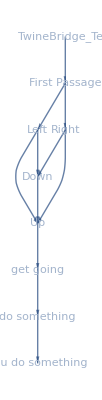

```mathematica
twineSummary[twineAssoc]
```

### Different Forms

```mathematica
testingAssoc =<|"Other Story" -><|"Two" -> "Go to passage [[Three]]", "Three" ->  "Here we are at Passage Three"|>|>;
```

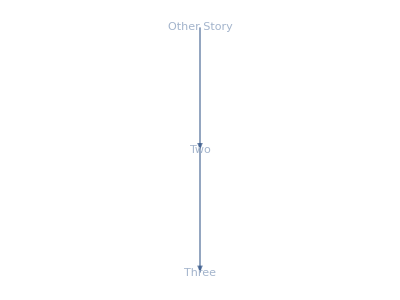

```mathematica
twineSummary[testingAssoc]
```

```mathematica
twineAssocNewForm = <|"TwineBridge_Test"-><|"First Passage"->"This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?","Left"->"From here, there are still other places to go. We can go [[Up]] or [[Down]]","Right"->"From here, there are still other places to go. We can go [[Up]] or [[Down]]","Up"->"Now that we are up why don&#39;t we [[get going]]?","Down"->"Now that we are down, why don&#39;t we get [[Up]]?","get going"->"Now that we are going, how about we [[do something]]","do something"->" Hi, I&#39;m doing something, why don&#39;t [[you do something]]?","you do something"->" Go, Get out of here! "|>|>;
```

```mathematica
twineSummary[twineAssocNewForm]
```

-Graphics-

```mathematica
twineSummary[twineAssocNewForm, "Graph"]
```

-Graphics-

```mathematica
twineSummary[twineAssocNewForm, "Export"]
```

Graph Vertices  {{0.,7.},{0.,6.},{-1.,5.},{0.,5.},{-1.,3.},{-1.,4.},{-1.,2.},{-1.,1.},{-1.,0.}}

Graph Points for Twine  {{0.,250.},{0.,500.},{0.,750.},{0.,1250.},{0.,1000.},{250.,1500.},{0.,1500.},{250.,1750.},{250.,2000.}}

The issue now: Need to LOCALIZE the Dynamic Variable, so for each story that is Summarized in a notebook the passages won’t interfere.

```mathematica
twineSummary[twineAssocNewForm, "Export"]
```

### Position of Passages

I can use the vertex positions from the graph for passage positions 
Let’s work on extracting those things.

```mathematica
Graph[{1,2, 3}, {1->2, 2->3,3 -> 1}]//GraphEmbedding
```

{{-0.866025,-0.5},{0.866025,-0.5},{1.83697×10^-16,1.}}

```mathematica
Rescale[%2562 , {Min[%2562], Max[%2562]}, {0, 100}]
```

{{0.,19.6152},{92.8203,19.6152},{46.4102,100.}}

```mathematica
GraphicsRow[{Column@GraphEmbedding@twineSummary[twineAssocNewForm, "Graph"],twineSummary[twineAssocNewForm, "Graph"] }]
```

```mathematica
Rescale[Rescale[%2573 ],{0,1}, {0,500}]
```

{{62.5,500.},{62.5,437.5},{0.,375.},{62.5,375.},{0.,250.},{0.,312.5},{0.,187.5},{0.,125.},{0.,62.5}}

```mathematica
Reverse/@%2619
```

{{500.,62.5},{437.5,62.5},{375.,0.},{375.,62.5},{250.,0.},{312.5,0.},{187.5,0.},{125.,0.},{62.5,0.}}

```mathematica
{{-1, 0}, {0, 0}, {1, 0}}
```

```mathematica
Transpose[{{-1, 0}, {0, 0}, {1, 0}}]
```

{{-1,0,1},{0,0,0}}

```mathematica
Rescale[#]&/@%2712
```

{{0,1/2,1},{0,0,0}}

```mathematica
Rescale[%2713, {0,1}, {10, 390}]
```

{{10,200,390},{10,10,10}}

```mathematica
Rescale[{{-1, 0}, {0, 0}, {1, 0}}, {-1, 1}, {10, 390}]
```

{{10,200},{200,200},{390,200}}

### Larger Stories

First : Strip out HTML header stuff and leave just the <tw-storydata> and <tw-passagedata>

```mathematica
{twLargeGraph, twLargeAssoc} =twineImport["~/Desktop/DepthsOfSarcasmV17.html"];
```

```mathematica
twineSummary[twLargeAssoc]
```

```mathematica
twineSummary[twISCAssoc]
```

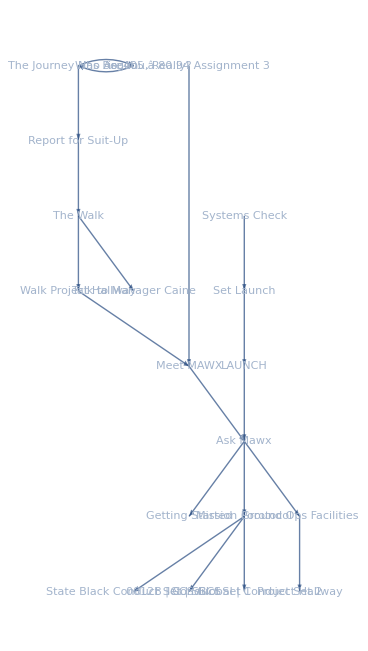

```mathematica
twineSummary[twISCAssoc, "Graph"]
```

```mathematica
fString = Import["~/Desktop/DepthsOfSarcasmV17.html", "String"];
```

```mathematica
StringTake[fString, 23]
```

<!DOCTYPE html>
<html>

```mathematica
StringCases[fString, htmlHeader___~~ important:("<tw-storydata"~~ ___ ~~ "</tw-storydata>")~~___ ~~EndOfString:> important]
```

{<tw-storydata name="DepthsOfSarcasmV17" startnode="1" creator="Twine" creator-version="2.0.10" ifid="9ACF5B91-2190-43BC-A1EE-1B9FA0898772" format="Harlowe" options="" hidden><style role="stylesheet" id="twine-user-stylesheet" type="text/twine-css">tw-sidebar {
    display: none;
}




























</style><script role="script" id="twine-user-script" type="text/twine-javascript">




























</script><tw-passagedata pid="1" name="start" tags="" position="1302,115">(text-style: &quot;superscript&quot;)[(align: &quot;==&gt;&quot;)[(c) 2016 Sam Wilson
Version 1.7.3] ]

(display: &quot;startup&quot;)(set: $goldtogo to 1000-$gold)Journey into...

(text-style: &quot;bold&quot;)[THE DEPTHS OF SARCASM]

(either: &quot;Great title.&quot;,&quot;A legitimate way to spend your time.&quot;,&quot;A thrilling adventure.&quot;)

You&#39;re on a quest to collect 1000 gold pieces because you&#39;re really imaginative.

The entrance of a cave in front of you.

[[Enter the cave-&gt;newroom]]









</tw-passagedata>
<tw-passagedata pid="2" name="newroom" tags="" position="2011,112">You enter a (either: &quot;dingy&quot;, &quot;dank&quot;, &quot;miserable&quot;, &quot;poorly-lit&quot;, &quot;gross&quot;,&quot;slimy&quot;,&quot;gloomy&quot;,&quot;depressing&quot;,&quot;musty-smelling&quot;,&quot;fetid&quot;,&quot;reeking&quot;) (either: &quot;chamber&quot;, &quot;cavern&quot;, &quot;room&quot;, &quot;tunnel&quot;, &quot;nook&quot;, &quot;vault&quot;,&quot;crypt&quot;,&quot;passage&quot;).

(set: $coinflip to (random: 1, 5))(if: $coinflip is 1)[(either:&quot;A monster leaps out at you.&quot;,&quot;A monster drops down on you.&quot;,&quot;A monster crawls out of the shadows.&quot;,&quot;You walk straight into a monster.&quot;,&quot;Oh look. A monster. What a surprise.&quot;,&quot;And is that a monster over there? Of course it is.&quot;)

[[Fight the monster-&gt;newmonster]] ](if: $coinflip is 2)[You find a treasure chest. (either: &quot;Because everyone leaves treasure chests lying around.&quot;, &quot;Like you do.&quot;, &quot;Great.&quot;)

[[Open the chest-&gt;chest]]
[[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]] ](if: $coinflip&gt;2)[(either: &quot;This place is brimming with excitement.&quot;, &quot;This place is just the best.&quot;, &quot;You can&#39;t get over how awesome it is.&quot;, &quot;Fantastic.&quot;, &quot;Just wow.&quot;,&quot;Lovely.&quot;,&quot;Epic.&quot;,&quot;You seriously consider settling down here and picking out curtains.&quot;)

[[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]] ]
(if: $coinflip&gt;1 and $potions&gt;0)[ [[Drink a potion-&gt;drink a potion]] ]

</tw-passagedata>
<tw-passagedata pid="3" name="drink a potion" tags="" position="2143,1059">(set: $potions to $potions-1)(if: $hp is $maxhp)[(either:&quot;You were already at full health, genius.&quot;,&quot;Yeah. You really needed to do that.&quot;,&quot;Oh boy, what a great use of a potion.&quot;,&quot;Some people would consider that a spectacular waste.&quot;,&quot;Drinking a potion when you&#39;re already at full health? Well done.&quot;)

](if: $hp &lt; $maxhp)[(set: $hp to it+10)You are healed by 10 hit points.

](if: $hp&gt;$maxhp)[(set: $hp to $maxhp)You&#39;re at maximum health. 

](if: $potions&gt;0)[ [[Drink another potion-&gt;drink a potion]] 
][[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="4" name="hit" tags="" position="1407,1466">(set: $attackpower to (random: $xp,$xp*5)+$sword)(set: $monsterhealth to it-$attackpower)(if: $monsterhealth&lt;1)[(set: $monsterhealth to 0)](either: &quot;Thwack.&quot;,&quot;Crunch.&quot;,&quot;Flam.&quot;,&quot;Kapow.&quot;,&quot;Kablooie.&quot;,&quot;Thump.&quot;,&quot;Bloof.&quot;,&quot;Paf.&quot;) You hit the $monstername for $attackpower damage.

The $monstername&#39;s health is $monsterhealth.

(if: $monsterhealth&gt;0)[It attacks.

[[Defend-&gt;defend]]
[[Run away-&gt;runaway]] 
](if: $bribeammount&lt;$gold and $hp&gt;0 and $monsterhealth&gt;0)[ [[Bribe-&gt;bribe]] 
](if: $monsterhealth&lt;1)[You won. (either: &quot;Woo.&quot;,&quot;Whoopee.&quot;,&quot;Go you.&quot;,&quot;What a champ.&quot;,&quot;Staggering.&quot;,&quot;Inspiring.&quot;,&quot;You&#39;re amazing.&quot;,&quot;You probably deserve a parade.&quot;,&quot;We&#39;re all so proud.&quot;)

[[Loot the room-&gt;win]] ]

</tw-passagedata>
<tw-passagedata pid="5" name="bribe" tags="" position="1069,1630">(set: $gold to $gold-$bribeammount)The $monstername takes $bribeammount gold coins from you and kicks you out the door. Because (print: $monstername+&quot;s&quot;) need gold, I guess. Yeah, authentic.

[[Continue exploring-&gt;newroom]] </tw-passagedata>
<tw-passagedata pid="6" name="runaway" tags="" position="1076,1445">(set: $damage to (random: $monsterlevel, $monsterlevel*3))(set: $hp to $hp-$damage)(either: &quot;Truely you are the hero that the world needs.&quot;,&quot;So inspiring.&quot;,&quot;A picture of bravery.&quot;,&quot;Lion-hearted. Really.&quot;,&quot;Gallant.&quot;)

As you run away the $monstername hits you for $damage damage.

(if: $hp &gt; 0)[ [[Continue exploring-&gt;newroom]] ]
(if: $potions&gt;0 and $hp &gt; 0)[ [[Drink a potion-&gt;drink a potion]] ]
(if: $hp &lt; 1)[ You are so dead.  

[[Game over-&gt;gameover]] ]

</tw-passagedata>
<tw-passagedata pid="7" name="newmonster" tags="" position="1507,1288">(set: $monsterid to (random: 1,10))(set: $monstername to $monsterid of $monsterarray)(set: $monsterlevel to (random: $xp, $xp+2))(set: $imonsterhealth to $monsterlevel*3)(set: $monsterhealth to $imonsterhealth+7)(set: $bribeammount to $monsterlevel*10)You are fighing a level $monsterlevel $monstername. (either: &quot;What an ugly bastard.&quot;,&quot;It&#39;s quite the looker.&quot;,&quot;You can tell you&#39;re going to be besties.&quot;,&quot;Sigh.&quot;,&quot;Let&#39;s get this over with.&quot;,&quot;Oh joy.&quot;) It has $monsterhealth health.

 [[Hit the monster-&gt;hit]]
 [[Run away-&gt;runaway]]
 (if: $bribeammount&lt;$gold)[ [[Bribe the monster-&gt;bribe]] 
](if: $potions&gt;0)[ [[Drink a potion-&gt;battledrink]] 
](if: $poisons&gt;0)[ [[Throw a poison-&gt;battlepoison]] 
]</tw-passagedata>
<tw-passagedata pid="8" name="defend" tags="" position="1418,1625">(set: $damage to (random: $monsterlevel, $monsterlevel*3))(set: $damage to $damage-$shield)(if: $damage&lt;0)[(set: $damage to 0)](set: $hp to $hp-$damage)(either: &quot;Thwack.&quot;,&quot;Crunch.&quot;,&quot;Flam.&quot;,&quot;Kapow.&quot;,&quot;Kablooie.&quot;,&quot;Thump.&quot;,&quot;Bloof.&quot;,&quot;Paf.&quot;) The $monstername hits you for $damage damage.

(if: $hp&lt;1)[ You are so dead.

[[Game over-&gt;gameover]] ](if: $hp&gt;0)[The $monstername has $monsterhealth health. 

](if: $hp&gt;0)[ [[Hit it again-&gt;hit]]
[[Run away-&gt;runaway]]
](if: $bribeammount&lt;$gold and $hp&gt;0)[ [[bribe]] 
](if: $potions&gt;0 and $hp&gt;0)[ [[Drink a potion-&gt;battledrink]] 
](if: $poisons&gt;0 and $hp&gt;0)[ [[Throw a poison-&gt;battlepoison]] 
]</tw-passagedata>
<tw-passagedata pid="9" name="win" tags="" position="1075,1281">You go up a level. (either: &quot;Because levels are real things.&quot;,&quot;Don&#39;t break anything with your amazing new powers.&quot;,&quot;Hail the conquering hero.&quot;,&quot;So, yay, progress.&quot;,&quot;It looks like you needed it.&quot;)

(set: $cashammount to (random: $monsterlevel, $monsterlevel*10))(set: $gold to $gold+$cashammount)(set: $xp to $xp+1)(set: $monsterkills to it+1)(either:&quot;You found $cashammount gold coins in the dead $monstername&#39;s pockets.

A $monstername with pockets. Yeah.&quot;,&quot;You pick up $cashammount gold coins that are scattered across the floor.&quot;,&quot;You drag the $monstername&#39;s corpse to the village taxidermist and collect a bounty of $cashammount gold coins.&quot;,&quot;You find $cashammount gold coins on one of the corpses scattered around the room.&quot;,&quot;You cut the $monstername&#39;s body open and $cashammount gold coins fall out. What a believable thing to happen.&quot;)
(if: $gold&lt;1000)[
[[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]]
(if: $potions&gt;0)[ [[Drink a potion-&gt;drink a potion]] ] ](if: $gold&gt;999)[
You know what that means? You just won the game.

[[Game Over-&gt;gameover]] ]

</tw-passagedata>
<tw-passagedata pid="10" name="battledrink" tags="" position="1578,1459">(set: $potions to $potions-1)You are healed by 10 hit points. (if: $hp is $maxhp)[But you were already at maximum health. So that was a potion well-spent. Just so we&#39;re on the same page here:](set: $hp to it+10)(if: $hp&gt;=$maxhp)[(set: $hp to $maxhp)

You&#39;re at maximum health.]

(if: $potions &gt; 0)[[[Drink another-&gt;battledrink]]
][[Fight-&gt;defend]]</tw-passagedata>
<tw-passagedata pid="11" name="market" tags="" position="3530,300">(if: $visitedmarket is false)[You head out of the caves and back to the local village, which is a bustling metropolis called &quot;Pigswill&quot;. The storekeeper greets you with a belch.(set: $visitedmarket to true)

]You look at the wares on sale.(if: $gold&lt;10)[

There&#39;s nothing you can afford.]

(if: $potions&gt;0)[ [[Sell a potion for 5 gold-&gt;sell potion]] 
](if: $poisons&gt;0)[ [[Sell a poison for 10 gold-&gt;sell poison]] 
](if: $gold&gt;24)[ [[Buy a cardboard shield for 25 gold-&gt;buy shield]] 
](if: $gold&gt;49)[ [[Buy a wooden sword for 50 gold-&gt;buy sword]]
](if: $gold&gt;74)[ [[Buy a wooden shield for 75 gold-&gt;buy shield2]] 
](if: $gold&gt;99)[ [[Buy a tin sword for 100 gold-&gt;buy sword2]]
](if: $gold&gt;9)[ [[Buy a potion for 10 gold-&gt;buy potion]] 
](if: $gold&gt;19)[ [[Buy a poison for 20 gold-&gt;buy poison]] 
][[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="12" name="buy potion" tags="" position="3327,512">(set: $gold to it-10)(set: $potions to it+1)Magic potion. A totally real thing. 

[[Continue shopping-&gt;market]]
[[Drink the potion-&gt;drink a potion]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="13" name="buy shield" tags="" position="3550,617">(set: $gold to it-25)(if: $shield is 0)[You pick up your new cardboard shield. You&#39;re safe now. This game is as good as won.](if: $shield is 5)[Yeah, you can never waste enough gold coins on identical cardboard shields.](if: $shield is 10)[You had a wooden shield that was capable of protecting you against double the damage, but no, whatever you want. You toss your significantly better shield aside and take your new cardboard shield.](set: $shield to 5)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="14" name="buy sword" tags="" position="3259,137">(set: $gold to it-50)(if: $sword is 0)[Wood. The substance with amazing slicing properties. Hence the well known expression &quot;As sharp as wood.&quot;](if: $sword is 10)[You already have one of those, but fine. You throw it away and take this one. Because clearly the old one wasn&#39;t exactly as good in every way. This new one is one beautiful wooden sword.](if: $sword is 20)[You... you had a better sword. You just threw it away for this sword. Made of wood. 

Masterful. We&#39;re in awe.]


(set: $sword to 10)[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="15" name="sell potion" tags="" position="3732,117">(set: $gold to it+5)(set: $potions to it-1)(if: $gold&lt;1000)[Five gold? (either: &quot;What a rip-off.&quot;,&quot;You&#39;re a real entrepreneur.&quot;)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]]
(if: $gold&gt;999)[So you just won the game. By selling a potion. What a climax.

[[Game Over-&gt;gameover]] ]

</tw-passagedata>
<tw-passagedata pid="16" name="Footer" tags="footer" position="22,300">



   (set: $ihp to $xp*3)(set: $maxhp to $ihp+7)Health: $hp/$maxhp Gold: $gold Potions: $potions Poisons: $poisons 
   Experience Level: $xp
   Shield: (if: $shield is 0)[None.](if: $shield is 5)[Cardboard.](if: $shield is 10)[Wood.] Sword: (if: $sword is 0)[A stick.](if: $sword is 10)[Wood.](if: $sword is 20)[Tin.]
   ] ] ]</tw-passagedata>
<tw-passagedata pid="17" name="startup" tags="startup" position="20,3">(set: $first to true)(set: $visitedmarket to false)(set: $shield to 0)(set: $sword to 0)(set: $hp to 10)(set: $gold to 0)(set: $xp to 1)(set: $potions to 3)(set: $poisons to 0)(set: $monsterarray to (a: &quot;cave eel&quot;,&quot;toadwolf&quot;,&quot;octopus&quot;,&quot;lurking shadow&quot;,&quot;fang vortex&quot;,&quot;battlecrab&quot;,&quot;maw&quot;,&quot;Thing From Beyond&quot;, &quot;slither&quot;,&quot;lunk ape&quot;))(set: $monsterkills to 0)</tw-passagedata>
<tw-passagedata pid="18" name="header" tags="header" position="26,147">(background: black)[(colour: green)[(font: &#39;courier&#39;)[ </tw-passagedata>
<tw-passagedata pid="19" name="chest" tags="" position="2705,1261">(set: $coinflip to (random: 1,4))(either:&quot;You pry open the chest with your (if:$sword is 0)[stick.](if:$sword is 10)[wooden sword.](if:$sword is 20)[tin sword.]&quot;,&quot;You open the chest with one of the keys lying around. Yeah, any key can open any chest around here. That&#39;s just basic security.&quot;)

(if: $coinflip is 1)[A monster leaps out. (either: &quot;It was hiding in there. Curled up real small.&quot;,&quot;It&#39;s been hiding in there for a while. It&#39;s obviously a busy creature with a lot going on in its life.&quot;,&quot;Boo.&quot;,&quot;And you thought the day couldn&#39;t get better.&quot;)

[[Fight the monster-&gt;newmonster]] ](if: $coinflip &gt; 1)[(set: $newgold to (random: $xp, $maxhp))(set: $gold to it+$newgold)(if: $gold&lt;1000)[You find $newgold gold coins. (either:&quot;What a bounty.&quot;,&quot;Whoop dee doo.&quot;,&quot;Go you.&quot;)] ]

(if: $coinflip &gt; 2 and $gold&lt;1000)[(set: $potions to it+1) And you also find a potion. (either:&quot;So there&#39;s that.&quot;,&quot;Yay.&quot;,&quot;Hurrah.&quot;)

](if: $coinflip &gt; 3 and $gold&lt;1000)[(set: $poisons to it+1) And a poison. (either:&quot;Look at you go.&quot;,&quot;You&#39;re on such a roll.&quot;)

](if: $coinflip&gt;1 and $gold&lt;1000)[ [[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]] ](if: $gold&gt;999)[You have more than a thousand gold coins. So you&#39;ve won.

[[Game Over-&gt;gameover]] ]
(if: $coinflip&gt;1 and $potions&gt;0 and $gold&gt;999)[ [[Drink a potion-&gt;drink a potion]] ]</tw-passagedata>
<tw-passagedata pid="20" name="buy shield2" tags="" position="3730,508">(set: $gold to it-75)(if: $shield &lt; 10)[A wooden shield. You&#39;re now completely and totally invulnerable, assuming that you don&#39;t encounter fire, acid, arrows, swords, fast-moving rocks, clubs, maces, magic bolts, rays of frost, enemies of any kind, or woodworms.](if: $shield is 10)[You can never have enough of these. Apparently.](set: $shield to 10)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="21" name="buy sword2" tags="" position="3521,64">(set: $gold to it-100)(if: $sword &lt; 20)[Tin. A tin sword. Worth every one of the hundred coins of actual gold that you&#39;ve just given away for it.](if: $sword is 20)[Another identical tin sword. No, you go ahead, buy it. You evidently know what you&#39;re doing.](set: $sword to 20)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="22" name="buy poison" tags="" position="3245,307">(set: $gold to it-20)(set: $poisons to it+1)(if: $poisons is 1)[A deadly liquid that looks almost identical to all the other potions that you&#39;re drinking. This will end well.

]You take a bottle of poison.

[[Continue shopping-&gt;market]]
[[Drink the potion-&gt;drink a potion]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="23" name="sell poison" tags="" position="3766,300">(set: $gold to it+10)(set: $poisons to it-1)(if: $gold&lt;1000)[(either: &quot;You sell it for half the price you normally buy it for. Way to go.&quot;,&quot;Yeah, that probably wouldn&#39;t have been useful in that in EVERY SINGLE BATTLE.&quot;)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]] ](if: $gold&gt;999)[You just won the game by selling a poison.

What a satisfying ending.

[[Game Over-&gt;gameover]] ]</tw-passagedata>
<tw-passagedata pid="24" name="battlepoison" tags="" position="1587,1631">Poison. The heroic way to win a fight. You throw a bottle at the $monstername.

(set: $coinflip to (random:1,2))(if: $coinflip is 1)[It misses.

[[Nice aim, jackass-&gt;hit]] ](if: $coinflip is 2)[(set: $monsterhealth to it-10)It goes into its mouth.

The monster is distracted. And poisoned. Obviously.

[[Hit the monster-&gt;hit]] ]</tw-passagedata>
<tw-passagedata pid="25" name="gameover" tags="" position="1307,380">(text-style: &quot;bold&quot;)[THANK YOU FOR PLAYING THE DEPTHS OF SARCASM
(either:&quot;HAVE A WONDERFUL DAY&quot;,&quot;WHAT AN AMAZING PERFORMANCE&quot;,&quot;YOU MUST BE SO PROUD&quot;,&quot;GREAT JOB ALL ROUND&quot;,&quot;DON&#39;T FORGET TO TIP THE MONSTERS&quot;,&quot;CLOSE THE DOOR ON YOUR WAY OUT&quot;,&quot;YOU WERE AN AMAZING PLAYER&quot;)]

You collected $gold gold coins and defeated $monsterkills monsters.

[[Play again-&gt;start]]</tw-passagedata>
</tw-storydata>}

```mathematica
StringSplit[fString, "<tw-storydata>"]
```

{<!DOCTYPE html>
<html>
<head>
<meta charset="utf-8">
<title>DepthsOfSarcasmV17</title>
<style title="Twine CSS">@-webkit-keyframes $animation-name{0%{opacity:0}to{opacity:1}}@keyframes $animation-name{0%{opacity:0}to{opacity:1}}@-webkit-keyframes $animation-name{0%,to{opacity:0}50%{opacity:1}}@keyframes $animation-name{0%,to{opacity:0}50%{opacity:1}}@-webkit-keyframes $animation-name{0%,to{}50%{-webkit-transform:translateY(-0.2em);transform:translateY(-0.2em)}}@keyframes $animation-name{0%,to{}50%{-webkit-transform:translateY(-0.2em);transform:translateY(-0.2em)}}@-webkit-keyframes $animation-name{0%,to{}50%{-webkit-transform:translateX(0.2em);transform:translateX(0.2em)}}@keyframes $animation-name{0%,to{}50%{-webkit-transform:translateX(0.2em);transform:translateX(0.2em)}}@-webkit-keyframes $animation-name{0%{background-color:white;color:white}to{}}@keyframes $animation-name{0%{background-color:white;color:white}to{}}@-webkit-keyframes $animation-name{0%{-webkit-transform:scale(0, 0);transform:scale(0, 0)}20%{-webkit-transform:scale(1.2, 1.2);transform:scale(1.2, 1.2)}40%{-webkit-transform:scale(0.9, 0.9);transform:scale(0.9, 0.9)}60%{-webkit-transform:scale(1.05, 1.05);transform:scale(1.05, 1.05)}80%{-webkit-transform:scale(0.925, 0.925);transform:scale(0.925, 0.925)}to{-webkit-transform:scale(1, 1);transform:scale(1, 1)}}@keyframes $animation-name{0%{-webkit-transform:scale(0, 0);transform:scale(0, 0)}20%{-webkit-transform:scale(1.2, 1.2);transform:scale(1.2, 1.2)}40%{-webkit-transform:scale(0.9, 0.9);transform:scale(0.9, 0.9)}60%{-webkit-transform:scale(1.05, 1.05);transform:scale(1.05, 1.05)}80%{-webkit-transform:scale(0.925, 0.925);transform:scale(0.925, 0.925)}to{-webkit-transform:scale(1, 1);transform:scale(1, 1)}}@-webkit-keyframes $animation-name{0%,to{-webkit-transform:translateX(0em);transform:translateX(0em)}5%,25%,45%{-webkit-transform:translateX(-1em);transform:translateX(-1em)}15%,35%,55%{-webkit-transform:translateX(1em);transform:translateX(1em)}65%{-webkit-transform:translateX(-0.6em);transform:translateX(-0.6em)}75%{-webkit-transform:translateX(0.6em);transform:translateX(0.6em)}85%{-webkit-transform:translateX(-0.2em);transform:translateX(-0.2em)}95%{-webkit-transform:translateX(0.2em);transform:translateX(0.2em)}}@keyframes $animation-name{0%,to{-webkit-transform:translateX(0em);transform:translateX(0em)}5%,25%,45%{-webkit-transform:translateX(-1em);transform:translateX(-1em)}15%,35%,55%{-webkit-transform:translateX(1em);transform:translateX(1em)}65%{-webkit-transform:translateX(-0.6em);transform:translateX(-0.6em)}75%{-webkit-transform:translateX(0.6em);transform:translateX(0.6em)}85%{-webkit-transform:translateX(-0.2em);transform:translateX(-0.2em)}95%{-webkit-transform:translateX(0.2em);transform:translateX(0.2em)}}.debug-mode tw-expression[type=hookref]{background-color:rgba(115,123,140,0.15)}.debug-mode tw-expression[type=hookref]::after{font-size:0.8rem;padding-left:0.2rem;padding-right:0.2rem;vertical-align:top;content:"?" attr(name)}.debug-mode tw-expression[type=variable]{background-color:rgba(140,128,115,0.15)}.debug-mode tw-expression[type=variable]::after{font-size:0.8rem;padding-left:0.2rem;padding-right:0.2rem;vertical-align:top;content:"$" attr(name)}.debug-mode tw-expression[type=macro]:nth-of-type(4n+0){background-color:rgba(136,153,102,0.15)}.debug-mode tw-expression[type=macro]:nth-of-type(2n+1){background-color:rgba(102,153,102,0.15)}.debug-mode tw-expression[type=macro]:nth-of-type(4n+2){background-color:rgba(102,153,136,0.15)}.debug-mode tw-expression[type=macro][name="display"]{background-color:rgba(0,170,255,0.1) !important}.debug-mode tw-expression[type=macro][name="if"],.debug-mode tw-expression[type=macro][name="if"]+tw-hook:not([name]),.debug-mode tw-expression[type=macro][name="unless"],.debug-mode tw-expression[type=macro][name="unless"]+tw-hook:not([name]),.debug-mode tw-expression[type=macro][name="elseif"],.debug-mode tw-expression[type=macro][name="elseif"]+tw-hook:not([name]),.debug-mode tw-expression[type=macro][name="else"],.debug-mode tw-expression[type=macro][name="else"]+tw-hook:not([name]){background-color:rgba(0,255,0,0.1) !important}.debug-mode tw-expression[type=macro].false{background-color:rgba(255,0,0,0.2) !important}.debug-mode tw-expression[type=macro].false+tw-hook:not([name]){display:none}.debug-mode tw-expression[type=macro][name="a"],.debug-mode tw-expression[type=macro][name="array"],.debug-mode tw-expression[type=macro][name="datamap"],.debug-mode tw-expression[type=macro][name="dataset"],.debug-mode tw-expression[type=macro][name="colour"],.debug-mode tw-expression[type=macro][name="color"],.debug-mode tw-expression[type=macro][name="num"],.debug-mode tw-expression[type=macro][name="number"],.debug-mode tw-expression[type=macro][name="text"],.debug-mode tw-expression[type=macro][name="print"]{background-color:rgba(255,255,0,0.2) !important}.debug-mode tw-expression[type=macro][name="put"],.debug-mode tw-expression[type=macro][name="set"]{background-color:rgba(255,128,0,0.2) !important}.debug-mode tw-expression[type=macro][name="script"]{background-color:rgba(255,191,0,0.2) !important}.debug-mode tw-expression[type=macro][name="style"]{background-color:rgba(185,198,198,0.2) !important}.debug-mode tw-expression[type=macro][name^="link"],.debug-mode tw-expression[type=macro][name^="click"],.debug-mode tw-expression[type=macro][name^="mouseover"],.debug-mode tw-expression[type=macro][name^="mouseout"]{background-color:rgba(128,223,32,0.2) !important}.debug-mode tw-expression[type=macro][name^="replace"],.debug-mode tw-expression[type=macro][name^="prepend"],.debug-mode tw-expression[type=macro][name^="append"],.debug-mode tw-expression[type=macro][name^="remove"]{background-color:rgba(223,96,32,0.2) !important}.debug-mode tw-expression[type=macro][name="live"]{background-color:rgba(32,96,223,0.2) !important}.debug-mode tw-expression[type=macro]::before{content:"(" attr(name) ":)";padding:0 0.5rem;font-size:1rem;vertical-align:middle;line-height:normal;background-color:inherit;border:1px solid rgba(255,255,255,0.5)}.debug-mode tw-hook{background-color:rgba(0,85,255,0.1) !important}.debug-mode tw-hook::before{font-size:0.8rem;padding-left:0.2rem;padding-right:0.2rem;vertical-align:top;content:"["}.debug-mode tw-hook::after{font-size:0.8rem;padding-left:0.2rem;padding-right:0.2rem;vertical-align:top;content:"]"}.debug-mode tw-hook[name]::after{font-size:0.8rem;padding-left:0.2rem;padding-right:0.2rem;vertical-align:top;content:"]<" attr(name) "|"}.debug-mode tw-pseudo-hook{background-color:rgba(255,170,0,0.1) !important}.debug-mode tw-collapsed::before{font-size:0.8rem;padding-left:0.2rem;padding-right:0.2rem;vertical-align:top;content:"{"}.debug-mode tw-collapsed::after{font-size:0.8rem;padding-left:0.2rem;padding-right:0.2rem;vertical-align:top;content:"}"}.debug-mode tw-verbatim::before,.debug-mode tw-verbatim::after{font-size:0.8rem;padding-left:0.2rem;padding-right:0.2rem;vertical-align:top;content:"`"}.debug-mode tw-align[style*="text-align: center"]{background:linear-gradient(to right, rgba(255,204,189,0) 0%, rgba(255,204,189,0.25) 50%, rgba(255,204,189,0) 100%)}.debug-mode tw-align[style*="text-align: left"]{background:linear-gradient(to right, rgba(255,204,189,0.25) 0%, rgba(255,204,189,0) 100%)}.debug-mode tw-align[style*="text-align: right"]{background:linear-gradient(to right, rgba(255,204,189,0) 0%, rgba(255,204,189,0.25) 100%)}.debug-mode p{background-color:rgba(255,213,0,0.1)}.debug-mode tw-enchantment{animation:enchantment 0.5s infinite;-webkit-animation:enchantment 0.5s infinite;border:1px solid}.debug-mode tw-link::after,.debug-mode tw-broken-link::after{font-size:0.8rem;padding-left:0.2rem;padding-right:0.2rem;vertical-align:top;content:attr(passage-name)}.debug-mode tw-include{background-color:rgba(204,128,51,0.1)}.debug-mode tw-include::before{font-size:0.8rem;padding-left:0.2rem;padding-right:0.2rem;vertical-align:top;content:attr(type) ' "' attr(title) '"'}@keyframes enchantment{0%,to{border-color:#ffb366}50%{border-color:#6fc}}@-webkit-keyframes enchantment{0%,to{border-color:#ffb366}50%{border-color:#6fc}}tw-debugger{position:fixed;bottom:0;right:0;z-index:999999;min-width:10em;min-height:1em;padding:1em;font-size:1.5em;border-left:solid #000 2px;border-top:solid #000 2px;border-top-left-radius:0.5em;background:#fff;transition:opacity 0.2s;-webkit-transition:opacity 0.2s;opacity:0.8}@media screen and (max-width: 1280px){tw-debugger{font-size:1.25em}}@media screen and (max-width: 960px){tw-debugger{font-size:1em}}@media screen and (max-width: 640px){tw-debugger{font-size:0.8em}}tw-debugger:hover{opacity:1}.show-invisibles{border-radius:3px;border:solid #999 1px;background-color:#fff;font-size:inherit}.debug-mode .show-invisibles{background-color:#eee;box-shadow:inset #ddd 3px 5px 0.5em}tw-link,.link,tw-icon{cursor:pointer}tw-link,.enchantment-link{color:#4169E1;font-weight:bold;text-decoration:none;transition:color 0.2s ease-in-out}tw-link:hover,.enchantment-link:hover{color:DeepSkyBlue}tw-link:active,.enchantment-link:active{color:#DD4B39}.visited{color:#6941e1}.visited:hover{color:#E3E}tw-broken-link{color:#993333;border-bottom:2px solid #993333;cursor:not-allowed}.enchantment-hover{border-bottom:1px dashed #666}.enchantment-mouseout{border:rgba(64,149,191,0.25) 1px solid}.enchantment-mouseout:hover{background-color:rgba(64,149,191,0.25);border:transparent 1px solid;border-radius:0.2em}html{font:100% Georgia, serif;margin:0;background-color:transparent;color:#000;height:100%;overflow-x:hidden;box-sizing:border-box}*,:before,:after{position:relative;box-sizing:inherit}body{margin:0;background-color:transparent}tw-storydata{display:none}tw-story{display:-webkit-box;display:-webkit-flex;display:-moz-flex;display:-ms-flexbox;display:flex;-webkit-box-direction:normal;-webkit-box-orient:vertical;-webkit-flex-direction:column;-moz-flex-direction:column;-ms-flex-direction:column;flex-direction:column;width:60%;font-size:1.5em;line-height:1.5em;margin:5% auto}@media screen and (max-width: 1024px){tw-story{font-size:1.2em}}@media screen and (max-width: 896px){tw-story{font-size:1.05em}}@media screen and (max-width: 768px){tw-story{font-size:0.9em}}tw-passage{display:block}tw-sidebar{left:-5em;width:3em;position:absolute;text-align:center;display:block}tw-icon{display:block;margin:0.5em 0;opacity:0.1;font-size:2.75em}tw-icon:hover{opacity:0.3}tw-error{display:inline-block;border-radius:0.2em;padding:0.2em;font-size:1rem;cursor:help}tw-error.error{background-color:rgba(223,58,190,0.4);color:black}tw-error.warning{background-color:rgba(223,140,58,0.4);color:black;display:none}.debug-mode tw-error.warning{display:inline}tw-error-explanation{display:block;font-size:0.8rem;line-height:1rem}tw-error-explanation-button{cursor:pointer;line-height:0em;border-radius:1px;border:1px solid black;font-size:0.8rem;margin:0 0.4rem;opacity:0.5}tw-error-explanation-button .folddown-arrowhead{display:inline-block}tw-notifier{border-radius:0.2em;padding:0.2em;font-size:1rem;background-color:rgba(223,182,58,0.4);display:none}.debug-mode tw-notifier{display:inline}tw-notifier::before{content:attr(message)}tw-colour{border:1px solid black;display:inline-block;width:1em;height:1em}h1{font-size:3em}h2{font-size:2.25em}h3{font-size:1.75em}h1,h2,h3,h4,h5,h6{line-height:1em;margin:0.6em 0}pre{font-size:1rem}small{font-size:70%}big{font-size:120%}mark{color:rgba(0,0,0,0.6);background-color:#ff9}ins{color:rgba(0,0,0,0.6);background-color:rgba(255,242,204,0.5);border-radius:0.5em;box-shadow:0em 0em 0.2em #ffe699;text-decoration:none}del{background-color:#000;text-decoration:none}center{text-align:center;margin:0 auto;width:60%}blink{text-decoration:none;animation:fade-in-out 1s steps(1, end) infinite alternate;-webkit-animation:fade-in-out 1s steps(1, end) infinite alternate}tw-align{display:block}tw-outline{color:white;text-shadow:-1px -1px 0 #000, 1px -1px 0 #000, -1px 1px 0 #000, 1px 1px 0 #000}tw-shadow{text-shadow:0.08em 0.08em 0.08em #000}tw-emboss{text-shadow:0.08em 0.08em 0em #000;color:white}tw-condense{letter-spacing:-0.08em}tw-expand{letter-spacing:0.1em}tw-blur{color:transparent;text-shadow:0em 0em 0.08em #000}tw-blurrier{color:transparent;text-shadow:0em 0em 0.2em #000}tw-blurrier::selection{background-color:transparent;color:transparent}tw-blurrier::-moz-selection{background-color:transparent;color:transparent}tw-smear{color:transparent;text-shadow:0em 0em 0.02em rgba(0,0,0,0.75),-0.2em 0em 0.5em rgba(0,0,0,0.5),0.2em 0em 0.5em rgba(0,0,0,0.5)}tw-mirror{display:inline-block;transform:scaleX(-1);-webkit-transform:scaleX(-1)}tw-upside-down{display:inline-block;transform:scaleY(-1);-webkit-transform:scaleY(-1)}tw-fade-in-out{text-decoration:none;animation:fade-in-out 2s ease-in-out infinite alternate;-webkit-animation:fade-in-out 2s ease-in-out infinite alternate}tw-rumble{-webkit-animation:rumble linear 0.1s 0s infinite;animation:rumble linear 0.1s 0s infinite;display:inline-block}tw-shudder{-webkit-animation:shudder linear 0.1s 0s infinite;animation:shudder linear 0.1s 0s infinite;display:inline-block}tw-shudder-in{animation:shudder-in 1s ease-out;-webkit-animation:shudder-in 1s ease-out}.transition-in{-webkit-animation:appear 0ms step-start;animation:appear 0ms step-start}.transition-out{-webkit-animation:appear 0ms step-end;animation:appear 0ms step-end}[data-t8n^=fade-in].transition-in,.transition-in[data-t8n^=dissolve]{-webkit-animation:appear 0.8s;animation:appear 0.8s}[data-t8n^=dissolve].transition-out{-webkit-animation:appear 0.8s reverse;animation:appear 0.8s reverse}[data-t8n^=shudder-in].transition-in,.transition-in[data-t8n^=shudder]{display:inline-block;-webkit-animation:shudder-in 0.8s;animation:shudder-in 0.8s}[data-t8n^=shudder-out].transition-out,.transition-out[data-t8n^=shudder]{display:inline-block;-webkit-animation:shudder-out 0.8s;animation:shudder-out 0.8s}[data-t8n^=boxflash].transition-in{-webkit-animation:box-flash 0.8s;animation:box-flash 0.8s}[data-t8n^=pulse].transition-in{-webkit-animation:pulse 0.8s;animation:pulse 0.8s}[data-t8n^=pulse].transition-out{-webkit-animation:pulse 0.8s reverse;animation:pulse 0.8s reverse}[data-t8n$=fast]{animation-duration:0.4s;-webkit-animation-duration:0.4s}[data-t8n$=slow]{animation-duration:1.2s;-webkit-animation-duration:1.2s}

</style>
</head>

<body>

<tw-story></tw-story>

<tw-storydata name="DepthsOfSarcasmV17" startnode="1" creator="Twine" creator-version="2.0.10" ifid="9ACF5B91-2190-43BC-A1EE-1B9FA0898772" format="Harlowe" options="" hidden><style role="stylesheet" id="twine-user-stylesheet" type="text/twine-css">tw-sidebar {
    display: none;
}




























</style><script role="script" id="twine-user-script" type="text/twine-javascript">




























</script><tw-passagedata pid="1" name="start" tags="" position="1302,115">(text-style: &quot;superscript&quot;)[(align: &quot;==&gt;&quot;)[(c) 2016 Sam Wilson
Version 1.7.3] ]

(display: &quot;startup&quot;)(set: $goldtogo to 1000-$gold)Journey into...

(text-style: &quot;bold&quot;)[THE DEPTHS OF SARCASM]

(either: &quot;Great title.&quot;,&quot;A legitimate way to spend your time.&quot;,&quot;A thrilling adventure.&quot;)

You&#39;re on a quest to collect 1000 gold pieces because you&#39;re really imaginative.

The entrance of a cave in front of you.

[[Enter the cave-&gt;newroom]]









</tw-passagedata>
<tw-passagedata pid="2" name="newroom" tags="" position="2011,112">You enter a (either: &quot;dingy&quot;, &quot;dank&quot;, &quot;miserable&quot;, &quot;poorly-lit&quot;, &quot;gross&quot;,&quot;slimy&quot;,&quot;gloomy&quot;,&quot;depressing&quot;,&quot;musty-smelling&quot;,&quot;fetid&quot;,&quot;reeking&quot;) (either: &quot;chamber&quot;, &quot;cavern&quot;, &quot;room&quot;, &quot;tunnel&quot;, &quot;nook&quot;, &quot;vault&quot;,&quot;crypt&quot;,&quot;passage&quot;).

(set: $coinflip to (random: 1, 5))(if: $coinflip is 1)[(either:&quot;A monster leaps out at you.&quot;,&quot;A monster drops down on you.&quot;,&quot;A monster crawls out of the shadows.&quot;,&quot;You walk straight into a monster.&quot;,&quot;Oh look. A monster. What a surprise.&quot;,&quot;And is that a monster over there? Of course it is.&quot;)

[[Fight the monster-&gt;newmonster]] ](if: $coinflip is 2)[You find a treasure chest. (either: &quot;Because everyone leaves treasure chests lying around.&quot;, &quot;Like you do.&quot;, &quot;Great.&quot;)

[[Open the chest-&gt;chest]]
[[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]] ](if: $coinflip&gt;2)[(either: &quot;This place is brimming with excitement.&quot;, &quot;This place is just the best.&quot;, &quot;You can&#39;t get over how awesome it is.&quot;, &quot;Fantastic.&quot;, &quot;Just wow.&quot;,&quot;Lovely.&quot;,&quot;Epic.&quot;,&quot;You seriously consider settling down here and picking out curtains.&quot;)

[[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]] ]
(if: $coinflip&gt;1 and $potions&gt;0)[ [[Drink a potion-&gt;drink a potion]] ]

</tw-passagedata>
<tw-passagedata pid="3" name="drink a potion" tags="" position="2143,1059">(set: $potions to $potions-1)(if: $hp is $maxhp)[(either:&quot;You were already at full health, genius.&quot;,&quot;Yeah. You really needed to do that.&quot;,&quot;Oh boy, what a great use of a potion.&quot;,&quot;Some people would consider that a spectacular waste.&quot;,&quot;Drinking a potion when you&#39;re already at full health? Well done.&quot;)

](if: $hp &lt; $maxhp)[(set: $hp to it+10)You are healed by 10 hit points.

](if: $hp&gt;$maxhp)[(set: $hp to $maxhp)You&#39;re at maximum health. 

](if: $potions&gt;0)[ [[Drink another potion-&gt;drink a potion]] 
][[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="4" name="hit" tags="" position="1407,1466">(set: $attackpower to (random: $xp,$xp*5)+$sword)(set: $monsterhealth to it-$attackpower)(if: $monsterhealth&lt;1)[(set: $monsterhealth to 0)](either: &quot;Thwack.&quot;,&quot;Crunch.&quot;,&quot;Flam.&quot;,&quot;Kapow.&quot;,&quot;Kablooie.&quot;,&quot;Thump.&quot;,&quot;Bloof.&quot;,&quot;Paf.&quot;) You hit the $monstername for $attackpower damage.

The $monstername&#39;s health is $monsterhealth.

(if: $monsterhealth&gt;0)[It attacks.

[[Defend-&gt;defend]]
[[Run away-&gt;runaway]] 
](if: $bribeammount&lt;$gold and $hp&gt;0 and $monsterhealth&gt;0)[ [[Bribe-&gt;bribe]] 
](if: $monsterhealth&lt;1)[You won. (either: &quot;Woo.&quot;,&quot;Whoopee.&quot;,&quot;Go you.&quot;,&quot;What a champ.&quot;,&quot;Staggering.&quot;,&quot;Inspiring.&quot;,&quot;You&#39;re amazing.&quot;,&quot;You probably deserve a parade.&quot;,&quot;We&#39;re all so proud.&quot;)

[[Loot the room-&gt;win]] ]

</tw-passagedata>
<tw-passagedata pid="5" name="bribe" tags="" position="1069,1630">(set: $gold to $gold-$bribeammount)The $monstername takes $bribeammount gold coins from you and kicks you out the door. Because (print: $monstername+&quot;s&quot;) need gold, I guess. Yeah, authentic.

[[Continue exploring-&gt;newroom]] </tw-passagedata>
<tw-passagedata pid="6" name="runaway" tags="" position="1076,1445">(set: $damage to (random: $monsterlevel, $monsterlevel*3))(set: $hp to $hp-$damage)(either: &quot;Truely you are the hero that the world needs.&quot;,&quot;So inspiring.&quot;,&quot;A picture of bravery.&quot;,&quot;Lion-hearted. Really.&quot;,&quot;Gallant.&quot;)

As you run away the $monstername hits you for $damage damage.

(if: $hp &gt; 0)[ [[Continue exploring-&gt;newroom]] ]
(if: $potions&gt;0 and $hp &gt; 0)[ [[Drink a potion-&gt;drink a potion]] ]
(if: $hp &lt; 1)[ You are so dead.  

[[Game over-&gt;gameover]] ]

</tw-passagedata>
<tw-passagedata pid="7" name="newmonster" tags="" position="1507,1288">(set: $monsterid to (random: 1,10))(set: $monstername to $monsterid of $monsterarray)(set: $monsterlevel to (random: $xp, $xp+2))(set: $imonsterhealth to $monsterlevel*3)(set: $monsterhealth to $imonsterhealth+7)(set: $bribeammount to $monsterlevel*10)You are fighing a level $monsterlevel $monstername. (either: &quot;What an ugly bastard.&quot;,&quot;It&#39;s quite the looker.&quot;,&quot;You can tell you&#39;re going to be besties.&quot;,&quot;Sigh.&quot;,&quot;Let&#39;s get this over with.&quot;,&quot;Oh joy.&quot;) It has $monsterhealth health.

 [[Hit the monster-&gt;hit]]
 [[Run away-&gt;runaway]]
 (if: $bribeammount&lt;$gold)[ [[Bribe the monster-&gt;bribe]] 
](if: $potions&gt;0)[ [[Drink a potion-&gt;battledrink]] 
](if: $poisons&gt;0)[ [[Throw a poison-&gt;battlepoison]] 
]</tw-passagedata>
<tw-passagedata pid="8" name="defend" tags="" position="1418,1625">(set: $damage to (random: $monsterlevel, $monsterlevel*3))(set: $damage to $damage-$shield)(if: $damage&lt;0)[(set: $damage to 0)](set: $hp to $hp-$damage)(either: &quot;Thwack.&quot;,&quot;Crunch.&quot;,&quot;Flam.&quot;,&quot;Kapow.&quot;,&quot;Kablooie.&quot;,&quot;Thump.&quot;,&quot;Bloof.&quot;,&quot;Paf.&quot;) The $monstername hits you for $damage damage.

(if: $hp&lt;1)[ You are so dead.

[[Game over-&gt;gameover]] ](if: $hp&gt;0)[The $monstername has $monsterhealth health. 

](if: $hp&gt;0)[ [[Hit it again-&gt;hit]]
[[Run away-&gt;runaway]]
](if: $bribeammount&lt;$gold and $hp&gt;0)[ [[bribe]] 
](if: $potions&gt;0 and $hp&gt;0)[ [[Drink a potion-&gt;battledrink]] 
](if: $poisons&gt;0 and $hp&gt;0)[ [[Throw a poison-&gt;battlepoison]] 
]</tw-passagedata>
<tw-passagedata pid="9" name="win" tags="" position="1075,1281">You go up a level. (either: &quot;Because levels are real things.&quot;,&quot;Don&#39;t break anything with your amazing new powers.&quot;,&quot;Hail the conquering hero.&quot;,&quot;So, yay, progress.&quot;,&quot;It looks like you needed it.&quot;)

(set: $cashammount to (random: $monsterlevel, $monsterlevel*10))(set: $gold to $gold+$cashammount)(set: $xp to $xp+1)(set: $monsterkills to it+1)(either:&quot;You found $cashammount gold coins in the dead $monstername&#39;s pockets.

A $monstername with pockets. Yeah.&quot;,&quot;You pick up $cashammount gold coins that are scattered across the floor.&quot;,&quot;You drag the $monstername&#39;s corpse to the village taxidermist and collect a bounty of $cashammount gold coins.&quot;,&quot;You find $cashammount gold coins on one of the corpses scattered around the room.&quot;,&quot;You cut the $monstername&#39;s body open and $cashammount gold coins fall out. What a believable thing to happen.&quot;)
(if: $gold&lt;1000)[
[[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]]
(if: $potions&gt;0)[ [[Drink a potion-&gt;drink a potion]] ] ](if: $gold&gt;999)[
You know what that means? You just won the game.

[[Game Over-&gt;gameover]] ]

</tw-passagedata>
<tw-passagedata pid="10" name="battledrink" tags="" position="1578,1459">(set: $potions to $potions-1)You are healed by 10 hit points. (if: $hp is $maxhp)[But you were already at maximum health. So that was a potion well-spent. Just so we&#39;re on the same page here:](set: $hp to it+10)(if: $hp&gt;=$maxhp)[(set: $hp to $maxhp)

You&#39;re at maximum health.]

(if: $potions &gt; 0)[[[Drink another-&gt;battledrink]]
][[Fight-&gt;defend]]</tw-passagedata>
<tw-passagedata pid="11" name="market" tags="" position="3530,300">(if: $visitedmarket is false)[You head out of the caves and back to the local village, which is a bustling metropolis called &quot;Pigswill&quot;. The storekeeper greets you with a belch.(set: $visitedmarket to true)

]You look at the wares on sale.(if: $gold&lt;10)[

There&#39;s nothing you can afford.]

(if: $potions&gt;0)[ [[Sell a potion for 5 gold-&gt;sell potion]] 
](if: $poisons&gt;0)[ [[Sell a poison for 10 gold-&gt;sell poison]] 
](if: $gold&gt;24)[ [[Buy a cardboard shield for 25 gold-&gt;buy shield]] 
](if: $gold&gt;49)[ [[Buy a wooden sword for 50 gold-&gt;buy sword]]
](if: $gold&gt;74)[ [[Buy a wooden shield for 75 gold-&gt;buy shield2]] 
](if: $gold&gt;99)[ [[Buy a tin sword for 100 gold-&gt;buy sword2]]
](if: $gold&gt;9)[ [[Buy a potion for 10 gold-&gt;buy potion]] 
](if: $gold&gt;19)[ [[Buy a poison for 20 gold-&gt;buy poison]] 
][[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="12" name="buy potion" tags="" position="3327,512">(set: $gold to it-10)(set: $potions to it+1)Magic potion. A totally real thing. 

[[Continue shopping-&gt;market]]
[[Drink the potion-&gt;drink a potion]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="13" name="buy shield" tags="" position="3550,617">(set: $gold to it-25)(if: $shield is 0)[You pick up your new cardboard shield. You&#39;re safe now. This game is as good as won.](if: $shield is 5)[Yeah, you can never waste enough gold coins on identical cardboard shields.](if: $shield is 10)[You had a wooden shield that was capable of protecting you against double the damage, but no, whatever you want. You toss your significantly better shield aside and take your new cardboard shield.](set: $shield to 5)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="14" name="buy sword" tags="" position="3259,137">(set: $gold to it-50)(if: $sword is 0)[Wood. The substance with amazing slicing properties. Hence the well known expression &quot;As sharp as wood.&quot;](if: $sword is 10)[You already have one of those, but fine. You throw it away and take this one. Because clearly the old one wasn&#39;t exactly as good in every way. This new one is one beautiful wooden sword.](if: $sword is 20)[You... you had a better sword. You just threw it away for this sword. Made of wood. 

Masterful. We&#39;re in awe.]


(set: $sword to 10)[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="15" name="sell potion" tags="" position="3732,117">(set: $gold to it+5)(set: $potions to it-1)(if: $gold&lt;1000)[Five gold? (either: &quot;What a rip-off.&quot;,&quot;You&#39;re a real entrepreneur.&quot;)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]]
(if: $gold&gt;999)[So you just won the game. By selling a potion. What a climax.

[[Game Over-&gt;gameover]] ]

</tw-passagedata>
<tw-passagedata pid="16" name="Footer" tags="footer" position="22,300">



   (set: $ihp to $xp*3)(set: $maxhp to $ihp+7)Health: $hp/$maxhp Gold: $gold Potions: $potions Poisons: $poisons 
   Experience Level: $xp
   Shield: (if: $shield is 0)[None.](if: $shield is 5)[Cardboard.](if: $shield is 10)[Wood.] Sword: (if: $sword is 0)[A stick.](if: $sword is 10)[Wood.](if: $sword is 20)[Tin.]
   ] ] ]</tw-passagedata>
<tw-passagedata pid="17" name="startup" tags="startup" position="20,3">(set: $first to true)(set: $visitedmarket to false)(set: $shield to 0)(set: $sword to 0)(set: $hp to 10)(set: $gold to 0)(set: $xp to 1)(set: $potions to 3)(set: $poisons to 0)(set: $monsterarray to (a: &quot;cave eel&quot;,&quot;toadwolf&quot;,&quot;octopus&quot;,&quot;lurking shadow&quot;,&quot;fang vortex&quot;,&quot;battlecrab&quot;,&quot;maw&quot;,&quot;Thing From Beyond&quot;, &quot;slither&quot;,&quot;lunk ape&quot;))(set: $monsterkills to 0)</tw-passagedata>
<tw-passagedata pid="18" name="header" tags="header" position="26,147">(background: black)[(colour: green)[(font: &#39;courier&#39;)[ </tw-passagedata>
<tw-passagedata pid="19" name="chest" tags="" position="2705,1261">(set: $coinflip to (random: 1,4))(either:&quot;You pry open the chest with your (if:$sword is 0)[stick.](if:$sword is 10)[wooden sword.](if:$sword is 20)[tin sword.]&quot;,&quot;You open the chest with one of the keys lying around. Yeah, any key can open any chest around here. That&#39;s just basic security.&quot;)

(if: $coinflip is 1)[A monster leaps out. (either: &quot;It was hiding in there. Curled up real small.&quot;,&quot;It&#39;s been hiding in there for a while. It&#39;s obviously a busy creature with a lot going on in its life.&quot;,&quot;Boo.&quot;,&quot;And you thought the day couldn&#39;t get better.&quot;)

[[Fight the monster-&gt;newmonster]] ](if: $coinflip &gt; 1)[(set: $newgold to (random: $xp, $maxhp))(set: $gold to it+$newgold)(if: $gold&lt;1000)[You find $newgold gold coins. (either:&quot;What a bounty.&quot;,&quot;Whoop dee doo.&quot;,&quot;Go you.&quot;)] ]

(if: $coinflip &gt; 2 and $gold&lt;1000)[(set: $potions to it+1) And you also find a potion. (either:&quot;So there&#39;s that.&quot;,&quot;Yay.&quot;,&quot;Hurrah.&quot;)

](if: $coinflip &gt; 3 and $gold&lt;1000)[(set: $poisons to it+1) And a poison. (either:&quot;Look at you go.&quot;,&quot;You&#39;re on such a roll.&quot;)

](if: $coinflip&gt;1 and $gold&lt;1000)[ [[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]] ](if: $gold&gt;999)[You have more than a thousand gold coins. So you&#39;ve won.

[[Game Over-&gt;gameover]] ]
(if: $coinflip&gt;1 and $potions&gt;0 and $gold&gt;999)[ [[Drink a potion-&gt;drink a potion]] ]</tw-passagedata>
<tw-passagedata pid="20" name="buy shield2" tags="" position="3730,508">(set: $gold to it-75)(if: $shield &lt; 10)[A wooden shield. You&#39;re now completely and totally invulnerable, assuming that you don&#39;t encounter fire, acid, arrows, swords, fast-moving rocks, clubs, maces, magic bolts, rays of frost, enemies of any kind, or woodworms.](if: $shield is 10)[You can never have enough of these. Apparently.](set: $shield to 10)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="21" name="buy sword2" tags="" position="3521,64">(set: $gold to it-100)(if: $sword &lt; 20)[Tin. A tin sword. Worth every one of the hundred coins of actual gold that you&#39;ve just given away for it.](if: $sword is 20)[Another identical tin sword. No, you go ahead, buy it. You evidently know what you&#39;re doing.](set: $sword to 20)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="22" name="buy poison" tags="" position="3245,307">(set: $gold to it-20)(set: $poisons to it+1)(if: $poisons is 1)[A deadly liquid that looks almost identical to all the other potions that you&#39;re drinking. This will end well.

]You take a bottle of poison.

[[Continue shopping-&gt;market]]
[[Drink the potion-&gt;drink a potion]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="23" name="sell poison" tags="" position="3766,300">(set: $gold to it+10)(set: $poisons to it-1)(if: $gold&lt;1000)[(either: &quot;You sell it for half the price you normally buy it for. Way to go.&quot;,&quot;Yeah, that probably wouldn&#39;t have been useful in that in EVERY SINGLE BATTLE.&quot;)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]] ](if: $gold&gt;999)[You just won the game by selling a poison.

What a satisfying ending.

[[Game Over-&gt;gameover]] ]</tw-passagedata>
<tw-passagedata pid="24" name="battlepoison" tags="" position="1587,1631">Poison. The heroic way to win a fight. You throw a bottle at the $monstername.

(set: $coinflip to (random:1,2))(if: $coinflip is 1)[It misses.

[[Nice aim, jackass-&gt;hit]] ](if: $coinflip is 2)[(set: $monsterhealth to it-10)It goes into its mouth.

The monster is distracted. And poisoned. Obviously.

[[Hit the monster-&gt;hit]] ]</tw-passagedata>
<tw-passagedata pid="25" name="gameover" tags="" position="1307,380">(text-style: &quot;bold&quot;)[THANK YOU FOR PLAYING THE DEPTHS OF SARCASM
(either:&quot;HAVE A WONDERFUL DAY&quot;,&quot;WHAT AN AMAZING PERFORMANCE&quot;,&quot;YOU MUST BE SO PROUD&quot;,&quot;GREAT JOB ALL ROUND&quot;,&quot;DON&#39;T FORGET TO TIP THE MONSTERS&quot;,&quot;CLOSE THE DOOR ON YOUR WAY OUT&quot;,&quot;YOU WERE AN AMAZING PLAYER&quot;)]

You collected $gold gold coins and defeated $monsterkills monsters.

[[Play again-&gt;start]]</tw-passagedata>
</tw-storydata>


<script title="Twine engine code" data-main="harlowe">"use strict";var _slicedToArray=function(){function sliceIterator(arr,i){var _arr=[];var _n=true;var _d=false;var _e=undefined;try{for(var _i=arr[Symbol.iterator](),_s;!(_n=(_s=_i.next()).done);_n=true){_arr.push(_s.value);if(i&&_arr.length===i)break}}catch(err){_d=true;_e=err}finally{try{if(!_n&&_i["return"])_i["return"]()}finally{if(_d)throw _e}}return _arr}return function(arr,i){if(Array.isArray(arr)){return arr}else if(Symbol.iterator in Object(arr)){return sliceIterator(arr,i)}else{throw new TypeError("Invalid attempt to destructure non-iterable instance")}}}();function _toConsumableArray(arr){if(Array.isArray(arr)){for(var i=0,arr2=Array(arr.length);i<arr.length;i++){arr2[i]=arr[i]}return arr2}else{return Array.from(arr)}}function _typeof(obj){return obj&&typeof Symbol!=="undefined"&&obj.constructor===Symbol?"symbol":typeof obj}(function(){var requirejs,require,define;(function(undef){var main,req,makeMap,handlers,defined={},waiting={},config={},defining={},hasOwn=Object.prototype.hasOwnProperty,aps=[].slice,jsSuffixRegExp=/\.js$/;function hasProp(obj,prop){return hasOwn.call(obj,prop)}function normalize(name,baseName){var nameParts,nameSegment,mapValue,foundMap,lastIndex,foundI,foundStarMap,starI,i,j,part,baseParts=baseName&&baseName.split("/"),map=config.map,starMap=map&&map["*"]||{};if(name&&name.charAt(0)==="."){if(baseName){name=name.split("/");lastIndex=name.length-1;if(config.nodeIdCompat&&jsSuffixRegExp.test(name[lastIndex])){name[lastIndex]=name[lastIndex].replace(jsSuffixRegExp,"")}name=baseParts.slice(0,baseParts.length-1).concat(name);for(i=0;i<name.length;i+=1){part=name[i];if(part==="."){name.splice(i,1);i-=1}else if(part===".."){if(i===1&&(name[2]===".."||name[0]==="..")){break}else if(i>0){name.splice(i-1,2);i-=2}}}name=name.join("/")}else if(name.indexOf("./")===0){name=name.substring(2)}}if((baseParts||starMap)&&map){nameParts=name.split("/");for(i=nameParts.length;i>0;i-=1){nameSegment=nameParts.slice(0,i).join("/");if(baseParts){for(j=baseParts.length;j>0;j-=1){mapValue=map[baseParts.slice(0,j).join("/")];if(mapValue){mapValue=mapValue[nameSegment];if(mapValue){foundMap=mapValue;foundI=i;break}}}}if(foundMap){break}if(!foundStarMap&&starMap&&starMap[nameSegment]){foundStarMap=starMap[nameSegment];starI=i}}if(!foundMap&&foundStarMap){foundMap=foundStarMap;foundI=starI}if(foundMap){nameParts.splice(0,foundI,foundMap);name=nameParts.join("/")}}return name}function makeRequire(relName,forceSync){return function(){var args=aps.call(arguments,0);if(typeof args[0]!=="string"&&args.length===1){args.push(null)}return req.apply(undef,args.concat([relName,forceSync]))}}function makeNormalize(relName){return function(name){return normalize(name,relName)}}function makeLoad(depName){return function(value){defined[depName]=value}}function callDep(name){if(hasProp(waiting,name)){var args=waiting[name];delete waiting[name];defining[name]=true;main.apply(undef,args)}if(!hasProp(defined,name)&&!hasProp(defining,name)){throw new Error("No "+name)}return defined[name]}function splitPrefix(name){var prefix,index=name?name.indexOf("!"):-1;if(index>-1){prefix=name.substring(0,index);name=name.substring(index+1,name.length)}return[prefix,name]}makeMap=function(name,relName){var plugin,parts=splitPrefix(name),prefix=parts[0];name=parts[1];if(prefix){prefix=normalize(prefix,relName);plugin=callDep(prefix)}if(prefix){if(plugin&&plugin.normalize){name=plugin.normalize(name,makeNormalize(relName))}else{name=normalize(name,relName)}}else{name=normalize(name,relName);parts=splitPrefix(name);prefix=parts[0];name=parts[1];if(prefix){plugin=callDep(prefix)}}return{f:prefix?prefix+"!"+name:name,n:name,pr:prefix,p:plugin}};function makeConfig(name){return function(){return config&&config.config&&config.config[name]||{}}}handlers={require:function require(name){return makeRequire(name)},exports:function exports(name){var e=defined[name];if(typeof e!=="undefined"){return e}else{return defined[name]={}}},module:function module(name){return{id:name,uri:"",exports:defined[name],config:makeConfig(name)}}};main=function(name,deps,callback,relName){var cjsModule,depName,ret,map,i,args=[],callbackType=typeof callback==="undefined"?"undefined":_typeof(callback),usingExports;relName=relName||name;if(callbackType==="undefined"||callbackType==="function"){deps=!deps.length&&callback.length?["require","exports","module"]:deps;for(i=0;i<deps.length;i+=1){map=makeMap(deps[i],relName);depName=map.f;if(depName==="require"){args[i]=handlers.require(name)}else if(depName==="exports"){args[i]=handlers.exports(name);usingExports=true}else if(depName==="module"){cjsModule=args[i]=handlers.module(name)}else if(hasProp(defined,depName)||hasProp(waiting,depName)||hasProp(defining,depName)){args[i]=callDep(depName)}else if(map.p){map.p.load(map.n,makeRequire(relName,true),makeLoad(depName),{});args[i]=defined[depName]}else{throw new Error(name+" missing "+depName)}}ret=callback?callback.apply(defined[name],args):undefined;if(name){if(cjsModule&&cjsModule.exports!==undef&&cjsModule.exports!==defined[name]){defined[name]=cjsModule.exports}else if(ret!==undef||!usingExports){defined[name]=ret}}}else if(name){defined[name]=callback}};requirejs=require=req=function(deps,callback,relName,forceSync,alt){if(typeof deps==="string"){if(handlers[deps]){return handlers[deps](callback)}return callDep(makeMap(deps,callback).f)}else if(!deps.splice){config=deps;if(config.deps){req(config.deps,config.callback)}if(!callback){return}if(callback.splice){deps=callback;callback=relName;relName=null}else{deps=undef}}callback=callback||function(){};if(typeof relName==="function"){relName=forceSync;forceSync=alt}if(forceSync){main(undef,deps,callback,relName)}else{setTimeout(function(){main(undef,deps,callback,relName)},4)}return req};req.config=function(cfg){return req(cfg)};requirejs._defined=defined;define=function(name,deps,callback){if(typeof name!=="string"){throw new Error("See almond README: incorrect module build, no module name")}if(!deps.splice){callback=deps;deps=[]}if(!hasProp(defined,name)&&!hasProp(waiting,name)){waiting[name]=[name,deps,callback]}};define.amd={jQuery:true}})();define("almond",function(){});(function(global,factory){if((typeof module==="undefined"?"undefined":_typeof(module))==="object"&&_typeof(module.exports)==="object"){module.exports=global.document?factory(global,true):function(w){if(!w.document){throw new Error("jQuery requires a window with a document")}return factory(w)}}else{factory(global)}})(typeof window!=="undefined"?window:this,function(window,noGlobal){var arr=[];var _slice=arr.slice;var concat=arr.concat;var push=arr.push;var indexOf=arr.indexOf;var class2type={};var toString=class2type.toString;var hasOwn=class2type.hasOwnProperty;var support={};var document=window.document,version="2.1.4",jQuery=function jQuery(selector,context){return new jQuery.fn.init(selector,context)},rtrim=/^[\s\uFEFF\xA0]+|[\s\uFEFF\xA0]+$/g,rmsPrefix=/^-ms-/,rdashAlpha=/-([\da-z])/gi,fcamelCase=function fcamelCase(all,letter){return letter.toUpperCase()};jQuery.fn=jQuery.prototype={jquery:version,constructor:jQuery,selector:"",length:0,toArray:function toArray(){return _slice.call(this)},get:function get(num){return num!=null?num<0?this[num+this.length]:this[num]:_slice.call(this)},pushStack:function pushStack(elems){var ret=jQuery.merge(this.constructor(),elems);ret.prevObject=this;ret.context=this.context;return ret},each:function each(callback,args){return jQuery.each(this,callback,args)},map:function map(callback){return this.pushStack(jQuery.map(this,function(elem,i){return callback.call(elem,i,elem)}))},slice:function slice(){return this.pushStack(_slice.apply(this,arguments))},first:function first(){return this.eq(0)},last:function last(){return this.eq(-1)},eq:function eq(i){var len=this.length,j=+i+(i<0?len:0);return this.pushStack(j>=0&&j<len?[this[j]]:[])},end:function end(){return this.prevObject||this.constructor(null)},push:push,sort:arr.sort,splice:arr.splice};jQuery.extend=jQuery.fn.extend=function(){var options,name,src,copy,copyIsArray,clone,target=arguments[0]||{},i=1,length=arguments.length,deep=false;if(typeof target==="boolean"){deep=target;target=arguments[i]||{};i++}if((typeof target==="undefined"?"undefined":_typeof(target))!=="object"&&!jQuery.isFunction(target)){target={}}if(i===length){target=this;i--}for(;i<length;i++){if((options=arguments[i])!=null){for(name in options){src=target[name];copy=options[name];if(target===copy){continue}if(deep&&copy&&(jQuery.isPlainObject(copy)||(copyIsArray=jQuery.isArray(copy)))){if(copyIsArray){copyIsArray=false;clone=src&&jQuery.isArray(src)?src:[]}else{clone=src&&jQuery.isPlainObject(src)?src:{}}target[name]=jQuery.extend(deep,clone,copy)}else if(copy!==undefined){target[name]=copy}}}}return target};jQuery.extend({expando:"jQuery"+(version+Math.random()).replace(/\D/g,""),isReady:true,error:function error(msg){throw new Error(msg)},noop:function noop(){},isFunction:function isFunction(obj){return jQuery.type(obj)==="function"},isArray:Array.isArray,isWindow:function isWindow(obj){return obj!=null&&obj===obj.window},isNumeric:function isNumeric(obj){return!jQuery.isArray(obj)&&obj-parseFloat(obj)+1>=0},isPlainObject:function isPlainObject(obj){if(jQuery.type(obj)!=="object"||obj.nodeType||jQuery.isWindow(obj)){return false}if(obj.constructor&&!hasOwn.call(obj.constructor.prototype,"isPrototypeOf")){return false}return true},isEmptyObject:function isEmptyObject(obj){var name;for(name in obj){return false}return true},type:function type(obj){if(obj==null){return obj+""}return(typeof obj==="undefined"?"undefined":_typeof(obj))==="object"||typeof obj==="function"?class2type[toString.call(obj)]||"object":typeof obj==="undefined"?"undefined":_typeof(obj)},globalEval:function globalEval(code){var script,indirect=eval;code=jQuery.trim(code);if(code){if(code.indexOf("use strict")===1){script=document.createElement("script");script.text=code;document.head.appendChild(script).parentNode.removeChild(script)}else{indirect(code)}}},camelCase:function camelCase(string){return string.replace(rmsPrefix,"ms-").replace(rdashAlpha,fcamelCase)},nodeName:function nodeName(elem,name){return elem.nodeName&&elem.nodeName.toLowerCase()===name.toLowerCase()},each:function each(obj,callback,args){var value,i=0,length=obj.length,isArray=isArraylike(obj);if(args){if(isArray){for(;i<length;i++){value=callback.apply(obj[i],args);if(value===false){break}}}else{for(i in obj){value=callback.apply(obj[i],args);if(value===false){break}}}}else{if(isArray){for(;i<length;i++){value=callback.call(obj[i],i,obj[i]);if(value===false){break}}}else{for(i in obj){value=callback.call(obj[i],i,obj[i]);if(value===false){break}}}}return obj},trim:function trim(text){return text==null?"":(text+"").replace(rtrim,"")},makeArray:function makeArray(arr,results){var ret=results||[];if(arr!=null){if(isArraylike(Object(arr))){jQuery.merge(ret,typeof arr==="string"?[arr]:arr)}else{push.call(ret,arr)}}return ret},inArray:function inArray(elem,arr,i){return arr==null?-1:indexOf.call(arr,elem,i)},merge:function merge(first,second){var len=+second.length,j=0,i=first.length;for(;j<len;j++){first[i++]=second[j]}first.length=i;return first},grep:function grep(elems,callback,invert){var callbackInverse,matches=[],i=0,length=elems.length,callbackExpect=!invert;for(;i<length;i++){callbackInverse=!callback(elems[i],i);if(callbackInverse!==callbackExpect){matches.push(elems[i])}}return matches},map:function map(elems,callback,arg){var value,i=0,length=elems.length,isArray=isArraylike(elems),ret=[];if(isArray){for(;i<length;i++){value=callback(elems[i],i,arg);if(value!=null){ret.push(value)}}}else{for(i in elems){value=callback(elems[i],i,arg);if(value!=null){ret.push(value)}}}return concat.apply([],ret)},guid:1,proxy:function proxy(fn,context){var tmp,args,proxy;if(typeof context==="string"){tmp=fn[context];context=fn;fn=tmp}if(!jQuery.isFunction(fn)){return undefined}args=_slice.call(arguments,2);proxy=function(){return fn.apply(context||this,args.concat(_slice.call(arguments)))};proxy.guid=fn.guid=fn.guid||jQuery.guid++;return proxy},now:Date.now,support:support});jQuery.each("Boolean Number String Function Array Date RegExp Object Error".split(" "),function(i,name){class2type["[object "+name+"]"]=name.toLowerCase()});function isArraylike(obj){var length="length"in obj&&obj.length,type=jQuery.type(obj);if(type==="function"||jQuery.isWindow(obj)){return false}if(obj.nodeType===1&&length){return true}return type==="array"||length===0||typeof length==="number"&&length>0&&length-1 in obj}var Sizzle=function(window){var i,support,Expr,getText,isXML,tokenize,compile,select,outermostContext,sortInput,hasDuplicate,setDocument,document,docElem,documentIsHTML,rbuggyQSA,rbuggyMatches,matches,contains,expando="sizzle"+1*new Date,preferredDoc=window.document,dirruns=0,done=0,classCache=createCache(),tokenCache=createCache(),compilerCache=createCache(),sortOrder=function sortOrder(a,b){if(a===b){hasDuplicate=true}return 0},MAX_NEGATIVE=1<<31,hasOwn={}.hasOwnProperty,arr=[],pop=arr.pop,push_native=arr.push,push=arr.push,slice=arr.slice,indexOf=function indexOf(list,elem){var i=0,len=list.length;for(;i<len;i++){if(list[i]===elem){return i}}return-1},booleans="checked|selected|async|autofocus|autoplay|controls|defer|disabled|hidden|ismap|loop|multiple|open|readonly|required|scoped",whitespace="[\\x20\\t\\r\\n\\f]",characterEncoding="(?:\\\\.|[\\w-]|[^\\x00-\\xa0])+",identifier=characterEncoding.replace("w","w#"),attributes="\\["+whitespace+"*("+characterEncoding+")(?:"+whitespace+"*([*^$|!~]?=)"+whitespace+"*(?:'((?:\\\\.|[^\\\\'])*)'|\"((?:\\\\.|[^\\\\\"])*)\"|("+identifier+"))|)"+whitespace+"*\\]",pseudos=":("+characterEncoding+")(?:\\(("+"('((?:\\\\.|[^\\\\'])*)'|\"((?:\\\\.|[^\\\\\"])*)\")|"+"((?:\\\\.|[^\\\\()[\\]]|"+attributes+")*)|"+".*"+")\\)|)",rwhitespace=new RegExp(whitespace+"+","g"),rtrim=new RegExp("^"+whitespace+"+|((?:^|[^\\\\])(?:\\\\.)*)"+whitespace+"+$","g"),rcomma=new RegExp("^"+whitespace+"*,"+whitespace+"*"),rcombinators=new RegExp("^"+whitespace+"*([>+~]|"+whitespace+")"+whitespace+"*"),rattributeQuotes=new RegExp("="+whitespace+"*([^\\]'\"]*?)"+whitespace+"*\\]","g"),rpseudo=new RegExp(pseudos),ridentifier=new RegExp("^"+identifier+"$"),matchExpr={ID:new RegExp("^#("+characterEncoding+")"),CLASS:new RegExp("^\\.("+characterEncoding+")"),TAG:new RegExp("^("+characterEncoding.replace("w","w*")+")"),ATTR:new RegExp("^"+attributes),PSEUDO:new RegExp("^"+pseudos),CHILD:new RegExp("^:(only|first|last|nth|nth-last)-(child|of-type)(?:\\("+whitespace+"*(even|odd|(([+-]|)(\\d*)n|)"+whitespace+"*(?:([+-]|)"+whitespace+"*(\\d+)|))"+whitespace+"*\\)|)","i"),bool:new RegExp("^(?:"+booleans+")$","i"),needsContext:new RegExp("^"+whitespace+"*[>+~]|:(even|odd|eq|gt|lt|nth|first|last)(?:\\("+whitespace+"*((?:-\\d)?\\d*)"+whitespace+"*\\)|)(?=[^-]|$)","i")},rinputs=/^(?:input|select|textarea|button)$/i,rheader=/^h\d$/i,rnative=/^[^{]+\{\s*\[native \w/,rquickExpr=/^(?:#([\w-]+)|(\w+)|\.([\w-]+))$/,rsibling=/[+~]/,rescape=/'|\\/g,runescape=new RegExp("\\\\([\\da-f]{1,6}"+whitespace+"?|("+whitespace+")|.)","ig"),funescape=function funescape(_,escaped,escapedWhitespace){var high="0x"+escaped-65536;return high!==high||escapedWhitespace?escaped:high<0?String.fromCharCode(high+65536):String.fromCharCode(high>>10|55296,high&1023|56320)},unloadHandler=function unloadHandler(){setDocument()};try{push.apply(arr=slice.call(preferredDoc.childNodes),preferredDoc.childNodes);arr[preferredDoc.childNodes.length].nodeType}catch(e){push={apply:arr.length?function(target,els){push_native.apply(target,slice.call(els))}:function(target,els){var j=target.length,i=0;while(target[j++]=els[i++]){}target.length=j-1}}}function Sizzle(selector,context,results,seed){var match,elem,m,nodeType,i,groups,old,nid,newContext,newSelector;if((context?context.ownerDocument||context:preferredDoc)!==document){setDocument(context)}context=context||document;results=results||[];nodeType=context.nodeType;if(typeof selector!=="string"||!selector||nodeType!==1&&nodeType!==9&&nodeType!==11){return results}if(!seed&&documentIsHTML){if(nodeType!==11&&(match=rquickExpr.exec(selector))){if(m=match[1]){if(nodeType===9){elem=context.getElementById(m);if(elem&&elem.parentNode){if(elem.id===m){results.push(elem);return results}}else{return results}}else{if(context.ownerDocument&&(elem=context.ownerDocument.getElementById(m))&&contains(context,elem)&&elem.id===m){results.push(elem);return results}}}else if(match[2]){push.apply(results,context.getElementsByTagName(selector));return results}else if((m=match[3])&&support.getElementsByClassName){push.apply(results,context.getElementsByClassName(m));return results}}if(support.qsa&&(!rbuggyQSA||!rbuggyQSA.test(selector))){nid=old=expando;newContext=context;newSelector=nodeType!==1&&selector;if(nodeType===1&&context.nodeName.toLowerCase()!=="object"){groups=tokenize(selector);if(old=context.getAttribute("id")){nid=old.replace(rescape,"\\$&")}else{context.setAttribute("id",nid)}nid="[id='"+nid+"'] ";i=groups.length;while(i--){groups[i]=nid+toSelector(groups[i])}newContext=rsibling.test(selector)&&testContext(context.parentNode)||context;newSelector=groups.join(",")}if(newSelector){try{push.apply(results,newContext.querySelectorAll(newSelector));return results}catch(qsaError){}finally{if(!old){context.removeAttribute("id")}}}}}return select(selector.replace(rtrim,"$1"),context,results,seed)}function createCache(){var keys=[];function cache(key,value){if(keys.push(key+" ")>Expr.cacheLength){delete cache[keys.shift()]}return cache[key+" "]=value}return cache}function markFunction(fn){fn[expando]=true;return fn}function assert(fn){var div=document.createElement("div");try{return!!fn(div)}catch(e){return false}finally{if(div.parentNode){div.parentNode.removeChild(div)}div=null}}function addHandle(attrs,handler){var arr=attrs.split("|"),i=attrs.length;while(i--){Expr.attrHandle[arr[i]]=handler}}function siblingCheck(a,b){var cur=b&&a,diff=cur&&a.nodeType===1&&b.nodeType===1&&(~b.sourceIndex||MAX_NEGATIVE)-(~a.sourceIndex||MAX_NEGATIVE);if(diff){return diff}if(cur){while(cur=cur.nextSibling){if(cur===b){return-1}}}return a?1:-1}function createInputPseudo(type){return function(elem){var name=elem.nodeName.toLowerCase();return name==="input"&&elem.type===type}}function createButtonPseudo(type){return function(elem){var name=elem.nodeName.toLowerCase();return(name==="input"||name==="button")&&elem.type===type}}function createPositionalPseudo(fn){return markFunction(function(argument){argument=+argument;return markFunction(function(seed,matches){var j,matchIndexes=fn([],seed.length,argument),i=matchIndexes.length;while(i--){if(seed[j=matchIndexes[i]]){seed[j]=!(matches[j]=seed[j])}}})})}function testContext(context){return context&&typeof context.getElementsByTagName!=="undefined"&&context}support=Sizzle.support={};isXML=Sizzle.isXML=function(elem){var documentElement=elem&&(elem.ownerDocument||elem).documentElement;return documentElement?documentElement.nodeName!=="HTML":false};setDocument=Sizzle.setDocument=function(node){var hasCompare,parent,doc=node?node.ownerDocument||node:preferredDoc;if(doc===document||doc.nodeType!==9||!doc.documentElement){return document}document=doc;docElem=doc.documentElement;parent=doc.defaultView;if(parent&&parent!==parent.top){if(parent.addEventListener){parent.addEventListener("unload",unloadHandler,false)}else if(parent.attachEvent){parent.attachEvent("onunload",unloadHandler)}}documentIsHTML=!isXML(doc);support.attributes=assert(function(div){div.className="i";return!div.getAttribute("className")});support.getElementsByTagName=assert(function(div){div.appendChild(doc.createComment(""));return!div.getElementsByTagName("*").length});support.getElementsByClassName=rnative.test(doc.getElementsByClassName);support.getById=assert(function(div){docElem.appendChild(div).id=expando;return!doc.getElementsByName||!doc.getElementsByName(expando).length});if(support.getById){Expr.find["ID"]=function(id,context){if(typeof context.getElementById!=="undefined"&&documentIsHTML){var m=context.getElementById(id);return m&&m.parentNode?[m]:[]}};Expr.filter["ID"]=function(id){var attrId=id.replace(runescape,funescape);return function(elem){return elem.getAttribute("id")===attrId}}}else{delete Expr.find["ID"];Expr.filter["ID"]=function(id){var attrId=id.replace(runescape,funescape);return function(elem){var node=typeof elem.getAttributeNode!=="undefined"&&elem.getAttributeNode("id");return node&&node.value===attrId}}}Expr.find["TAG"]=support.getElementsByTagName?function(tag,context){if(typeof context.getElementsByTagName!=="undefined"){return context.getElementsByTagName(tag)}else if(support.qsa){return context.querySelectorAll(tag)}}:function(tag,context){var elem,tmp=[],i=0,results=context.getElementsByTagName(tag);if(tag==="*"){while(elem=results[i++]){if(elem.nodeType===1){tmp.push(elem)}}return tmp}return results};Expr.find["CLASS"]=support.getElementsByClassName&&function(className,context){if(documentIsHTML){return context.getElementsByClassName(className)}};rbuggyMatches=[];rbuggyQSA=[];if(support.qsa=rnative.test(doc.querySelectorAll)){assert(function(div){docElem.appendChild(div).innerHTML="<a id='"+expando+"'></a>"+"<select id='"+expando+"-\f]' msallowcapture=''>"+"<option selected=''></option></select>";if(div.querySelectorAll("[msallowcapture^='']").length){rbuggyQSA.push("[*^$]="+whitespace+"*(?:''|\"\")")}if(!div.querySelectorAll("[selected]").length){rbuggyQSA.push("\\["+whitespace+"*(?:value|"+booleans+")")}if(!div.querySelectorAll("[id~="+expando+"-]").length){rbuggyQSA.push("~=")}if(!div.querySelectorAll(":checked").length){rbuggyQSA.push(":checked")}if(!div.querySelectorAll("a#"+expando+"+*").length){rbuggyQSA.push(".#.+[+~]")}});assert(function(div){var input=doc.createElement("input");input.setAttribute("type","hidden");div.appendChild(input).setAttribute("name","D");if(div.querySelectorAll("[name=d]").length){rbuggyQSA.push("name"+whitespace+"*[*^$|!~]?=")}if(!div.querySelectorAll(":enabled").length){rbuggyQSA.push(":enabled",":disabled")}div.querySelectorAll("*,:x");rbuggyQSA.push(",.*:")})}if(support.matchesSelector=rnative.test(matches=docElem.matches||docElem.webkitMatchesSelector||docElem.mozMatchesSelector||docElem.oMatchesSelector||docElem.msMatchesSelector)){assert(function(div){support.disconnectedMatch=matches.call(div,"div");matches.call(div,"[s!='']:x");rbuggyMatches.push("!=",pseudos)})}rbuggyQSA=rbuggyQSA.length&&new RegExp(rbuggyQSA.join("|"));rbuggyMatches=rbuggyMatches.length&&new RegExp(rbuggyMatches.join("|"));hasCompare=rnative.test(docElem.compareDocumentPosition);contains=hasCompare||rnative.test(docElem.contains)?function(a,b){var adown=a.nodeType===9?a.documentElement:a,bup=b&&b.parentNode;return a===bup||!!(bup&&bup.nodeType===1&&(adown.contains?adown.contains(bup):a.compareDocumentPosition&&a.compareDocumentPosition(bup)&16))}:function(a,b){if(b){while(b=b.parentNode){if(b===a){return true}}}return false};sortOrder=hasCompare?function(a,b){if(a===b){hasDuplicate=true;return 0}var compare=!a.compareDocumentPosition-!b.compareDocumentPosition;if(compare){return compare}compare=(a.ownerDocument||a)===(b.ownerDocument||b)?a.compareDocumentPosition(b):1;if(compare&1||!support.sortDetached&&b.compareDocumentPosition(a)===compare){if(a===doc||a.ownerDocument===preferredDoc&&contains(preferredDoc,a)){return-1}if(b===doc||b.ownerDocument===preferredDoc&&contains(preferredDoc,b)){return 1}return sortInput?indexOf(sortInput,a)-indexOf(sortInput,b):0}return compare&4?-1:1}:function(a,b){if(a===b){hasDuplicate=true;return 0}var cur,i=0,aup=a.parentNode,bup=b.parentNode,ap=[a],bp=[b];if(!aup||!bup){return a===doc?-1:b===doc?1:aup?-1:bup?1:sortInput?indexOf(sortInput,a)-indexOf(sortInput,b):0}else if(aup===bup){return siblingCheck(a,b)}cur=a;while(cur=cur.parentNode){ap.unshift(cur)}cur=b;while(cur=cur.parentNode){bp.unshift(cur)}while(ap[i]===bp[i]){i++}return i?siblingCheck(ap[i],bp[i]):ap[i]===preferredDoc?-1:bp[i]===preferredDoc?1:0};return doc};Sizzle.matches=function(expr,elements){return Sizzle(expr,null,null,elements)};Sizzle.matchesSelector=function(elem,expr){if((elem.ownerDocument||elem)!==document){setDocument(elem)}expr=expr.replace(rattributeQuotes,"='$1']");if(support.matchesSelector&&documentIsHTML&&(!rbuggyMatches||!rbuggyMatches.test(expr))&&(!rbuggyQSA||!rbuggyQSA.test(expr))){try{var ret=matches.call(elem,expr);if(ret||support.disconnectedMatch||elem.document&&elem.document.nodeType!==11){return ret}}catch(e){}}return Sizzle(expr,document,null,[elem]).length>0};Sizzle.contains=function(context,elem){if((context.ownerDocument||context)!==document){setDocument(context)}return contains(context,elem)};Sizzle.attr=function(elem,name){if((elem.ownerDocument||elem)!==document){setDocument(elem)}var fn=Expr.attrHandle[name.toLowerCase()],val=fn&&hasOwn.call(Expr.attrHandle,name.toLowerCase())?fn(elem,name,!documentIsHTML):undefined;return val!==undefined?val:support.attributes||!documentIsHTML?elem.getAttribute(name):(val=elem.getAttributeNode(name))&&val.specified?val.value:null};Sizzle.error=function(msg){throw new Error("Syntax error, unrecognized expression: "+msg)};Sizzle.uniqueSort=function(results){var elem,duplicates=[],j=0,i=0;hasDuplicate=!support.detectDuplicates;sortInput=!support.sortStable&&results.slice(0);results.sort(sortOrder);if(hasDuplicate){while(elem=results[i++]){if(elem===results[i]){j=duplicates.push(i)}}while(j--){results.splice(duplicates[j],1)}}sortInput=null;return results};getText=Sizzle.getText=function(elem){var node,ret="",i=0,nodeType=elem.nodeType;if(!nodeType){while(node=elem[i++]){ret+=getText(node)}}else if(nodeType===1||nodeType===9||nodeType===11){if(typeof elem.textContent==="string"){return elem.textContent}else{for(elem=elem.firstChild;elem;elem=elem.nextSibling){ret+=getText(elem)}}}else if(nodeType===3||nodeType===4){return elem.nodeValue}return ret};Expr=Sizzle.selectors={cacheLength:50,createPseudo:markFunction,match:matchExpr,attrHandle:{},find:{},relative:{">":{dir:"parentNode",first:true}," ":{dir:"parentNode"},"+":{dir:"previousSibling",first:true},"~":{dir:"previousSibling"}},preFilter:{ATTR:function ATTR(match){match[1]=match[1].replace(runescape,funescape);match[3]=(match[3]||match[4]||match[5]||"").replace(runescape,funescape);if(match[2]==="~="){match[3]=" "+match[3]+" "}return match.slice(0,4)},CHILD:function CHILD(match){match[1]=match[1].toLowerCase();if(match[1].slice(0,3)==="nth"){if(!match[3]){Sizzle.error(match[0])}match[4]=+(match[4]?match[5]+(match[6]||1):2*(match[3]==="even"||match[3]==="odd"));match[5]=+(match[7]+match[8]||match[3]==="odd")}else if(match[3]){Sizzle.error(match[0])}return match},PSEUDO:function PSEUDO(match){var excess,unquoted=!match[6]&&match[2];if(matchExpr["CHILD"].test(match[0])){return null}if(match[3]){match[2]=match[4]||match[5]||""}else if(unquoted&&rpseudo.test(unquoted)&&(excess=tokenize(unquoted,true))&&(excess=unquoted.indexOf(")",unquoted.length-excess)-unquoted.length)){match[0]=match[0].slice(0,excess);match[2]=unquoted.slice(0,excess)}return match.slice(0,3)}},filter:{TAG:function TAG(nodeNameSelector){var nodeName=nodeNameSelector.replace(runescape,funescape).toLowerCase();return nodeNameSelector==="*"?function(){return true}:function(elem){return elem.nodeName&&elem.nodeName.toLowerCase()===nodeName}},CLASS:function CLASS(className){var pattern=classCache[className+" "];return pattern||(pattern=new RegExp("(^|"+whitespace+")"+className+"("+whitespace+"|$)"))&&classCache(className,function(elem){return pattern.test(typeof elem.className==="string"&&elem.className||typeof elem.getAttribute!=="undefined"&&elem.getAttribute("class")||"")})},ATTR:function ATTR(name,operator,check){return function(elem){var result=Sizzle.attr(elem,name);if(result==null){return operator==="!="}if(!operator){return true}result+="";return operator==="="?result===check:operator==="!="?result!==check:operator==="^="?check&&result.indexOf(check)===0:operator==="*="?check&&result.indexOf(check)>-1:operator==="$="?check&&result.slice(-check.length)===check:operator==="~="?(" "+result.replace(rwhitespace," ")+" ").indexOf(check)>-1:operator==="|="?result===check||result.slice(0,check.length+1)===check+"-":false}},CHILD:function CHILD(type,what,argument,first,last){var simple=type.slice(0,3)!=="nth",forward=type.slice(-4)!=="last",ofType=what==="of-type";return first===1&&last===0?function(elem){return!!elem.parentNode}:function(elem,context,xml){var cache,outerCache,node,diff,nodeIndex,start,dir=simple!==forward?"nextSibling":"previousSibling",parent=elem.parentNode,name=ofType&&elem.nodeName.toLowerCase(),useCache=!xml&&!ofType;if(parent){if(simple){while(dir){node=elem;while(node=node[dir]){if(ofType?node.nodeName.toLowerCase()===name:node.nodeType===1){return false}}start=dir=type==="only"&&!start&&"nextSibling"}return true}start=[forward?parent.firstChild:parent.lastChild];if(forward&&useCache){outerCache=parent[expando]||(parent[expando]={});cache=outerCache[type]||[];nodeIndex=cache[0]===dirruns&&cache[1];diff=cache[0]===dirruns&&cache[2];node=nodeIndex&&parent.childNodes[nodeIndex];while(node=++nodeIndex&&node&&node[dir]||(diff=nodeIndex=0)||start.pop()){if(node.nodeType===1&&++diff&&node===elem){outerCache[type]=[dirruns,nodeIndex,diff];break}}}else if(useCache&&(cache=(elem[expando]||(elem[expando]={}))[type])&&cache[0]===dirruns){diff=cache[1]}else{while(node=++nodeIndex&&node&&node[dir]||(diff=nodeIndex=0)||start.pop()){if((ofType?node.nodeName.toLowerCase()===name:node.nodeType===1)&&++diff){if(useCache){(node[expando]||(node[expando]={}))[type]=[dirruns,diff]}if(node===elem){break}}}}diff-=last;return diff===first||diff%first===0&&diff/first>=0}}},PSEUDO:function PSEUDO(pseudo,argument){var args,fn=Expr.pseudos[pseudo]||Expr.setFilters[pseudo.toLowerCase()]||Sizzle.error("unsupported pseudo: "+pseudo);if(fn[expando]){return fn(argument)}if(fn.length>1){args=[pseudo,pseudo,"",argument];return Expr.setFilters.hasOwnProperty(pseudo.toLowerCase())?markFunction(function(seed,matches){var idx,matched=fn(seed,argument),i=matched.length;while(i--){idx=indexOf(seed,matched[i]);seed[idx]=!(matches[idx]=matched[i])}}):function(elem){return fn(elem,0,args)}}return fn}},pseudos:{not:markFunction(function(selector){var input=[],results=[],matcher=compile(selector.replace(rtrim,"$1"));return matcher[expando]?markFunction(function(seed,matches,context,xml){var elem,unmatched=matcher(seed,null,xml,[]),i=seed.length;while(i--){if(elem=unmatched[i]){seed[i]=!(matches[i]=elem)}}}):function(elem,context,xml){input[0]=elem;matcher(input,null,xml,results);input[0]=null;return!results.pop()}}),has:markFunction(function(selector){return function(elem){return Sizzle(selector,elem).length>0}}),contains:markFunction(function(text){text=text.replace(runescape,funescape);return function(elem){return(elem.textContent||elem.innerText||getText(elem)).indexOf(text)>-1}}),lang:markFunction(function(lang){if(!ridentifier.test(lang||"")){Sizzle.error("unsupported lang: "+lang)}lang=lang.replace(runescape,funescape).toLowerCase();return function(elem){var elemLang;do{if(elemLang=documentIsHTML?elem.lang:elem.getAttribute("xml:lang")||elem.getAttribute("lang")){elemLang=elemLang.toLowerCase();return elemLang===lang||elemLang.indexOf(lang+"-")===0}}while((elem=elem.parentNode)&&elem.nodeType===1);return false}}),target:function target(elem){var hash=window.location&&window.location.hash;return hash&&hash.slice(1)===elem.id},root:function root(elem){return elem===docElem},focus:function focus(elem){return elem===document.activeElement&&(!document.hasFocus||document.hasFocus())&&!!(elem.type||elem.href||~elem.tabIndex)},enabled:function enabled(elem){return elem.disabled===false},disabled:function disabled(elem){return elem.disabled===true},checked:function checked(elem){var nodeName=elem.nodeName.toLowerCase();return nodeName==="input"&&!!elem.checked||nodeName==="option"&&!!elem.selected;

},selected:function selected(elem){if(elem.parentNode){elem.parentNode.selectedIndex}return elem.selected===true},empty:function empty(elem){for(elem=elem.firstChild;elem;elem=elem.nextSibling){if(elem.nodeType<6){return false}}return true},parent:function parent(elem){return!Expr.pseudos["empty"](elem)},header:function header(elem){return rheader.test(elem.nodeName)},input:function input(elem){return rinputs.test(elem.nodeName)},button:function button(elem){var name=elem.nodeName.toLowerCase();return name==="input"&&elem.type==="button"||name==="button"},text:function text(elem){var attr;return elem.nodeName.toLowerCase()==="input"&&elem.type==="text"&&((attr=elem.getAttribute("type"))==null||attr.toLowerCase()==="text")},first:createPositionalPseudo(function(){return[0]}),last:createPositionalPseudo(function(matchIndexes,length){return[length-1]}),eq:createPositionalPseudo(function(matchIndexes,length,argument){return[argument<0?argument+length:argument]}),even:createPositionalPseudo(function(matchIndexes,length){var i=0;for(;i<length;i+=2){matchIndexes.push(i)}return matchIndexes}),odd:createPositionalPseudo(function(matchIndexes,length){var i=1;for(;i<length;i+=2){matchIndexes.push(i)}return matchIndexes}),lt:createPositionalPseudo(function(matchIndexes,length,argument){var i=argument<0?argument+length:argument;for(;--i>=0;){matchIndexes.push(i)}return matchIndexes}),gt:createPositionalPseudo(function(matchIndexes,length,argument){var i=argument<0?argument+length:argument;for(;++i<length;){matchIndexes.push(i)}return matchIndexes})}};Expr.pseudos["nth"]=Expr.pseudos["eq"];for(i in{radio:true,checkbox:true,file:true,password:true,image:true}){Expr.pseudos[i]=createInputPseudo(i)}for(i in{submit:true,reset:true}){Expr.pseudos[i]=createButtonPseudo(i)}function setFilters(){}setFilters.prototype=Expr.filters=Expr.pseudos;Expr.setFilters=new setFilters;tokenize=Sizzle.tokenize=function(selector,parseOnly){var matched,match,tokens,type,soFar,groups,preFilters,cached=tokenCache[selector+" "];if(cached){return parseOnly?0:cached.slice(0)}soFar=selector;groups=[];preFilters=Expr.preFilter;while(soFar){if(!matched||(match=rcomma.exec(soFar))){if(match){soFar=soFar.slice(match[0].length)||soFar}groups.push(tokens=[])}matched=false;if(match=rcombinators.exec(soFar)){matched=match.shift();tokens.push({value:matched,type:match[0].replace(rtrim," ")});soFar=soFar.slice(matched.length)}for(type in Expr.filter){if((match=matchExpr[type].exec(soFar))&&(!preFilters[type]||(match=preFilters[type](match)))){matched=match.shift();tokens.push({value:matched,type:type,matches:match});soFar=soFar.slice(matched.length)}}if(!matched){break}}return parseOnly?soFar.length:soFar?Sizzle.error(selector):tokenCache(selector,groups).slice(0)};function toSelector(tokens){var i=0,len=tokens.length,selector="";for(;i<len;i++){selector+=tokens[i].value}return selector}function addCombinator(matcher,combinator,base){var dir=combinator.dir,checkNonElements=base&&dir==="parentNode",doneName=done++;return combinator.first?function(elem,context,xml){while(elem=elem[dir]){if(elem.nodeType===1||checkNonElements){return matcher(elem,context,xml)}}}:function(elem,context,xml){var oldCache,outerCache,newCache=[dirruns,doneName];if(xml){while(elem=elem[dir]){if(elem.nodeType===1||checkNonElements){if(matcher(elem,context,xml)){return true}}}}else{while(elem=elem[dir]){if(elem.nodeType===1||checkNonElements){outerCache=elem[expando]||(elem[expando]={});if((oldCache=outerCache[dir])&&oldCache[0]===dirruns&&oldCache[1]===doneName){return newCache[2]=oldCache[2]}else{outerCache[dir]=newCache;if(newCache[2]=matcher(elem,context,xml)){return true}}}}}}}function elementMatcher(matchers){return matchers.length>1?function(elem,context,xml){var i=matchers.length;while(i--){if(!matchers[i](elem,context,xml)){return false}}return true}:matchers[0]}function multipleContexts(selector,contexts,results){var i=0,len=contexts.length;for(;i<len;i++){Sizzle(selector,contexts[i],results)}return results}function condense(unmatched,map,filter,context,xml){var elem,newUnmatched=[],i=0,len=unmatched.length,mapped=map!=null;for(;i<len;i++){if(elem=unmatched[i]){if(!filter||filter(elem,context,xml)){newUnmatched.push(elem);if(mapped){map.push(i)}}}}return newUnmatched}function setMatcher(preFilter,selector,matcher,postFilter,postFinder,postSelector){if(postFilter&&!postFilter[expando]){postFilter=setMatcher(postFilter)}if(postFinder&&!postFinder[expando]){postFinder=setMatcher(postFinder,postSelector)}return markFunction(function(seed,results,context,xml){var temp,i,elem,preMap=[],postMap=[],preexisting=results.length,elems=seed||multipleContexts(selector||"*",context.nodeType?[context]:context,[]),matcherIn=preFilter&&(seed||!selector)?condense(elems,preMap,preFilter,context,xml):elems,matcherOut=matcher?postFinder||(seed?preFilter:preexisting||postFilter)?[]:results:matcherIn;if(matcher){matcher(matcherIn,matcherOut,context,xml)}if(postFilter){temp=condense(matcherOut,postMap);postFilter(temp,[],context,xml);i=temp.length;while(i--){if(elem=temp[i]){matcherOut[postMap[i]]=!(matcherIn[postMap[i]]=elem)}}}if(seed){if(postFinder||preFilter){if(postFinder){temp=[];i=matcherOut.length;while(i--){if(elem=matcherOut[i]){temp.push(matcherIn[i]=elem)}}postFinder(null,matcherOut=[],temp,xml)}i=matcherOut.length;while(i--){if((elem=matcherOut[i])&&(temp=postFinder?indexOf(seed,elem):preMap[i])>-1){seed[temp]=!(results[temp]=elem)}}}}else{matcherOut=condense(matcherOut===results?matcherOut.splice(preexisting,matcherOut.length):matcherOut);if(postFinder){postFinder(null,results,matcherOut,xml)}else{push.apply(results,matcherOut)}}})}function matcherFromTokens(tokens){var checkContext,matcher,j,len=tokens.length,leadingRelative=Expr.relative[tokens[0].type],implicitRelative=leadingRelative||Expr.relative[" "],i=leadingRelative?1:0,matchContext=addCombinator(function(elem){return elem===checkContext},implicitRelative,true),matchAnyContext=addCombinator(function(elem){return indexOf(checkContext,elem)>-1},implicitRelative,true),matchers=[function(elem,context,xml){var ret=!leadingRelative&&(xml||context!==outermostContext)||((checkContext=context).nodeType?matchContext(elem,context,xml):matchAnyContext(elem,context,xml));checkContext=null;return ret}];for(;i<len;i++){if(matcher=Expr.relative[tokens[i].type]){matchers=[addCombinator(elementMatcher(matchers),matcher)]}else{matcher=Expr.filter[tokens[i].type].apply(null,tokens[i].matches);if(matcher[expando]){j=++i;for(;j<len;j++){if(Expr.relative[tokens[j].type]){break}}return setMatcher(i>1&&elementMatcher(matchers),i>1&&toSelector(tokens.slice(0,i-1).concat({value:tokens[i-2].type===" "?"*":""})).replace(rtrim,"$1"),matcher,i<j&&matcherFromTokens(tokens.slice(i,j)),j<len&&matcherFromTokens(tokens=tokens.slice(j)),j<len&&toSelector(tokens))}matchers.push(matcher)}}return elementMatcher(matchers)}function matcherFromGroupMatchers(elementMatchers,setMatchers){var bySet=setMatchers.length>0,byElement=elementMatchers.length>0,superMatcher=function superMatcher(seed,context,xml,results,outermost){var elem,j,matcher,matchedCount=0,i="0",unmatched=seed&&[],setMatched=[],contextBackup=outermostContext,elems=seed||byElement&&Expr.find["TAG"]("*",outermost),dirrunsUnique=dirruns+=contextBackup==null?1:Math.random()||.1,len=elems.length;if(outermost){outermostContext=context!==document&&context}for(;i!==len&&(elem=elems[i])!=null;i++){if(byElement&&elem){j=0;while(matcher=elementMatchers[j++]){if(matcher(elem,context,xml)){results.push(elem);break}}if(outermost){dirruns=dirrunsUnique}}if(bySet){if(elem=!matcher&&elem){matchedCount--}if(seed){unmatched.push(elem)}}}matchedCount+=i;if(bySet&&i!==matchedCount){j=0;while(matcher=setMatchers[j++]){matcher(unmatched,setMatched,context,xml)}if(seed){if(matchedCount>0){while(i--){if(!(unmatched[i]||setMatched[i])){setMatched[i]=pop.call(results)}}}setMatched=condense(setMatched)}push.apply(results,setMatched);if(outermost&&!seed&&setMatched.length>0&&matchedCount+setMatchers.length>1){Sizzle.uniqueSort(results)}}if(outermost){dirruns=dirrunsUnique;outermostContext=contextBackup}return unmatched};return bySet?markFunction(superMatcher):superMatcher}compile=Sizzle.compile=function(selector,match){var i,setMatchers=[],elementMatchers=[],cached=compilerCache[selector+" "];if(!cached){if(!match){match=tokenize(selector)}i=match.length;while(i--){cached=matcherFromTokens(match[i]);if(cached[expando]){setMatchers.push(cached)}else{elementMatchers.push(cached)}}cached=compilerCache(selector,matcherFromGroupMatchers(elementMatchers,setMatchers));cached.selector=selector}return cached};select=Sizzle.select=function(selector,context,results,seed){var i,tokens,token,type,find,compiled=typeof selector==="function"&&selector,match=!seed&&tokenize(selector=compiled.selector||selector);results=results||[];if(match.length===1){tokens=match[0]=match[0].slice(0);if(tokens.length>2&&(token=tokens[0]).type==="ID"&&support.getById&&context.nodeType===9&&documentIsHTML&&Expr.relative[tokens[1].type]){context=(Expr.find["ID"](token.matches[0].replace(runescape,funescape),context)||[])[0];if(!context){return results}else if(compiled){context=context.parentNode}selector=selector.slice(tokens.shift().value.length)}i=matchExpr["needsContext"].test(selector)?0:tokens.length;while(i--){token=tokens[i];if(Expr.relative[type=token.type]){break}if(find=Expr.find[type]){if(seed=find(token.matches[0].replace(runescape,funescape),rsibling.test(tokens[0].type)&&testContext(context.parentNode)||context)){tokens.splice(i,1);selector=seed.length&&toSelector(tokens);if(!selector){push.apply(results,seed);return results}break}}}}(compiled||compile(selector,match))(seed,context,!documentIsHTML,results,rsibling.test(selector)&&testContext(context.parentNode)||context);return results};support.sortStable=expando.split("").sort(sortOrder).join("")===expando;support.detectDuplicates=!!hasDuplicate;setDocument();support.sortDetached=assert(function(div1){return div1.compareDocumentPosition(document.createElement("div"))&1});if(!assert(function(div){div.innerHTML="<a href='#'></a>";return div.firstChild.getAttribute("href")==="#"})){addHandle("type|href|height|width",function(elem,name,isXML){if(!isXML){return elem.getAttribute(name,name.toLowerCase()==="type"?1:2)}})}if(!support.attributes||!assert(function(div){div.innerHTML="<input/>";div.firstChild.setAttribute("value","");return div.firstChild.getAttribute("value")===""})){addHandle("value",function(elem,name,isXML){if(!isXML&&elem.nodeName.toLowerCase()==="input"){return elem.defaultValue}})}if(!assert(function(div){return div.getAttribute("disabled")==null})){addHandle(booleans,function(elem,name,isXML){var val;if(!isXML){return elem[name]===true?name.toLowerCase():(val=elem.getAttributeNode(name))&&val.specified?val.value:null}})}return Sizzle}(window);jQuery.find=Sizzle;jQuery.expr=Sizzle.selectors;jQuery.expr[":"]=jQuery.expr.pseudos;jQuery.unique=Sizzle.uniqueSort;jQuery.text=Sizzle.getText;jQuery.isXMLDoc=Sizzle.isXML;jQuery.contains=Sizzle.contains;var rneedsContext=jQuery.expr.match.needsContext;var rsingleTag=/^<(\w+)\s*\/?>(?:<\/\1>|)$/;var risSimple=/^.[^:#\[\.,]*$/;function winnow(elements,qualifier,not){if(jQuery.isFunction(qualifier)){return jQuery.grep(elements,function(elem,i){return!!qualifier.call(elem,i,elem)!==not})}if(qualifier.nodeType){return jQuery.grep(elements,function(elem){return elem===qualifier!==not})}if(typeof qualifier==="string"){if(risSimple.test(qualifier)){return jQuery.filter(qualifier,elements,not)}qualifier=jQuery.filter(qualifier,elements)}return jQuery.grep(elements,function(elem){return indexOf.call(qualifier,elem)>=0!==not})}jQuery.filter=function(expr,elems,not){var elem=elems[0];if(not){expr=":not("+expr+")"}return elems.length===1&&elem.nodeType===1?jQuery.find.matchesSelector(elem,expr)?[elem]:[]:jQuery.find.matches(expr,jQuery.grep(elems,function(elem){return elem.nodeType===1}))};jQuery.fn.extend({find:function find(selector){var i,len=this.length,ret=[],self=this;if(typeof selector!=="string"){return this.pushStack(jQuery(selector).filter(function(){for(i=0;i<len;i++){if(jQuery.contains(self[i],this)){return true}}}))}for(i=0;i<len;i++){jQuery.find(selector,self[i],ret)}ret=this.pushStack(len>1?jQuery.unique(ret):ret);ret.selector=this.selector?this.selector+" "+selector:selector;return ret},filter:function filter(selector){return this.pushStack(winnow(this,selector||[],false))},not:function not(selector){return this.pushStack(winnow(this,selector||[],true))},is:function is(selector){return!!winnow(this,typeof selector==="string"&&rneedsContext.test(selector)?jQuery(selector):selector||[],false).length}});var rootjQuery,rquickExpr=/^(?:\s*(<[\w\W]+>)[^>]*|#([\w-]*))$/,init=jQuery.fn.init=function(selector,context){var match,elem;if(!selector){return this}if(typeof selector==="string"){if(selector[0]==="<"&&selector[selector.length-1]===">"&&selector.length>=3){match=[null,selector,null]}else{match=rquickExpr.exec(selector)}if(match&&(match[1]||!context)){if(match[1]){context=context instanceof jQuery?context[0]:context;jQuery.merge(this,jQuery.parseHTML(match[1],context&&context.nodeType?context.ownerDocument||context:document,true));if(rsingleTag.test(match[1])&&jQuery.isPlainObject(context)){for(match in context){if(jQuery.isFunction(this[match])){this[match](context[match])}else{this.attr(match,context[match])}}}return this}else{elem=document.getElementById(match[2]);if(elem&&elem.parentNode){this.length=1;this[0]=elem}this.context=document;this.selector=selector;return this}}else if(!context||context.jquery){return(context||rootjQuery).find(selector)}else{return this.constructor(context).find(selector)}}else if(selector.nodeType){this.context=this[0]=selector;this.length=1;return this}else if(jQuery.isFunction(selector)){return typeof rootjQuery.ready!=="undefined"?rootjQuery.ready(selector):selector(jQuery)}if(selector.selector!==undefined){this.selector=selector.selector;this.context=selector.context}return jQuery.makeArray(selector,this)};init.prototype=jQuery.fn;rootjQuery=jQuery(document);var rparentsprev=/^(?:parents|prev(?:Until|All))/,guaranteedUnique={children:true,contents:true,next:true,prev:true};jQuery.extend({dir:function dir(elem,_dir,until){var matched=[],truncate=until!==undefined;while((elem=elem[_dir])&&elem.nodeType!==9){if(elem.nodeType===1){if(truncate&&jQuery(elem).is(until)){break}matched.push(elem)}}return matched},sibling:function sibling(n,elem){var matched=[];for(;n;n=n.nextSibling){if(n.nodeType===1&&n!==elem){matched.push(n)}}return matched}});jQuery.fn.extend({has:function has(target){var targets=jQuery(target,this),l=targets.length;return this.filter(function(){var i=0;for(;i<l;i++){if(jQuery.contains(this,targets[i])){return true}}})},closest:function closest(selectors,context){var cur,i=0,l=this.length,matched=[],pos=rneedsContext.test(selectors)||typeof selectors!=="string"?jQuery(selectors,context||this.context):0;for(;i<l;i++){for(cur=this[i];cur&&cur!==context;cur=cur.parentNode){if(cur.nodeType<11&&(pos?pos.index(cur)>-1:cur.nodeType===1&&jQuery.find.matchesSelector(cur,selectors))){matched.push(cur);break}}}return this.pushStack(matched.length>1?jQuery.unique(matched):matched)},index:function index(elem){if(!elem){return this[0]&&this[0].parentNode?this.first().prevAll().length:-1}if(typeof elem==="string"){return indexOf.call(jQuery(elem),this[0])}return indexOf.call(this,elem.jquery?elem[0]:elem)},add:function add(selector,context){return this.pushStack(jQuery.unique(jQuery.merge(this.get(),jQuery(selector,context))))},addBack:function addBack(selector){return this.add(selector==null?this.prevObject:this.prevObject.filter(selector))}});function sibling(cur,dir){while((cur=cur[dir])&&cur.nodeType!==1){}return cur}jQuery.each({parent:function parent(elem){var parent=elem.parentNode;return parent&&parent.nodeType!==11?parent:null},parents:function parents(elem){return jQuery.dir(elem,"parentNode")},parentsUntil:function parentsUntil(elem,i,until){return jQuery.dir(elem,"parentNode",until)},next:function next(elem){return sibling(elem,"nextSibling")},prev:function prev(elem){return sibling(elem,"previousSibling")},nextAll:function nextAll(elem){return jQuery.dir(elem,"nextSibling")},prevAll:function prevAll(elem){return jQuery.dir(elem,"previousSibling")},nextUntil:function nextUntil(elem,i,until){return jQuery.dir(elem,"nextSibling",until)},prevUntil:function prevUntil(elem,i,until){return jQuery.dir(elem,"previousSibling",until)},siblings:function siblings(elem){return jQuery.sibling((elem.parentNode||{}).firstChild,elem)},children:function children(elem){return jQuery.sibling(elem.firstChild)},contents:function contents(elem){return elem.contentDocument||jQuery.merge([],elem.childNodes)}},function(name,fn){jQuery.fn[name]=function(until,selector){var matched=jQuery.map(this,fn,until);if(name.slice(-5)!=="Until"){selector=until}if(selector&&typeof selector==="string"){matched=jQuery.filter(selector,matched)}if(this.length>1){if(!guaranteedUnique[name]){jQuery.unique(matched)}if(rparentsprev.test(name)){matched.reverse()}}return this.pushStack(matched)}});var rnotwhite=/\S+/g;var optionsCache={};function createOptions(options){var object=optionsCache[options]={};jQuery.each(options.match(rnotwhite)||[],function(_,flag){object[flag]=true});return object}jQuery.Callbacks=function(options){options=typeof options==="string"?optionsCache[options]||createOptions(options):jQuery.extend({},options);var memory,_fired,firing,firingStart,firingLength,firingIndex,list=[],stack=!options.once&&[],fire=function fire(data){memory=options.memory&&data;_fired=true;firingIndex=firingStart||0;firingStart=0;firingLength=list.length;firing=true;for(;list&&firingIndex<firingLength;firingIndex++){if(list[firingIndex].apply(data[0],data[1])===false&&options.stopOnFalse){memory=false;break}}firing=false;if(list){if(stack){if(stack.length){fire(stack.shift())}}else if(memory){list=[]}else{self.disable()}}},self={add:function add(){if(list){var start=list.length;(function add(args){jQuery.each(args,function(_,arg){var type=jQuery.type(arg);if(type==="function"){if(!options.unique||!self.has(arg)){list.push(arg)}}else if(arg&&arg.length&&type!=="string"){add(arg)}})})(arguments);if(firing){firingLength=list.length}else if(memory){firingStart=start;fire(memory)}}return this},remove:function remove(){if(list){jQuery.each(arguments,function(_,arg){var index;while((index=jQuery.inArray(arg,list,index))>-1){list.splice(index,1);if(firing){if(index<=firingLength){firingLength--}if(index<=firingIndex){firingIndex--}}}})}return this},has:function has(fn){return fn?jQuery.inArray(fn,list)>-1:!!(list&&list.length)},empty:function empty(){list=[];firingLength=0;return this},disable:function disable(){list=stack=memory=undefined;return this},disabled:function disabled(){return!list},lock:function lock(){stack=undefined;if(!memory){self.disable()}return this},locked:function locked(){return!stack},fireWith:function fireWith(context,args){if(list&&(!_fired||stack)){args=args||[];args=[context,args.slice?args.slice():args];if(firing){stack.push(args)}else{fire(args)}}return this},fire:function fire(){self.fireWith(this,arguments);return this},fired:function fired(){return!!_fired}};return self};jQuery.extend({Deferred:function Deferred(func){var tuples=[["resolve","done",jQuery.Callbacks("once memory"),"resolved"],["reject","fail",jQuery.Callbacks("once memory"),"rejected"],["notify","progress",jQuery.Callbacks("memory")]],_state="pending",_promise2={state:function state(){return _state},always:function always(){deferred.done(arguments).fail(arguments);return this},then:function then(){var fns=arguments;return jQuery.Deferred(function(newDefer){jQuery.each(tuples,function(i,tuple){var fn=jQuery.isFunction(fns[i])&&fns[i];deferred[tuple[1]](function(){var returned=fn&&fn.apply(this,arguments);if(returned&&jQuery.isFunction(returned.promise)){returned.promise().done(newDefer.resolve).fail(newDefer.reject).progress(newDefer.notify)}else{newDefer[tuple[0]+"With"](this===_promise2?newDefer.promise():this,fn?[returned]:arguments)}})});fns=null}).promise()},promise:function promise(obj){return obj!=null?jQuery.extend(obj,_promise2):_promise2}},deferred={};_promise2.pipe=_promise2.then;jQuery.each(tuples,function(i,tuple){var list=tuple[2],stateString=tuple[3];_promise2[tuple[1]]=list.add;if(stateString){list.add(function(){_state=stateString},tuples[i^1][2].disable,tuples[2][2].lock)}deferred[tuple[0]]=function(){deferred[tuple[0]+"With"](this===deferred?_promise2:this,arguments);return this};deferred[tuple[0]+"With"]=list.fireWith});_promise2.promise(deferred);if(func){func.call(deferred,deferred)}return deferred},when:function when(subordinate){var i=0,resolveValues=_slice.call(arguments),length=resolveValues.length,remaining=length!==1||subordinate&&jQuery.isFunction(subordinate.promise)?length:0,deferred=remaining===1?subordinate:jQuery.Deferred(),updateFunc=function updateFunc(i,contexts,values){return function(value){contexts[i]=this;values[i]=arguments.length>1?_slice.call(arguments):value;if(values===progressValues){deferred.notifyWith(contexts,values)}else if(!--remaining){deferred.resolveWith(contexts,values)}}},progressValues,progressContexts,resolveContexts;if(length>1){progressValues=new Array(length);progressContexts=new Array(length);resolveContexts=new Array(length);for(;i<length;i++){if(resolveValues[i]&&jQuery.isFunction(resolveValues[i].promise)){resolveValues[i].promise().done(updateFunc(i,resolveContexts,resolveValues)).fail(deferred.reject).progress(updateFunc(i,progressContexts,progressValues))}else{--remaining}}}if(!remaining){deferred.resolveWith(resolveContexts,resolveValues)}return deferred.promise()}});var readyList;jQuery.fn.ready=function(fn){jQuery.ready.promise().done(fn);return this};jQuery.extend({isReady:false,readyWait:1,holdReady:function holdReady(hold){if(hold){jQuery.readyWait++}else{jQuery.ready(true)}},ready:function ready(wait){if(wait===true?--jQuery.readyWait:jQuery.isReady){return}jQuery.isReady=true;if(wait!==true&&--jQuery.readyWait>0){return}readyList.resolveWith(document,[jQuery]);if(jQuery.fn.triggerHandler){jQuery(document).triggerHandler("ready");jQuery(document).off("ready")}}});function completed(){document.removeEventListener("DOMContentLoaded",completed,false);window.removeEventListener("load",completed,false);jQuery.ready()}jQuery.ready.promise=function(obj){if(!readyList){readyList=jQuery.Deferred();if(document.readyState==="complete"){setTimeout(jQuery.ready)}else{document.addEventListener("DOMContentLoaded",completed,false);window.addEventListener("load",completed,false)}}return readyList.promise(obj)};jQuery.ready.promise();var access=jQuery.access=function(elems,fn,key,value,chainable,emptyGet,raw){var i=0,len=elems.length,bulk=key==null;if(jQuery.type(key)==="object"){chainable=true;for(i in key){jQuery.access(elems,fn,i,key[i],true,emptyGet,raw)}}else if(value!==undefined){chainable=true;if(!jQuery.isFunction(value)){raw=true}if(bulk){if(raw){fn.call(elems,value);fn=null}else{bulk=fn;fn=function(elem,key,value){return bulk.call(jQuery(elem),value)}}}if(fn){for(;i<len;i++){fn(elems[i],key,raw?value:value.call(elems[i],i,fn(elems[i],key)))}}}return chainable?elems:bulk?fn.call(elems):len?fn(elems[0],key):emptyGet};jQuery.acceptData=function(owner){return owner.nodeType===1||owner.nodeType===9||!+owner.nodeType};function Data(){Object.defineProperty(this.cache={},0,{get:function get(){return{}}});this.expando=jQuery.expando+Data.uid++}Data.uid=1;Data.accepts=jQuery.acceptData;Data.prototype={key:function key(owner){if(!Data.accepts(owner)){return 0}var descriptor={},unlock=owner[this.expando];if(!unlock){unlock=Data.uid++;try{descriptor[this.expando]={value:unlock};Object.defineProperties(owner,descriptor)}catch(e){descriptor[this.expando]=unlock;jQuery.extend(owner,descriptor)}}if(!this.cache[unlock]){this.cache[unlock]={}}return unlock},set:function set(owner,data,value){var prop,unlock=this.key(owner),cache=this.cache[unlock];if(typeof data==="string"){cache[data]=value}else{if(jQuery.isEmptyObject(cache)){jQuery.extend(this.cache[unlock],data)}else{for(prop in data){cache[prop]=data[prop]}}}return cache},get:function get(owner,key){var cache=this.cache[this.key(owner)];return key===undefined?cache:cache[key]},access:function access(owner,key,value){var stored;if(key===undefined||key&&typeof key==="string"&&value===undefined){stored=this.get(owner,key);return stored!==undefined?stored:this.get(owner,jQuery.camelCase(key))}this.set(owner,key,value);return value!==undefined?value:key},remove:function remove(owner,key){var i,name,camel,unlock=this.key(owner),cache=this.cache[unlock];if(key===undefined){this.cache[unlock]={}}else{if(jQuery.isArray(key)){name=key.concat(key.map(jQuery.camelCase))}else{camel=jQuery.camelCase(key);if(key in cache){name=[key,camel]}else{name=camel;name=name in cache?[name]:name.match(rnotwhite)||[]}}i=name.length;while(i--){delete cache[name[i]]}}},hasData:function hasData(owner){return!jQuery.isEmptyObject(this.cache[owner[this.expando]]||{})},discard:function discard(owner){if(owner[this.expando]){delete this.cache[owner[this.expando]]}}};var data_priv=new Data;var data_user=new Data;var rbrace=/^(?:\{[\w\W]*\}|\[[\w\W]*\])$/,rmultiDash=/([A-Z])/g;function dataAttr(elem,key,data){var name;if(data===undefined&&elem.nodeType===1){name="data-"+key.replace(rmultiDash,"-$1").toLowerCase();data=elem.getAttribute(name);if(typeof data==="string"){try{data=data==="true"?true:data==="false"?false:data==="null"?null:+data+""===data?+data:rbrace.test(data)?jQuery.parseJSON(data):data}catch(e){}data_user.set(elem,key,data)}else{data=undefined}}return data}jQuery.extend({hasData:function hasData(elem){return data_user.hasData(elem)||data_priv.hasData(elem)},data:function data(elem,name,_data){return data_user.access(elem,name,_data)},removeData:function removeData(elem,name){data_user.remove(elem,name)},_data:function _data(elem,name,data){return data_priv.access(elem,name,data)},_removeData:function _removeData(elem,name){data_priv.remove(elem,name)}});jQuery.fn.extend({data:function data(key,value){var i,name,data,elem=this[0],attrs=elem&&elem.attributes;if(key===undefined){if(this.length){data=data_user.get(elem);if(elem.nodeType===1&&!data_priv.get(elem,"hasDataAttrs")){i=attrs.length;while(i--){if(attrs[i]){name=attrs[i].name;if(name.indexOf("data-")===0){name=jQuery.camelCase(name.slice(5));dataAttr(elem,name,data[name])}}}data_priv.set(elem,"hasDataAttrs",true)}}return data}if((typeof key==="undefined"?"undefined":_typeof(key))==="object"){return this.each(function(){data_user.set(this,key)})}return access(this,function(value){var data,camelKey=jQuery.camelCase(key);if(elem&&value===undefined){data=data_user.get(elem,key);if(data!==undefined){return data}data=data_user.get(elem,camelKey);if(data!==undefined){return data}data=dataAttr(elem,camelKey,undefined);if(data!==undefined){return data}return}this.each(function(){var data=data_user.get(this,camelKey);data_user.set(this,camelKey,value);if(key.indexOf("-")!==-1&&data!==undefined){data_user.set(this,key,value)}})},null,value,arguments.length>1,null,true)},removeData:function removeData(key){return this.each(function(){data_user.remove(this,key)})}});jQuery.extend({queue:function queue(elem,type,data){var queue;if(elem){type=(type||"fx")+"queue";queue=data_priv.get(elem,type);if(data){if(!queue||jQuery.isArray(data)){queue=data_priv.access(elem,type,jQuery.makeArray(data))}else{queue.push(data)}}return queue||[]}},dequeue:function dequeue(elem,type){type=type||"fx";var queue=jQuery.queue(elem,type),startLength=queue.length,fn=queue.shift(),hooks=jQuery._queueHooks(elem,type),next=function next(){jQuery.dequeue(elem,type)};if(fn==="inprogress"){fn=queue.shift();startLength--}if(fn){if(type==="fx"){queue.unshift("inprogress")}delete hooks.stop;fn.call(elem,next,hooks)}if(!startLength&&hooks){hooks.empty.fire()}},_queueHooks:function _queueHooks(elem,type){var key=type+"queueHooks";return data_priv.get(elem,key)||data_priv.access(elem,key,{empty:jQuery.Callbacks("once memory").add(function(){data_priv.remove(elem,[type+"queue",key])})})}});jQuery.fn.extend({queue:function queue(type,data){var setter=2;if(typeof type!=="string"){data=type;type="fx";setter--}if(arguments.length<setter){return jQuery.queue(this[0],type)}return data===undefined?this:this.each(function(){var queue=jQuery.queue(this,type,data);jQuery._queueHooks(this,type);if(type==="fx"&&queue[0]!=="inprogress"){jQuery.dequeue(this,type)}})},dequeue:function dequeue(type){return this.each(function(){jQuery.dequeue(this,type)})},clearQueue:function clearQueue(type){return this.queue(type||"fx",[])},promise:function promise(type,obj){var tmp,count=1,defer=jQuery.Deferred(),elements=this,i=this.length,resolve=function resolve(){if(!--count){defer.resolveWith(elements,[elements])}};if(typeof type!=="string"){obj=type;type=undefined}type=type||"fx";while(i--){tmp=data_priv.get(elements[i],type+"queueHooks");if(tmp&&tmp.empty){count++;tmp.empty.add(resolve)}}resolve();return defer.promise(obj)}});var pnum=/[+-]?(?:\d*\.|)\d+(?:[eE][+-]?\d+|)/.source;var cssExpand=["Top","Right","Bottom","Left"];var isHidden=function isHidden(elem,el){elem=el||elem;return jQuery.css(elem,"display")==="none"||!jQuery.contains(elem.ownerDocument,elem)};var rcheckableType=/^(?:checkbox|radio)$/i;(function(){var fragment=document.createDocumentFragment(),div=fragment.appendChild(document.createElement("div")),input=document.createElement("input");input.setAttribute("type","radio");input.setAttribute("checked","checked");input.setAttribute("name","t");div.appendChild(input);support.checkClone=div.cloneNode(true).cloneNode(true).lastChild.checked;div.innerHTML="<textarea>x</textarea>";support.noCloneChecked=!!div.cloneNode(true).lastChild.defaultValue})();var strundefined=typeof undefined==="undefined"?"undefined":_typeof(undefined);support.focusinBubbles="onfocusin"in window;var rkeyEvent=/^key/,rmouseEvent=/^(?:mouse|pointer|contextmenu)|click/,rfocusMorph=/^(?:focusinfocus|focusoutblur)$/,rtypenamespace=/^([^.]*)(?:\.(.+)|)$/;function returnTrue(){return true}function returnFalse(){return false}function safeActiveElement(){try{return document.activeElement}catch(err){}}jQuery.event={global:{},add:function add(elem,types,handler,data,selector){var handleObjIn,eventHandle,tmp,events,t,handleObj,special,handlers,type,namespaces,origType,elemData=data_priv.get(elem);if(!elemData){return}if(handler.handler){handleObjIn=handler;handler=handleObjIn.handler;selector=handleObjIn.selector}if(!handler.guid){handler.guid=jQuery.guid++}if(!(events=elemData.events)){events=elemData.events={}}if(!(eventHandle=elemData.handle)){eventHandle=elemData.handle=function(e){return(typeof jQuery==="undefined"?"undefined":_typeof(jQuery))!==strundefined&&jQuery.event.triggered!==e.type?jQuery.event.dispatch.apply(elem,arguments):undefined}}types=(types||"").match(rnotwhite)||[""];t=types.length;while(t--){tmp=rtypenamespace.exec(types[t])||[];type=origType=tmp[1];namespaces=(tmp[2]||"").split(".").sort();if(!type){continue}special=jQuery.event.special[type]||{};type=(selector?special.delegateType:special.bindType)||type;special=jQuery.event.special[type]||{};handleObj=jQuery.extend({type:type,origType:origType,data:data,handler:handler,guid:handler.guid,selector:selector,needsContext:selector&&jQuery.expr.match.needsContext.test(selector),namespace:namespaces.join(".")},handleObjIn);if(!(handlers=events[type])){handlers=events[type]=[];handlers.delegateCount=0;if(!special.setup||special.setup.call(elem,data,namespaces,eventHandle)===false){if(elem.addEventListener){elem.addEventListener(type,eventHandle,false)}}}if(special.add){special.add.call(elem,handleObj);if(!handleObj.handler.guid){handleObj.handler.guid=handler.guid}}if(selector){handlers.splice(handlers.delegateCount++,0,handleObj)}else{
handlers.push(handleObj)}jQuery.event.global[type]=true}},remove:function remove(elem,types,handler,selector,mappedTypes){var j,origCount,tmp,events,t,handleObj,special,handlers,type,namespaces,origType,elemData=data_priv.hasData(elem)&&data_priv.get(elem);if(!elemData||!(events=elemData.events)){return}types=(types||"").match(rnotwhite)||[""];t=types.length;while(t--){tmp=rtypenamespace.exec(types[t])||[];type=origType=tmp[1];namespaces=(tmp[2]||"").split(".").sort();if(!type){for(type in events){jQuery.event.remove(elem,type+types[t],handler,selector,true)}continue}special=jQuery.event.special[type]||{};type=(selector?special.delegateType:special.bindType)||type;handlers=events[type]||[];tmp=tmp[2]&&new RegExp("(^|\\.)"+namespaces.join("\\.(?:.*\\.|)")+"(\\.|$)");origCount=j=handlers.length;while(j--){handleObj=handlers[j];if((mappedTypes||origType===handleObj.origType)&&(!handler||handler.guid===handleObj.guid)&&(!tmp||tmp.test(handleObj.namespace))&&(!selector||selector===handleObj.selector||selector==="**"&&handleObj.selector)){handlers.splice(j,1);if(handleObj.selector){handlers.delegateCount--}if(special.remove){special.remove.call(elem,handleObj)}}}if(origCount&&!handlers.length){if(!special.teardown||special.teardown.call(elem,namespaces,elemData.handle)===false){jQuery.removeEvent(elem,type,elemData.handle)}delete events[type]}}if(jQuery.isEmptyObject(events)){delete elemData.handle;data_priv.remove(elem,"events")}},trigger:function trigger(event,data,elem,onlyHandlers){var i,cur,tmp,bubbleType,ontype,handle,special,eventPath=[elem||document],type=hasOwn.call(event,"type")?event.type:event,namespaces=hasOwn.call(event,"namespace")?event.namespace.split("."):[];cur=tmp=elem=elem||document;if(elem.nodeType===3||elem.nodeType===8){return}if(rfocusMorph.test(type+jQuery.event.triggered)){return}if(type.indexOf(".")>=0){namespaces=type.split(".");type=namespaces.shift();namespaces.sort()}ontype=type.indexOf(":")<0&&"on"+type;event=event[jQuery.expando]?event:new jQuery.Event(type,(typeof event==="undefined"?"undefined":_typeof(event))==="object"&&event);event.isTrigger=onlyHandlers?2:3;event.namespace=namespaces.join(".");event.namespace_re=event.namespace?new RegExp("(^|\\.)"+namespaces.join("\\.(?:.*\\.|)")+"(\\.|$)"):null;event.result=undefined;if(!event.target){event.target=elem}data=data==null?[event]:jQuery.makeArray(data,[event]);special=jQuery.event.special[type]||{};if(!onlyHandlers&&special.trigger&&special.trigger.apply(elem,data)===false){return}if(!onlyHandlers&&!special.noBubble&&!jQuery.isWindow(elem)){bubbleType=special.delegateType||type;if(!rfocusMorph.test(bubbleType+type)){cur=cur.parentNode}for(;cur;cur=cur.parentNode){eventPath.push(cur);tmp=cur}if(tmp===(elem.ownerDocument||document)){eventPath.push(tmp.defaultView||tmp.parentWindow||window)}}i=0;while((cur=eventPath[i++])&&!event.isPropagationStopped()){event.type=i>1?bubbleType:special.bindType||type;handle=(data_priv.get(cur,"events")||{})[event.type]&&data_priv.get(cur,"handle");if(handle){handle.apply(cur,data)}handle=ontype&&cur[ontype];if(handle&&handle.apply&&jQuery.acceptData(cur)){event.result=handle.apply(cur,data);if(event.result===false){event.preventDefault()}}}event.type=type;if(!onlyHandlers&&!event.isDefaultPrevented()){if((!special._default||special._default.apply(eventPath.pop(),data)===false)&&jQuery.acceptData(elem)){if(ontype&&jQuery.isFunction(elem[type])&&!jQuery.isWindow(elem)){tmp=elem[ontype];if(tmp){elem[ontype]=null}jQuery.event.triggered=type;elem[type]();jQuery.event.triggered=undefined;if(tmp){elem[ontype]=tmp}}}}return event.result},dispatch:function dispatch(event){event=jQuery.event.fix(event);var i,j,ret,matched,handleObj,handlerQueue=[],args=_slice.call(arguments),handlers=(data_priv.get(this,"events")||{})[event.type]||[],special=jQuery.event.special[event.type]||{};args[0]=event;event.delegateTarget=this;if(special.preDispatch&&special.preDispatch.call(this,event)===false){return}handlerQueue=jQuery.event.handlers.call(this,event,handlers);i=0;while((matched=handlerQueue[i++])&&!event.isPropagationStopped()){event.currentTarget=matched.elem;j=0;while((handleObj=matched.handlers[j++])&&!event.isImmediatePropagationStopped()){if(!event.namespace_re||event.namespace_re.test(handleObj.namespace)){event.handleObj=handleObj;event.data=handleObj.data;ret=((jQuery.event.special[handleObj.origType]||{}).handle||handleObj.handler).apply(matched.elem,args);if(ret!==undefined){if((event.result=ret)===false){event.preventDefault();event.stopPropagation()}}}}}if(special.postDispatch){special.postDispatch.call(this,event)}return event.result},handlers:function handlers(event,_handlers){var i,matches,sel,handleObj,handlerQueue=[],delegateCount=_handlers.delegateCount,cur=event.target;if(delegateCount&&cur.nodeType&&(!event.button||event.type!=="click")){for(;cur!==this;cur=cur.parentNode||this){if(cur.disabled!==true||event.type!=="click"){matches=[];for(i=0;i<delegateCount;i++){handleObj=_handlers[i];sel=handleObj.selector+" ";if(matches[sel]===undefined){matches[sel]=handleObj.needsContext?jQuery(sel,this).index(cur)>=0:jQuery.find(sel,this,null,[cur]).length}if(matches[sel]){matches.push(handleObj)}}if(matches.length){handlerQueue.push({elem:cur,handlers:matches})}}}}if(delegateCount<_handlers.length){handlerQueue.push({elem:this,handlers:_handlers.slice(delegateCount)})}return handlerQueue},props:"altKey bubbles cancelable ctrlKey currentTarget eventPhase metaKey relatedTarget shiftKey target timeStamp view which".split(" "),fixHooks:{},keyHooks:{props:"char charCode key keyCode".split(" "),filter:function filter(event,original){if(event.which==null){event.which=original.charCode!=null?original.charCode:original.keyCode}return event}},mouseHooks:{props:"button buttons clientX clientY offsetX offsetY pageX pageY screenX screenY toElement".split(" "),filter:function filter(event,original){var eventDoc,doc,body,button=original.button;if(event.pageX==null&&original.clientX!=null){eventDoc=event.target.ownerDocument||document;doc=eventDoc.documentElement;body=eventDoc.body;event.pageX=original.clientX+(doc&&doc.scrollLeft||body&&body.scrollLeft||0)-(doc&&doc.clientLeft||body&&body.clientLeft||0);event.pageY=original.clientY+(doc&&doc.scrollTop||body&&body.scrollTop||0)-(doc&&doc.clientTop||body&&body.clientTop||0)}if(!event.which&&button!==undefined){event.which=button&1?1:button&2?3:button&4?2:0}return event}},fix:function fix(event){if(event[jQuery.expando]){return event}var i,prop,copy,type=event.type,originalEvent=event,fixHook=this.fixHooks[type];if(!fixHook){this.fixHooks[type]=fixHook=rmouseEvent.test(type)?this.mouseHooks:rkeyEvent.test(type)?this.keyHooks:{}}copy=fixHook.props?this.props.concat(fixHook.props):this.props;event=new jQuery.Event(originalEvent);i=copy.length;while(i--){prop=copy[i];event[prop]=originalEvent[prop]}if(!event.target){event.target=document}if(event.target.nodeType===3){event.target=event.target.parentNode}return fixHook.filter?fixHook.filter(event,originalEvent):event},special:{load:{noBubble:true},focus:{trigger:function trigger(){if(this!==safeActiveElement()&&this.focus){this.focus();return false}},delegateType:"focusin"},blur:{trigger:function trigger(){if(this===safeActiveElement()&&this.blur){this.blur();return false}},delegateType:"focusout"},click:{trigger:function trigger(){if(this.type==="checkbox"&&this.click&&jQuery.nodeName(this,"input")){this.click();return false}},_default:function _default(event){return jQuery.nodeName(event.target,"a")}},beforeunload:{postDispatch:function postDispatch(event){if(event.result!==undefined&&event.originalEvent){event.originalEvent.returnValue=event.result}}}},simulate:function simulate(type,elem,event,bubble){var e=jQuery.extend(new jQuery.Event,event,{type:type,isSimulated:true,originalEvent:{}});if(bubble){jQuery.event.trigger(e,null,elem)}else{jQuery.event.dispatch.call(elem,e)}if(e.isDefaultPrevented()){event.preventDefault()}}};jQuery.removeEvent=function(elem,type,handle){if(elem.removeEventListener){elem.removeEventListener(type,handle,false)}};jQuery.Event=function(src,props){if(!(this instanceof jQuery.Event)){return new jQuery.Event(src,props)}if(src&&src.type){this.originalEvent=src;this.type=src.type;this.isDefaultPrevented=src.defaultPrevented||src.defaultPrevented===undefined&&src.returnValue===false?returnTrue:returnFalse}else{this.type=src}if(props){jQuery.extend(this,props)}this.timeStamp=src&&src.timeStamp||jQuery.now();this[jQuery.expando]=true};jQuery.Event.prototype={isDefaultPrevented:returnFalse,isPropagationStopped:returnFalse,isImmediatePropagationStopped:returnFalse,preventDefault:function preventDefault(){var e=this.originalEvent;this.isDefaultPrevented=returnTrue;if(e&&e.preventDefault){e.preventDefault()}},stopPropagation:function stopPropagation(){var e=this.originalEvent;this.isPropagationStopped=returnTrue;if(e&&e.stopPropagation){e.stopPropagation()}},stopImmediatePropagation:function stopImmediatePropagation(){var e=this.originalEvent;this.isImmediatePropagationStopped=returnTrue;if(e&&e.stopImmediatePropagation){e.stopImmediatePropagation()}this.stopPropagation()}};jQuery.each({mouseenter:"mouseover",mouseleave:"mouseout",pointerenter:"pointerover",pointerleave:"pointerout"},function(orig,fix){jQuery.event.special[orig]={delegateType:fix,bindType:fix,handle:function handle(event){var ret,target=this,related=event.relatedTarget,handleObj=event.handleObj;if(!related||related!==target&&!jQuery.contains(target,related)){event.type=handleObj.origType;ret=handleObj.handler.apply(this,arguments);event.type=fix}return ret}}});if(!support.focusinBubbles){jQuery.each({focus:"focusin",blur:"focusout"},function(orig,fix){var handler=function handler(event){jQuery.event.simulate(fix,event.target,jQuery.event.fix(event),true)};jQuery.event.special[fix]={setup:function setup(){var doc=this.ownerDocument||this,attaches=data_priv.access(doc,fix);if(!attaches){doc.addEventListener(orig,handler,true)}data_priv.access(doc,fix,(attaches||0)+1)},teardown:function teardown(){var doc=this.ownerDocument||this,attaches=data_priv.access(doc,fix)-1;if(!attaches){doc.removeEventListener(orig,handler,true);data_priv.remove(doc,fix)}else{data_priv.access(doc,fix,attaches)}}}})}jQuery.fn.extend({on:function on(types,selector,data,fn,one){var origFn,type;if((typeof types==="undefined"?"undefined":_typeof(types))==="object"){if(typeof selector!=="string"){data=data||selector;selector=undefined}for(type in types){this.on(type,selector,data,types[type],one)}return this}if(data==null&&fn==null){fn=selector;data=selector=undefined}else if(fn==null){if(typeof selector==="string"){fn=data;data=undefined}else{fn=data;data=selector;selector=undefined}}if(fn===false){fn=returnFalse}else if(!fn){return this}if(one===1){origFn=fn;fn=function(event){jQuery().off(event);return origFn.apply(this,arguments)};fn.guid=origFn.guid||(origFn.guid=jQuery.guid++)}return this.each(function(){jQuery.event.add(this,types,fn,data,selector)})},one:function one(types,selector,data,fn){return this.on(types,selector,data,fn,1)},off:function off(types,selector,fn){var handleObj,type;if(types&&types.preventDefault&&types.handleObj){handleObj=types.handleObj;jQuery(types.delegateTarget).off(handleObj.namespace?handleObj.origType+"."+handleObj.namespace:handleObj.origType,handleObj.selector,handleObj.handler);return this}if((typeof types==="undefined"?"undefined":_typeof(types))==="object"){for(type in types){this.off(type,selector,types[type])}return this}if(selector===false||typeof selector==="function"){fn=selector;selector=undefined}if(fn===false){fn=returnFalse}return this.each(function(){jQuery.event.remove(this,types,fn,selector)})},trigger:function trigger(type,data){return this.each(function(){jQuery.event.trigger(type,data,this)})},triggerHandler:function triggerHandler(type,data){var elem=this[0];if(elem){return jQuery.event.trigger(type,data,elem,true)}}});var rxhtmlTag=/<(?!area|br|col|embed|hr|img|input|link|meta|param)(([\w:]+)[^>]*)\/>/gi,rtagName=/<([\w:]+)/,rhtml=/<|&#?\w+;/,rnoInnerhtml=/<(?:script|style|link)/i,rchecked=/checked\s*(?:[^=]|=\s*.checked.)/i,rscriptType=/^$|\/(?:java|ecma)script/i,rscriptTypeMasked=/^true\/(.*)/,rcleanScript=/^\s*<!(?:\[CDATA\[|--)|(?:\]\]|--)>\s*$/g,wrapMap={option:[1,"<select multiple='multiple'>","</select>"],thead:[1,"<table>","</table>"],col:[2,"<table><colgroup>","</colgroup></table>"],tr:[2,"<table><tbody>","</tbody></table>"],td:[3,"<table><tbody><tr>","</tr></tbody></table>"],_default:[0,"",""]};wrapMap.optgroup=wrapMap.option;wrapMap.tbody=wrapMap.tfoot=wrapMap.colgroup=wrapMap.caption=wrapMap.thead;wrapMap.th=wrapMap.td;function manipulationTarget(elem,content){return jQuery.nodeName(elem,"table")&&jQuery.nodeName(content.nodeType!==11?content:content.firstChild,"tr")?elem.getElementsByTagName("tbody")[0]||elem.appendChild(elem.ownerDocument.createElement("tbody")):elem}function disableScript(elem){elem.type=(elem.getAttribute("type")!==null)+"/"+elem.type;return elem}function restoreScript(elem){var match=rscriptTypeMasked.exec(elem.type);if(match){elem.type=match[1]}else{elem.removeAttribute("type")}return elem}function setGlobalEval(elems,refElements){var i=0,l=elems.length;for(;i<l;i++){data_priv.set(elems[i],"globalEval",!refElements||data_priv.get(refElements[i],"globalEval"))}}function cloneCopyEvent(src,dest){var i,l,type,pdataOld,pdataCur,udataOld,udataCur,events;if(dest.nodeType!==1){return}if(data_priv.hasData(src)){pdataOld=data_priv.access(src);pdataCur=data_priv.set(dest,pdataOld);events=pdataOld.events;if(events){delete pdataCur.handle;pdataCur.events={};for(type in events){for(i=0,l=events[type].length;i<l;i++){jQuery.event.add(dest,type,events[type][i])}}}}if(data_user.hasData(src)){udataOld=data_user.access(src);udataCur=jQuery.extend({},udataOld);data_user.set(dest,udataCur)}}function getAll(context,tag){var ret=context.getElementsByTagName?context.getElementsByTagName(tag||"*"):context.querySelectorAll?context.querySelectorAll(tag||"*"):[];return tag===undefined||tag&&jQuery.nodeName(context,tag)?jQuery.merge([context],ret):ret}function fixInput(src,dest){var nodeName=dest.nodeName.toLowerCase();if(nodeName==="input"&&rcheckableType.test(src.type)){dest.checked=src.checked}else if(nodeName==="input"||nodeName==="textarea"){dest.defaultValue=src.defaultValue}}jQuery.extend({clone:function clone(elem,dataAndEvents,deepDataAndEvents){var i,l,srcElements,destElements,clone=elem.cloneNode(true),inPage=jQuery.contains(elem.ownerDocument,elem);if(!support.noCloneChecked&&(elem.nodeType===1||elem.nodeType===11)&&!jQuery.isXMLDoc(elem)){destElements=getAll(clone);srcElements=getAll(elem);for(i=0,l=srcElements.length;i<l;i++){fixInput(srcElements[i],destElements[i])}}if(dataAndEvents){if(deepDataAndEvents){srcElements=srcElements||getAll(elem);destElements=destElements||getAll(clone);for(i=0,l=srcElements.length;i<l;i++){cloneCopyEvent(srcElements[i],destElements[i])}}else{cloneCopyEvent(elem,clone)}}destElements=getAll(clone,"script");if(destElements.length>0){setGlobalEval(destElements,!inPage&&getAll(elem,"script"))}return clone},buildFragment:function buildFragment(elems,context,scripts,selection){var elem,tmp,tag,wrap,contains,j,fragment=context.createDocumentFragment(),nodes=[],i=0,l=elems.length;for(;i<l;i++){elem=elems[i];if(elem||elem===0){if(jQuery.type(elem)==="object"){jQuery.merge(nodes,elem.nodeType?[elem]:elem)}else if(!rhtml.test(elem)){nodes.push(context.createTextNode(elem))}else{tmp=tmp||fragment.appendChild(context.createElement("div"));tag=(rtagName.exec(elem)||["",""])[1].toLowerCase();wrap=wrapMap[tag]||wrapMap._default;tmp.innerHTML=wrap[1]+elem.replace(rxhtmlTag,"<$1></$2>")+wrap[2];j=wrap[0];while(j--){tmp=tmp.lastChild}jQuery.merge(nodes,tmp.childNodes);tmp=fragment.firstChild;tmp.textContent=""}}}fragment.textContent="";i=0;while(elem=nodes[i++]){if(selection&&jQuery.inArray(elem,selection)!==-1){continue}contains=jQuery.contains(elem.ownerDocument,elem);tmp=getAll(fragment.appendChild(elem),"script");if(contains){setGlobalEval(tmp)}if(scripts){j=0;while(elem=tmp[j++]){if(rscriptType.test(elem.type||"")){scripts.push(elem)}}}}return fragment},cleanData:function cleanData(elems){var data,elem,type,key,special=jQuery.event.special,i=0;for(;(elem=elems[i])!==undefined;i++){if(jQuery.acceptData(elem)){key=elem[data_priv.expando];if(key&&(data=data_priv.cache[key])){if(data.events){for(type in data.events){if(special[type]){jQuery.event.remove(elem,type)}else{jQuery.removeEvent(elem,type,data.handle)}}}if(data_priv.cache[key]){delete data_priv.cache[key]}}}delete data_user.cache[elem[data_user.expando]]}}});jQuery.fn.extend({text:function text(value){return access(this,function(value){return value===undefined?jQuery.text(this):this.empty().each(function(){if(this.nodeType===1||this.nodeType===11||this.nodeType===9){this.textContent=value}})},null,value,arguments.length)},append:function append(){return this.domManip(arguments,function(elem){if(this.nodeType===1||this.nodeType===11||this.nodeType===9){var target=manipulationTarget(this,elem);target.appendChild(elem)}})},prepend:function prepend(){return this.domManip(arguments,function(elem){if(this.nodeType===1||this.nodeType===11||this.nodeType===9){var target=manipulationTarget(this,elem);target.insertBefore(elem,target.firstChild)}})},before:function before(){return this.domManip(arguments,function(elem){if(this.parentNode){this.parentNode.insertBefore(elem,this)}})},after:function after(){return this.domManip(arguments,function(elem){if(this.parentNode){this.parentNode.insertBefore(elem,this.nextSibling)}})},remove:function remove(selector,keepData){var elem,elems=selector?jQuery.filter(selector,this):this,i=0;for(;(elem=elems[i])!=null;i++){if(!keepData&&elem.nodeType===1){jQuery.cleanData(getAll(elem))}if(elem.parentNode){if(keepData&&jQuery.contains(elem.ownerDocument,elem)){setGlobalEval(getAll(elem,"script"))}elem.parentNode.removeChild(elem)}}return this},empty:function empty(){var elem,i=0;for(;(elem=this[i])!=null;i++){if(elem.nodeType===1){jQuery.cleanData(getAll(elem,false));elem.textContent=""}}return this},clone:function clone(dataAndEvents,deepDataAndEvents){dataAndEvents=dataAndEvents==null?false:dataAndEvents;deepDataAndEvents=deepDataAndEvents==null?dataAndEvents:deepDataAndEvents;return this.map(function(){return jQuery.clone(this,dataAndEvents,deepDataAndEvents)})},html:function html(value){return access(this,function(value){var elem=this[0]||{},i=0,l=this.length;if(value===undefined&&elem.nodeType===1){return elem.innerHTML}if(typeof value==="string"&&!rnoInnerhtml.test(value)&&!wrapMap[(rtagName.exec(value)||["",""])[1].toLowerCase()]){value=value.replace(rxhtmlTag,"<$1></$2>");try{for(;i<l;i++){elem=this[i]||{};if(elem.nodeType===1){jQuery.cleanData(getAll(elem,false));elem.innerHTML=value}}elem=0}catch(e){}}if(elem){this.empty().append(value)}},null,value,arguments.length)},replaceWith:function replaceWith(){var arg=arguments[0];this.domManip(arguments,function(elem){arg=this.parentNode;jQuery.cleanData(getAll(this));if(arg){arg.replaceChild(elem,this)}});return arg&&(arg.length||arg.nodeType)?this:this.remove()},detach:function detach(selector){return this.remove(selector,true)},domManip:function domManip(args,callback){args=concat.apply([],args);var fragment,first,scripts,hasScripts,node,doc,i=0,l=this.length,set=this,iNoClone=l-1,value=args[0],isFunction=jQuery.isFunction(value);if(isFunction||l>1&&typeof value==="string"&&!support.checkClone&&rchecked.test(value)){return this.each(function(index){var self=set.eq(index);if(isFunction){args[0]=value.call(this,index,self.html())}self.domManip(args,callback)})}if(l){fragment=jQuery.buildFragment(args,this[0].ownerDocument,false,this);first=fragment.firstChild;if(fragment.childNodes.length===1){fragment=first}if(first){scripts=jQuery.map(getAll(fragment,"script"),disableScript);hasScripts=scripts.length;for(;i<l;i++){node=fragment;if(i!==iNoClone){node=jQuery.clone(node,true,true);if(hasScripts){jQuery.merge(scripts,getAll(node,"script"))}}callback.call(this[i],node,i)}if(hasScripts){doc=scripts[scripts.length-1].ownerDocument;jQuery.map(scripts,restoreScript);for(i=0;i<hasScripts;i++){node=scripts[i];if(rscriptType.test(node.type||"")&&!data_priv.access(node,"globalEval")&&jQuery.contains(doc,node)){if(node.src){if(jQuery._evalUrl){jQuery._evalUrl(node.src)}}else{jQuery.globalEval(node.textContent.replace(rcleanScript,""))}}}}}}return this}});jQuery.each({appendTo:"append",prependTo:"prepend",insertBefore:"before",insertAfter:"after",replaceAll:"replaceWith"},function(name,original){jQuery.fn[name]=function(selector){var elems,ret=[],insert=jQuery(selector),last=insert.length-1,i=0;for(;i<=last;i++){elems=i===last?this:this.clone(true);jQuery(insert[i])[original](elems);push.apply(ret,elems.get())}return this.pushStack(ret)}});var iframe,elemdisplay={};function actualDisplay(name,doc){var style,elem=jQuery(doc.createElement(name)).appendTo(doc.body),display=window.getDefaultComputedStyle&&(style=window.getDefaultComputedStyle(elem[0]))?style.display:jQuery.css(elem[0],"display");elem.detach();return display}function defaultDisplay(nodeName){var doc=document,display=elemdisplay[nodeName];if(!display){display=actualDisplay(nodeName,doc);if(display==="none"||!display){iframe=(iframe||jQuery("<iframe frameborder='0' width='0' height='0'/>")).appendTo(doc.documentElement);doc=iframe[0].contentDocument;doc.write();doc.close();display=actualDisplay(nodeName,doc);iframe.detach()}elemdisplay[nodeName]=display}return display}var rmargin=/^margin/;var rnumnonpx=new RegExp("^("+pnum+")(?!px)[a-z%]+$","i");var getStyles=function getStyles(elem){if(elem.ownerDocument.defaultView.opener){return elem.ownerDocument.defaultView.getComputedStyle(elem,null)}return window.getComputedStyle(elem,null)};function curCSS(elem,name,computed){var width,minWidth,maxWidth,ret,style=elem.style;computed=computed||getStyles(elem);if(computed){ret=computed.getPropertyValue(name)||computed[name]}if(computed){if(ret===""&&!jQuery.contains(elem.ownerDocument,elem)){ret=jQuery.style(elem,name)}if(rnumnonpx.test(ret)&&rmargin.test(name)){width=style.width;minWidth=style.minWidth;maxWidth=style.maxWidth;style.minWidth=style.maxWidth=style.width=ret;ret=computed.width;style.width=width;style.minWidth=minWidth;style.maxWidth=maxWidth}}return ret!==undefined?ret+"":ret}function addGetHookIf(conditionFn,hookFn){return{get:function get(){if(conditionFn()){delete this.get;return}return(this.get=hookFn).apply(this,arguments)}}}(function(){var pixelPositionVal,boxSizingReliableVal,docElem=document.documentElement,container=document.createElement("div"),div=document.createElement("div");if(!div.style){return}div.style.backgroundClip="content-box";div.cloneNode(true).style.backgroundClip="";support.clearCloneStyle=div.style.backgroundClip==="content-box";container.style.cssText="border:0;width:0;height:0;top:0;left:-9999px;margin-top:1px;"+"position:absolute";container.appendChild(div);function computePixelPositionAndBoxSizingReliable(){div.style.cssText="-webkit-box-sizing:border-box;-moz-box-sizing:border-box;"+"box-sizing:border-box;display:block;margin-top:1%;top:1%;"+"border:1px;padding:1px;width:4px;position:absolute";div.innerHTML="";docElem.appendChild(container);var divStyle=window.getComputedStyle(div,null);pixelPositionVal=divStyle.top!=="1%";boxSizingReliableVal=divStyle.width==="4px";docElem.removeChild(container)}if(window.getComputedStyle){jQuery.extend(support,{pixelPosition:function pixelPosition(){computePixelPositionAndBoxSizingReliable();return pixelPositionVal},boxSizingReliable:function boxSizingReliable(){if(boxSizingReliableVal==null){computePixelPositionAndBoxSizingReliable()}return boxSizingReliableVal},reliableMarginRight:function reliableMarginRight(){var ret,marginDiv=div.appendChild(document.createElement("div"));marginDiv.style.cssText=div.style.cssText="-webkit-box-sizing:content-box;-moz-box-sizing:content-box;"+"box-sizing:content-box;display:block;margin:0;border:0;padding:0";marginDiv.style.marginRight=marginDiv.style.width="0";div.style.width="1px";docElem.appendChild(container);ret=!parseFloat(window.getComputedStyle(marginDiv,null).marginRight);docElem.removeChild(container);div.removeChild(marginDiv);return ret}})}})();jQuery.swap=function(elem,options,callback,args){var ret,name,old={};for(name in options){old[name]=elem.style[name];elem.style[name]=options[name]}ret=callback.apply(elem,args||[]);for(name in options){elem.style[name]=old[name]}return ret};var rdisplayswap=/^(none|table(?!-c[ea]).+)/,rnumsplit=new RegExp("^("+pnum+")(.*)$","i"),rrelNum=new RegExp("^([+-])=("+pnum+")","i"),cssShow={position:"absolute",visibility:"hidden",display:"block"},cssNormalTransform={letterSpacing:"0",fontWeight:"400"},cssPrefixes=["Webkit","O","Moz","ms"];function vendorPropName(style,name){if(name in style){return name}var capName=name[0].toUpperCase()+name.slice(1),origName=name,i=cssPrefixes.length;while(i--){name=cssPrefixes[i]+capName;if(name in style){return name}}return origName}function setPositiveNumber(elem,value,subtract){var matches=rnumsplit.exec(value);return matches?Math.max(0,matches[1]-(subtract||0))+(matches[2]||"px"):value}function augmentWidthOrHeight(elem,name,extra,isBorderBox,styles){var i=extra===(isBorderBox?"border":"content")?4:name==="width"?1:0,val=0;for(;i<4;i+=2){if(extra==="margin"){val+=jQuery.css(elem,extra+cssExpand[i],true,styles)}if(isBorderBox){if(extra==="content"){val-=jQuery.css(elem,"padding"+cssExpand[i],true,styles)}if(extra!=="margin"){val-=jQuery.css(elem,"border"+cssExpand[i]+"Width",true,styles)}}else{val+=jQuery.css(elem,"padding"+cssExpand[i],true,styles);if(extra!=="padding"){val+=jQuery.css(elem,"border"+cssExpand[i]+"Width",true,styles)}}}return val}function getWidthOrHeight(elem,name,extra){var valueIsBorderBox=true,val=name==="width"?elem.offsetWidth:elem.offsetHeight,styles=getStyles(elem),isBorderBox=jQuery.css(elem,"boxSizing",false,styles)==="border-box";if(val<=0||val==null){val=curCSS(elem,name,styles);if(val<0||val==null){val=elem.style[name]}if(rnumnonpx.test(val)){return val}valueIsBorderBox=isBorderBox&&(support.boxSizingReliable()||val===elem.style[name]);val=parseFloat(val)||0}return val+augmentWidthOrHeight(elem,name,extra||(isBorderBox?"border":"content"),valueIsBorderBox,styles)+"px"}function showHide(elements,show){var display,elem,hidden,values=[],index=0,length=elements.length;for(;index<length;index++){elem=elements[index];if(!elem.style){continue}values[index]=data_priv.get(elem,"olddisplay");display=elem.style.display;if(show){if(!values[index]&&display==="none"){elem.style.display=""}if(elem.style.display===""&&isHidden(elem)){values[index]=data_priv.access(elem,"olddisplay",defaultDisplay(elem.nodeName))}}else{hidden=isHidden(elem);if(display!=="none"||!hidden){data_priv.set(elem,"olddisplay",hidden?display:jQuery.css(elem,"display"))}}}for(index=0;index<length;index++){elem=elements[index];if(!elem.style){continue}if(!show||elem.style.display==="none"||elem.style.display===""){elem.style.display=show?values[index]||"":"none"}}return elements}jQuery.extend({cssHooks:{opacity:{get:function get(elem,computed){if(computed){var ret=curCSS(elem,"opacity");return ret===""?"1":ret}}}},cssNumber:{columnCount:true,fillOpacity:true,flexGrow:true,flexShrink:true,fontWeight:true,lineHeight:true,opacity:true,order:true,orphans:true,widows:true,zIndex:true,zoom:true},cssProps:{"float":"cssFloat"},style:function style(elem,name,value,extra){if(!elem||elem.nodeType===3||elem.nodeType===8||!elem.style){return}var ret,type,hooks,origName=jQuery.camelCase(name),style=elem.style;name=jQuery.cssProps[origName]||(jQuery.cssProps[origName]=vendorPropName(style,origName));hooks=jQuery.cssHooks[name]||jQuery.cssHooks[origName];if(value!==undefined){type=typeof value==="undefined"?"undefined":_typeof(value);if(type==="string"&&(ret=rrelNum.exec(value))){value=(ret[1]+1)*ret[2]+parseFloat(jQuery.css(elem,name));type="number"}if(value==null||value!==value){return}if(type==="number"&&!jQuery.cssNumber[origName]){value+="px"}if(!support.clearCloneStyle&&value===""&&name.indexOf("background")===0){style[name]="inherit"}if(!hooks||!("set"in hooks)||(value=hooks.set(elem,value,extra))!==undefined){style[name]=value}}else{if(hooks&&"get"in hooks&&(ret=hooks.get(elem,false,extra))!==undefined){return ret}return style[name]}},css:function css(elem,name,extra,styles){var val,num,hooks,origName=jQuery.camelCase(name);name=jQuery.cssProps[origName]||(jQuery.cssProps[origName]=vendorPropName(elem.style,origName));hooks=jQuery.cssHooks[name]||jQuery.cssHooks[origName];if(hooks&&"get"in hooks){val=hooks.get(elem,true,extra)}if(val===undefined){val=curCSS(elem,name,styles)}if(val==="normal"&&name in cssNormalTransform){val=cssNormalTransform[name]}if(extra===""||extra){num=parseFloat(val);return extra===true||jQuery.isNumeric(num)?num||0:val}return val}});jQuery.each(["height","width"],function(i,name){jQuery.cssHooks[name]={get:function get(elem,computed,extra){if(computed){return rdisplayswap.test(jQuery.css(elem,"display"))&&elem.offsetWidth===0?jQuery.swap(elem,cssShow,function(){return getWidthOrHeight(elem,name,extra)}):getWidthOrHeight(elem,name,extra)}},set:function set(elem,value,extra){var styles=extra&&getStyles(elem);return setPositiveNumber(elem,value,extra?augmentWidthOrHeight(elem,name,extra,jQuery.css(elem,"boxSizing",false,styles)==="border-box",styles):0)}}});jQuery.cssHooks.marginRight=addGetHookIf(support.reliableMarginRight,function(elem,computed){if(computed){return jQuery.swap(elem,{display:"inline-block"},curCSS,[elem,"marginRight"])}});jQuery.each({margin:"",padding:"",border:"Width"},function(prefix,suffix){jQuery.cssHooks[prefix+suffix]={expand:function expand(value){var i=0,expanded={},parts=typeof value==="string"?value.split(" "):[value];for(;i<4;i++){expanded[prefix+cssExpand[i]+suffix]=parts[i]||parts[i-2]||parts[0]}return expanded}};if(!rmargin.test(prefix)){jQuery.cssHooks[prefix+suffix].set=setPositiveNumber}});jQuery.fn.extend({css:function css(name,value){return access(this,function(elem,name,value){var styles,len,map={},i=0;if(jQuery.isArray(name)){styles=getStyles(elem);len=name.length;for(;i<len;i++){map[name[i]]=jQuery.css(elem,name[i],false,styles)}return map}return value!==undefined?jQuery.style(elem,name,value):jQuery.css(elem,name)},name,value,arguments.length>1)},show:function show(){return showHide(this,true)},hide:function hide(){return showHide(this)},toggle:function toggle(state){if(typeof state==="boolean"){return state?this.show():this.hide()}return this.each(function(){if(isHidden(this)){jQuery(this).show()}else{jQuery(this).hide()}})}});function Tween(elem,options,prop,end,easing){return new Tween.prototype.init(elem,options,prop,end,easing)}jQuery.Tween=Tween;Tween.prototype={constructor:Tween,init:function init(elem,options,prop,end,easing,unit){this.elem=elem;this.prop=prop;this.easing=easing||"swing";this.options=options;this.start=this.now=this.cur();this.end=end;this.unit=unit||(jQuery.cssNumber[prop]?"":"px")},cur:function cur(){var hooks=Tween.propHooks[this.prop];return hooks&&hooks.get?hooks.get(this):Tween.propHooks._default.get(this)},run:function run(percent){var eased,hooks=Tween.propHooks[this.prop];if(this.options.duration){this.pos=eased=jQuery.easing[this.easing](percent,this.options.duration*percent,0,1,this.options.duration)}else{this.pos=eased=percent}this.now=(this.end-this.start)*eased+this.start;if(this.options.step){this.options.step.call(this.elem,this.now,this)}if(hooks&&hooks.set){hooks.set(this)}else{Tween.propHooks._default.set(this)}return this}};Tween.prototype.init.prototype=Tween.prototype;Tween.propHooks={_default:{get:function get(tween){var result;if(tween.elem[tween.prop]!=null&&(!tween.elem.style||tween.elem.style[tween.prop]==null)){return tween.elem[tween.prop]}result=jQuery.css(tween.elem,tween.prop,"");

return!result||result==="auto"?0:result},set:function set(tween){if(jQuery.fx.step[tween.prop]){jQuery.fx.step[tween.prop](tween)}else if(tween.elem.style&&(tween.elem.style[jQuery.cssProps[tween.prop]]!=null||jQuery.cssHooks[tween.prop])){jQuery.style(tween.elem,tween.prop,tween.now+tween.unit)}else{tween.elem[tween.prop]=tween.now}}}};Tween.propHooks.scrollTop=Tween.propHooks.scrollLeft={set:function set(tween){if(tween.elem.nodeType&&tween.elem.parentNode){tween.elem[tween.prop]=tween.now}}};jQuery.easing={linear:function linear(p){return p},swing:function swing(p){return.5-Math.cos(p*Math.PI)/2}};jQuery.fx=Tween.prototype.init;jQuery.fx.step={};var fxNow,timerId,rfxtypes=/^(?:toggle|show|hide)$/,rfxnum=new RegExp("^(?:([+-])=|)("+pnum+")([a-z%]*)$","i"),rrun=/queueHooks$/,animationPrefilters=[defaultPrefilter],tweeners={"*":[function(prop,value){var tween=this.createTween(prop,value),target=tween.cur(),parts=rfxnum.exec(value),unit=parts&&parts[3]||(jQuery.cssNumber[prop]?"":"px"),start=(jQuery.cssNumber[prop]||unit!=="px"&&+target)&&rfxnum.exec(jQuery.css(tween.elem,prop)),scale=1,maxIterations=20;if(start&&start[3]!==unit){unit=unit||start[3];parts=parts||[];start=+target||1;do{scale=scale||".5";start=start/scale;jQuery.style(tween.elem,prop,start+unit)}while(scale!==(scale=tween.cur()/target)&&scale!==1&&--maxIterations)}if(parts){start=tween.start=+start||+target||0;tween.unit=unit;tween.end=parts[1]?start+(parts[1]+1)*parts[2]:+parts[2]}return tween}]};function createFxNow(){setTimeout(function(){fxNow=undefined});return fxNow=jQuery.now()}function genFx(type,includeWidth){var which,i=0,attrs={height:type};includeWidth=includeWidth?1:0;for(;i<4;i+=2-includeWidth){which=cssExpand[i];attrs["margin"+which]=attrs["padding"+which]=type}if(includeWidth){attrs.opacity=attrs.width=type}return attrs}function createTween(value,prop,animation){var tween,collection=(tweeners[prop]||[]).concat(tweeners["*"]),index=0,length=collection.length;for(;index<length;index++){if(tween=collection[index].call(animation,prop,value)){return tween}}}function defaultPrefilter(elem,props,opts){var prop,value,toggle,tween,hooks,oldfire,display,checkDisplay,anim=this,orig={},style=elem.style,hidden=elem.nodeType&&isHidden(elem),dataShow=data_priv.get(elem,"fxshow");if(!opts.queue){hooks=jQuery._queueHooks(elem,"fx");if(hooks.unqueued==null){hooks.unqueued=0;oldfire=hooks.empty.fire;hooks.empty.fire=function(){if(!hooks.unqueued){oldfire()}}}hooks.unqueued++;anim.always(function(){anim.always(function(){hooks.unqueued--;if(!jQuery.queue(elem,"fx").length){hooks.empty.fire()}})})}if(elem.nodeType===1&&("height"in props||"width"in props)){opts.overflow=[style.overflow,style.overflowX,style.overflowY];display=jQuery.css(elem,"display");checkDisplay=display==="none"?data_priv.get(elem,"olddisplay")||defaultDisplay(elem.nodeName):display;if(checkDisplay==="inline"&&jQuery.css(elem,"float")==="none"){style.display="inline-block"}}if(opts.overflow){style.overflow="hidden";anim.always(function(){style.overflow=opts.overflow[0];style.overflowX=opts.overflow[1];style.overflowY=opts.overflow[2]})}for(prop in props){value=props[prop];if(rfxtypes.exec(value)){delete props[prop];toggle=toggle||value==="toggle";if(value===(hidden?"hide":"show")){if(value==="show"&&dataShow&&dataShow[prop]!==undefined){hidden=true}else{continue}}orig[prop]=dataShow&&dataShow[prop]||jQuery.style(elem,prop)}else{display=undefined}}if(!jQuery.isEmptyObject(orig)){if(dataShow){if("hidden"in dataShow){hidden=dataShow.hidden}}else{dataShow=data_priv.access(elem,"fxshow",{})}if(toggle){dataShow.hidden=!hidden}if(hidden){jQuery(elem).show()}else{anim.done(function(){jQuery(elem).hide()})}anim.done(function(){var prop;data_priv.remove(elem,"fxshow");for(prop in orig){jQuery.style(elem,prop,orig[prop])}});for(prop in orig){tween=createTween(hidden?dataShow[prop]:0,prop,anim);if(!(prop in dataShow)){dataShow[prop]=tween.start;if(hidden){tween.end=tween.start;tween.start=prop==="width"||prop==="height"?1:0}}}}else if((display==="none"?defaultDisplay(elem.nodeName):display)==="inline"){style.display=display}}function propFilter(props,specialEasing){var index,name,easing,value,hooks;for(index in props){name=jQuery.camelCase(index);easing=specialEasing[name];value=props[index];if(jQuery.isArray(value)){easing=value[1];value=props[index]=value[0]}if(index!==name){props[name]=value;delete props[index]}hooks=jQuery.cssHooks[name];if(hooks&&"expand"in hooks){value=hooks.expand(value);delete props[name];for(index in value){if(!(index in props)){props[index]=value[index];specialEasing[index]=easing}}}else{specialEasing[name]=easing}}}function Animation(elem,properties,options){var result,stopped,index=0,length=animationPrefilters.length,deferred=jQuery.Deferred().always(function(){delete tick.elem}),tick=function tick(){if(stopped){return false}var currentTime=fxNow||createFxNow(),remaining=Math.max(0,animation.startTime+animation.duration-currentTime),temp=remaining/animation.duration||0,percent=1-temp,index=0,length=animation.tweens.length;for(;index<length;index++){animation.tweens[index].run(percent)}deferred.notifyWith(elem,[animation,percent,remaining]);if(percent<1&&length){return remaining}else{deferred.resolveWith(elem,[animation]);return false}},animation=deferred.promise({elem:elem,props:jQuery.extend({},properties),opts:jQuery.extend(true,{specialEasing:{}},options),originalProperties:properties,originalOptions:options,startTime:fxNow||createFxNow(),duration:options.duration,tweens:[],createTween:function createTween(prop,end){var tween=jQuery.Tween(elem,animation.opts,prop,end,animation.opts.specialEasing[prop]||animation.opts.easing);animation.tweens.push(tween);return tween},stop:function stop(gotoEnd){var index=0,length=gotoEnd?animation.tweens.length:0;if(stopped){return this}stopped=true;for(;index<length;index++){animation.tweens[index].run(1)}if(gotoEnd){deferred.resolveWith(elem,[animation,gotoEnd])}else{deferred.rejectWith(elem,[animation,gotoEnd])}return this}}),props=animation.props;propFilter(props,animation.opts.specialEasing);for(;index<length;index++){result=animationPrefilters[index].call(animation,elem,props,animation.opts);if(result){return result}}jQuery.map(props,createTween,animation);if(jQuery.isFunction(animation.opts.start)){animation.opts.start.call(elem,animation)}jQuery.fx.timer(jQuery.extend(tick,{elem:elem,anim:animation,queue:animation.opts.queue}));return animation.progress(animation.opts.progress).done(animation.opts.done,animation.opts.complete).fail(animation.opts.fail).always(animation.opts.always)}jQuery.Animation=jQuery.extend(Animation,{tweener:function tweener(props,callback){if(jQuery.isFunction(props)){callback=props;props=["*"]}else{props=props.split(" ")}var prop,index=0,length=props.length;for(;index<length;index++){prop=props[index];tweeners[prop]=tweeners[prop]||[];tweeners[prop].unshift(callback)}},prefilter:function prefilter(callback,prepend){if(prepend){animationPrefilters.unshift(callback)}else{animationPrefilters.push(callback)}}});jQuery.speed=function(speed,easing,fn){var opt=speed&&(typeof speed==="undefined"?"undefined":_typeof(speed))==="object"?jQuery.extend({},speed):{complete:fn||!fn&&easing||jQuery.isFunction(speed)&&speed,duration:speed,easing:fn&&easing||easing&&!jQuery.isFunction(easing)&&easing};opt.duration=jQuery.fx.off?0:typeof opt.duration==="number"?opt.duration:opt.duration in jQuery.fx.speeds?jQuery.fx.speeds[opt.duration]:jQuery.fx.speeds._default;if(opt.queue==null||opt.queue===true){opt.queue="fx"}opt.old=opt.complete;opt.complete=function(){if(jQuery.isFunction(opt.old)){opt.old.call(this)}if(opt.queue){jQuery.dequeue(this,opt.queue)}};return opt};jQuery.fn.extend({fadeTo:function fadeTo(speed,to,easing,callback){return this.filter(isHidden).css("opacity",0).show().end().animate({opacity:to},speed,easing,callback)},animate:function animate(prop,speed,easing,callback){var empty=jQuery.isEmptyObject(prop),optall=jQuery.speed(speed,easing,callback),doAnimation=function doAnimation(){var anim=Animation(this,jQuery.extend({},prop),optall);if(empty||data_priv.get(this,"finish")){anim.stop(true)}};doAnimation.finish=doAnimation;return empty||optall.queue===false?this.each(doAnimation):this.queue(optall.queue,doAnimation)},stop:function stop(type,clearQueue,gotoEnd){var stopQueue=function stopQueue(hooks){var stop=hooks.stop;delete hooks.stop;stop(gotoEnd)};if(typeof type!=="string"){gotoEnd=clearQueue;clearQueue=type;type=undefined}if(clearQueue&&type!==false){this.queue(type||"fx",[])}return this.each(function(){var dequeue=true,index=type!=null&&type+"queueHooks",timers=jQuery.timers,data=data_priv.get(this);if(index){if(data[index]&&data[index].stop){stopQueue(data[index])}}else{for(index in data){if(data[index]&&data[index].stop&&rrun.test(index)){stopQueue(data[index])}}}for(index=timers.length;index--;){if(timers[index].elem===this&&(type==null||timers[index].queue===type)){timers[index].anim.stop(gotoEnd);dequeue=false;timers.splice(index,1)}}if(dequeue||!gotoEnd){jQuery.dequeue(this,type)}})},finish:function finish(type){if(type!==false){type=type||"fx"}return this.each(function(){var index,data=data_priv.get(this),queue=data[type+"queue"],hooks=data[type+"queueHooks"],timers=jQuery.timers,length=queue?queue.length:0;data.finish=true;jQuery.queue(this,type,[]);if(hooks&&hooks.stop){hooks.stop.call(this,true)}for(index=timers.length;index--;){if(timers[index].elem===this&&timers[index].queue===type){timers[index].anim.stop(true);timers.splice(index,1)}}for(index=0;index<length;index++){if(queue[index]&&queue[index].finish){queue[index].finish.call(this)}}delete data.finish})}});jQuery.each(["toggle","show","hide"],function(i,name){var cssFn=jQuery.fn[name];jQuery.fn[name]=function(speed,easing,callback){return speed==null||typeof speed==="boolean"?cssFn.apply(this,arguments):this.animate(genFx(name,true),speed,easing,callback)}});jQuery.each({slideDown:genFx("show"),slideUp:genFx("hide"),slideToggle:genFx("toggle"),fadeIn:{opacity:"show"},fadeOut:{opacity:"hide"},fadeToggle:{opacity:"toggle"}},function(name,props){jQuery.fn[name]=function(speed,easing,callback){return this.animate(props,speed,easing,callback)}});jQuery.timers=[];jQuery.fx.tick=function(){var timer,i=0,timers=jQuery.timers;fxNow=jQuery.now();for(;i<timers.length;i++){timer=timers[i];if(!timer()&&timers[i]===timer){timers.splice(i--,1)}}if(!timers.length){jQuery.fx.stop()}fxNow=undefined};jQuery.fx.timer=function(timer){jQuery.timers.push(timer);if(timer()){jQuery.fx.start()}else{jQuery.timers.pop()}};jQuery.fx.interval=13;jQuery.fx.start=function(){if(!timerId){timerId=setInterval(jQuery.fx.tick,jQuery.fx.interval)}};jQuery.fx.stop=function(){clearInterval(timerId);timerId=null};jQuery.fx.speeds={slow:600,fast:200,_default:400};jQuery.fn.delay=function(time,type){time=jQuery.fx?jQuery.fx.speeds[time]||time:time;type=type||"fx";return this.queue(type,function(next,hooks){var timeout=setTimeout(next,time);hooks.stop=function(){clearTimeout(timeout)}})};(function(){var input=document.createElement("input"),select=document.createElement("select"),opt=select.appendChild(document.createElement("option"));input.type="checkbox";support.checkOn=input.value!=="";support.optSelected=opt.selected;select.disabled=true;support.optDisabled=!opt.disabled;input=document.createElement("input");input.value="t";input.type="radio";support.radioValue=input.value==="t"})();var nodeHook,boolHook,attrHandle=jQuery.expr.attrHandle;jQuery.fn.extend({attr:function attr(name,value){return access(this,jQuery.attr,name,value,arguments.length>1)},removeAttr:function removeAttr(name){return this.each(function(){jQuery.removeAttr(this,name)})}});jQuery.extend({attr:function attr(elem,name,value){var hooks,ret,nType=elem.nodeType;if(!elem||nType===3||nType===8||nType===2){return}if(_typeof(elem.getAttribute)===strundefined){return jQuery.prop(elem,name,value)}if(nType!==1||!jQuery.isXMLDoc(elem)){name=name.toLowerCase();hooks=jQuery.attrHooks[name]||(jQuery.expr.match.bool.test(name)?boolHook:nodeHook)}if(value!==undefined){if(value===null){jQuery.removeAttr(elem,name)}else if(hooks&&"set"in hooks&&(ret=hooks.set(elem,value,name))!==undefined){return ret}else{elem.setAttribute(name,value+"");return value}}else if(hooks&&"get"in hooks&&(ret=hooks.get(elem,name))!==null){return ret}else{ret=jQuery.find.attr(elem,name);return ret==null?undefined:ret}},removeAttr:function removeAttr(elem,value){var name,propName,i=0,attrNames=value&&value.match(rnotwhite);if(attrNames&&elem.nodeType===1){while(name=attrNames[i++]){propName=jQuery.propFix[name]||name;if(jQuery.expr.match.bool.test(name)){elem[propName]=false}elem.removeAttribute(name)}}},attrHooks:{type:{set:function set(elem,value){if(!support.radioValue&&value==="radio"&&jQuery.nodeName(elem,"input")){var val=elem.value;elem.setAttribute("type",value);if(val){elem.value=val}return value}}}}});boolHook={set:function set(elem,value,name){if(value===false){jQuery.removeAttr(elem,name)}else{elem.setAttribute(name,name)}return name}};jQuery.each(jQuery.expr.match.bool.source.match(/\w+/g),function(i,name){var getter=attrHandle[name]||jQuery.find.attr;attrHandle[name]=function(elem,name,isXML){var ret,handle;if(!isXML){handle=attrHandle[name];attrHandle[name]=ret;ret=getter(elem,name,isXML)!=null?name.toLowerCase():null;attrHandle[name]=handle}return ret}});var rfocusable=/^(?:input|select|textarea|button)$/i;jQuery.fn.extend({prop:function prop(name,value){return access(this,jQuery.prop,name,value,arguments.length>1)},removeProp:function removeProp(name){return this.each(function(){delete this[jQuery.propFix[name]||name]})}});jQuery.extend({propFix:{"for":"htmlFor","class":"className"},prop:function prop(elem,name,value){var ret,hooks,notxml,nType=elem.nodeType;if(!elem||nType===3||nType===8||nType===2){return}notxml=nType!==1||!jQuery.isXMLDoc(elem);if(notxml){name=jQuery.propFix[name]||name;hooks=jQuery.propHooks[name]}if(value!==undefined){return hooks&&"set"in hooks&&(ret=hooks.set(elem,value,name))!==undefined?ret:elem[name]=value}else{return hooks&&"get"in hooks&&(ret=hooks.get(elem,name))!==null?ret:elem[name]}},propHooks:{tabIndex:{get:function get(elem){return elem.hasAttribute("tabindex")||rfocusable.test(elem.nodeName)||elem.href?elem.tabIndex:-1}}}});if(!support.optSelected){jQuery.propHooks.selected={get:function get(elem){var parent=elem.parentNode;if(parent&&parent.parentNode){parent.parentNode.selectedIndex}return null}}}jQuery.each(["tabIndex","readOnly","maxLength","cellSpacing","cellPadding","rowSpan","colSpan","useMap","frameBorder","contentEditable"],function(){jQuery.propFix[this.toLowerCase()]=this});var rclass=/[\t\r\n\f]/g;jQuery.fn.extend({addClass:function addClass(value){var classes,elem,cur,clazz,j,finalValue,proceed=typeof value==="string"&&value,i=0,len=this.length;if(jQuery.isFunction(value)){return this.each(function(j){jQuery(this).addClass(value.call(this,j,this.className))})}if(proceed){classes=(value||"").match(rnotwhite)||[];for(;i<len;i++){elem=this[i];cur=elem.nodeType===1&&(elem.className?(" "+elem.className+" ").replace(rclass," "):" ");if(cur){j=0;while(clazz=classes[j++]){if(cur.indexOf(" "+clazz+" ")<0){cur+=clazz+" "}}finalValue=jQuery.trim(cur);if(elem.className!==finalValue){elem.className=finalValue}}}}return this},removeClass:function removeClass(value){var classes,elem,cur,clazz,j,finalValue,proceed=arguments.length===0||typeof value==="string"&&value,i=0,len=this.length;if(jQuery.isFunction(value)){return this.each(function(j){jQuery(this).removeClass(value.call(this,j,this.className))})}if(proceed){classes=(value||"").match(rnotwhite)||[];for(;i<len;i++){elem=this[i];cur=elem.nodeType===1&&(elem.className?(" "+elem.className+" ").replace(rclass," "):"");if(cur){j=0;while(clazz=classes[j++]){while(cur.indexOf(" "+clazz+" ")>=0){cur=cur.replace(" "+clazz+" "," ")}}finalValue=value?jQuery.trim(cur):"";if(elem.className!==finalValue){elem.className=finalValue}}}}return this},toggleClass:function toggleClass(value,stateVal){var type=typeof value==="undefined"?"undefined":_typeof(value);if(typeof stateVal==="boolean"&&type==="string"){return stateVal?this.addClass(value):this.removeClass(value)}if(jQuery.isFunction(value)){return this.each(function(i){jQuery(this).toggleClass(value.call(this,i,this.className,stateVal),stateVal)})}return this.each(function(){if(type==="string"){var className,i=0,self=jQuery(this),classNames=value.match(rnotwhite)||[];while(className=classNames[i++]){if(self.hasClass(className)){self.removeClass(className)}else{self.addClass(className)}}}else if(type===strundefined||type==="boolean"){if(this.className){data_priv.set(this,"__className__",this.className)}this.className=this.className||value===false?"":data_priv.get(this,"__className__")||""}})},hasClass:function hasClass(selector){var className=" "+selector+" ",i=0,l=this.length;for(;i<l;i++){if(this[i].nodeType===1&&(" "+this[i].className+" ").replace(rclass," ").indexOf(className)>=0){return true}}return false}});var rreturn=/\r/g;jQuery.fn.extend({val:function val(value){var hooks,ret,isFunction,elem=this[0];if(!arguments.length){if(elem){hooks=jQuery.valHooks[elem.type]||jQuery.valHooks[elem.nodeName.toLowerCase()];if(hooks&&"get"in hooks&&(ret=hooks.get(elem,"value"))!==undefined){return ret}ret=elem.value;return typeof ret==="string"?ret.replace(rreturn,""):ret==null?"":ret}return}isFunction=jQuery.isFunction(value);return this.each(function(i){var val;if(this.nodeType!==1){return}if(isFunction){val=value.call(this,i,jQuery(this).val())}else{val=value}if(val==null){val=""}else if(typeof val==="number"){val+=""}else if(jQuery.isArray(val)){val=jQuery.map(val,function(value){return value==null?"":value+""})}hooks=jQuery.valHooks[this.type]||jQuery.valHooks[this.nodeName.toLowerCase()];if(!hooks||!("set"in hooks)||hooks.set(this,val,"value")===undefined){this.value=val}})}});jQuery.extend({valHooks:{option:{get:function get(elem){var val=jQuery.find.attr(elem,"value");return val!=null?val:jQuery.trim(jQuery.text(elem))}},select:{get:function get(elem){var value,option,options=elem.options,index=elem.selectedIndex,one=elem.type==="select-one"||index<0,values=one?null:[],max=one?index+1:options.length,i=index<0?max:one?index:0;for(;i<max;i++){option=options[i];if((option.selected||i===index)&&(support.optDisabled?!option.disabled:option.getAttribute("disabled")===null)&&(!option.parentNode.disabled||!jQuery.nodeName(option.parentNode,"optgroup"))){value=jQuery(option).val();if(one){return value}values.push(value)}}return values},set:function set(elem,value){var optionSet,option,options=elem.options,values=jQuery.makeArray(value),i=options.length;while(i--){option=options[i];if(option.selected=jQuery.inArray(option.value,values)>=0){optionSet=true}}if(!optionSet){elem.selectedIndex=-1}return values}}}});jQuery.each(["radio","checkbox"],function(){jQuery.valHooks[this]={set:function set(elem,value){if(jQuery.isArray(value)){return elem.checked=jQuery.inArray(jQuery(elem).val(),value)>=0}}};if(!support.checkOn){jQuery.valHooks[this].get=function(elem){return elem.getAttribute("value")===null?"on":elem.value}}});jQuery.each(("blur focus focusin focusout load resize scroll unload click dblclick "+"mousedown mouseup mousemove mouseover mouseout mouseenter mouseleave "+"change select submit keydown keypress keyup error contextmenu").split(" "),function(i,name){jQuery.fn[name]=function(data,fn){return arguments.length>0?this.on(name,null,data,fn):this.trigger(name)}});jQuery.fn.extend({hover:function hover(fnOver,fnOut){return this.mouseenter(fnOver).mouseleave(fnOut||fnOver)},bind:function bind(types,data,fn){return this.on(types,null,data,fn)},unbind:function unbind(types,fn){return this.off(types,null,fn)},delegate:function delegate(selector,types,data,fn){return this.on(types,selector,data,fn)},undelegate:function undelegate(selector,types,fn){return arguments.length===1?this.off(selector,"**"):this.off(types,selector||"**",fn)}});var nonce=jQuery.now();var rquery=/\?/;jQuery.parseJSON=function(data){return JSON.parse(data+"")};jQuery.parseXML=function(data){var xml,tmp;if(!data||typeof data!=="string"){return null}try{tmp=new DOMParser;xml=tmp.parseFromString(data,"text/xml")}catch(e){xml=undefined}if(!xml||xml.getElementsByTagName("parsererror").length){jQuery.error("Invalid XML: "+data)}return xml};var rhash=/#.*$/,rts=/([?&])_=[^&]*/,rheaders=/^(.*?):[ \t]*([^\r\n]*)$/gm,rlocalProtocol=/^(?:about|app|app-storage|.+-extension|file|res|widget):$/,rnoContent=/^(?:GET|HEAD)$/,rprotocol=/^\/\//,rurl=/^([\w.+-]+:)(?:\/\/(?:[^\/?#]*@|)([^\/?#:]*)(?::(\d+)|)|)/,prefilters={},transports={},allTypes="*/".concat("*"),ajaxLocation=window.location.href,ajaxLocParts=rurl.exec(ajaxLocation.toLowerCase())||[];function addToPrefiltersOrTransports(structure){return function(dataTypeExpression,func){if(typeof dataTypeExpression!=="string"){func=dataTypeExpression;dataTypeExpression="*"}var dataType,i=0,dataTypes=dataTypeExpression.toLowerCase().match(rnotwhite)||[];if(jQuery.isFunction(func)){while(dataType=dataTypes[i++]){if(dataType[0]==="+"){dataType=dataType.slice(1)||"*";(structure[dataType]=structure[dataType]||[]).unshift(func)}else{(structure[dataType]=structure[dataType]||[]).push(func)}}}}}function inspectPrefiltersOrTransports(structure,options,originalOptions,jqXHR){var inspected={},seekingTransport=structure===transports;function inspect(dataType){var selected;inspected[dataType]=true;jQuery.each(structure[dataType]||[],function(_,prefilterOrFactory){var dataTypeOrTransport=prefilterOrFactory(options,originalOptions,jqXHR);if(typeof dataTypeOrTransport==="string"&&!seekingTransport&&!inspected[dataTypeOrTransport]){options.dataTypes.unshift(dataTypeOrTransport);inspect(dataTypeOrTransport);return false}else if(seekingTransport){return!(selected=dataTypeOrTransport)}});return selected}return inspect(options.dataTypes[0])||!inspected["*"]&&inspect("*")}function ajaxExtend(target,src){var key,deep,flatOptions=jQuery.ajaxSettings.flatOptions||{};for(key in src){if(src[key]!==undefined){(flatOptions[key]?target:deep||(deep={}))[key]=src[key]}}if(deep){jQuery.extend(true,target,deep)}return target}function ajaxHandleResponses(s,jqXHR,responses){var ct,type,finalDataType,firstDataType,contents=s.contents,dataTypes=s.dataTypes;while(dataTypes[0]==="*"){dataTypes.shift();if(ct===undefined){ct=s.mimeType||jqXHR.getResponseHeader("Content-Type")}}if(ct){for(type in contents){if(contents[type]&&contents[type].test(ct)){dataTypes.unshift(type);break}}}if(dataTypes[0]in responses){finalDataType=dataTypes[0]}else{for(type in responses){if(!dataTypes[0]||s.converters[type+" "+dataTypes[0]]){finalDataType=type;break}if(!firstDataType){firstDataType=type}}finalDataType=finalDataType||firstDataType}if(finalDataType){if(finalDataType!==dataTypes[0]){dataTypes.unshift(finalDataType)}return responses[finalDataType]}}function ajaxConvert(s,response,jqXHR,isSuccess){var conv2,current,conv,tmp,prev,converters={},dataTypes=s.dataTypes.slice();if(dataTypes[1]){for(conv in s.converters){converters[conv.toLowerCase()]=s.converters[conv]}}current=dataTypes.shift();while(current){if(s.responseFields[current]){jqXHR[s.responseFields[current]]=response}if(!prev&&isSuccess&&s.dataFilter){response=s.dataFilter(response,s.dataType)}prev=current;current=dataTypes.shift();if(current){if(current==="*"){current=prev}else if(prev!=="*"&&prev!==current){conv=converters[prev+" "+current]||converters["* "+current];if(!conv){for(conv2 in converters){tmp=conv2.split(" ");if(tmp[1]===current){conv=converters[prev+" "+tmp[0]]||converters["* "+tmp[0]];if(conv){if(conv===true){conv=converters[conv2]}else if(converters[conv2]!==true){current=tmp[0];dataTypes.unshift(tmp[1])}break}}}}if(conv!==true){if(conv&&s["throws"]){response=conv(response)}else{try{response=conv(response)}catch(e){return{state:"parsererror",error:conv?e:"No conversion from "+prev+" to "+current}}}}}}}return{state:"success",data:response}}jQuery.extend({active:0,lastModified:{},etag:{},ajaxSettings:{url:ajaxLocation,type:"GET",isLocal:rlocalProtocol.test(ajaxLocParts[1]),global:true,processData:true,async:true,contentType:"application/x-www-form-urlencoded; charset=UTF-8",accepts:{"*":allTypes,text:"text/plain",html:"text/html",xml:"application/xml, text/xml",json:"application/json, text/javascript"},contents:{xml:/xml/,html:/html/,json:/json/},responseFields:{xml:"responseXML",text:"responseText",json:"responseJSON"},converters:{"* text":String,"text html":true,"text json":jQuery.parseJSON,"text xml":jQuery.parseXML},flatOptions:{url:true,context:true}},ajaxSetup:function ajaxSetup(target,settings){return settings?ajaxExtend(ajaxExtend(target,jQuery.ajaxSettings),settings):ajaxExtend(jQuery.ajaxSettings,target)},ajaxPrefilter:addToPrefiltersOrTransports(prefilters),ajaxTransport:addToPrefiltersOrTransports(transports),ajax:function ajax(url,options){if((typeof url==="undefined"?"undefined":_typeof(url))==="object"){options=url;url=undefined}options=options||{};var transport,cacheURL,responseHeadersString,responseHeaders,timeoutTimer,parts,fireGlobals,i,s=jQuery.ajaxSetup({},options),callbackContext=s.context||s,globalEventContext=s.context&&(callbackContext.nodeType||callbackContext.jquery)?jQuery(callbackContext):jQuery.event,deferred=jQuery.Deferred(),completeDeferred=jQuery.Callbacks("once memory"),_statusCode=s.statusCode||{},requestHeaders={},requestHeadersNames={},state=0,strAbort="canceled",jqXHR={readyState:0,getResponseHeader:function getResponseHeader(key){var match;if(state===2){if(!responseHeaders){responseHeaders={};while(match=rheaders.exec(responseHeadersString)){responseHeaders[match[1].toLowerCase()]=match[2]}}match=responseHeaders[key.toLowerCase()]}return match==null?null:match},getAllResponseHeaders:function getAllResponseHeaders(){return state===2?responseHeadersString:null},setRequestHeader:function setRequestHeader(name,value){var lname=name.toLowerCase();if(!state){name=requestHeadersNames[lname]=requestHeadersNames[lname]||name;requestHeaders[name]=value}return this},overrideMimeType:function overrideMimeType(type){if(!state){s.mimeType=type}return this},statusCode:function statusCode(map){var code;if(map){if(state<2){for(code in map){_statusCode[code]=[_statusCode[code],map[code]]}}else{jqXHR.always(map[jqXHR.status])}}return this},abort:function abort(statusText){var finalText=statusText||strAbort;if(transport){transport.abort(finalText)}done(0,finalText);return this}};deferred.promise(jqXHR).complete=completeDeferred.add;jqXHR.success=jqXHR.done;jqXHR.error=jqXHR.fail;s.url=((url||s.url||ajaxLocation)+"").replace(rhash,"").replace(rprotocol,ajaxLocParts[1]+"//");s.type=options.method||options.type||s.method||s.type;s.dataTypes=jQuery.trim(s.dataType||"*").toLowerCase().match(rnotwhite)||[""];if(s.crossDomain==null){parts=rurl.exec(s.url.toLowerCase());s.crossDomain=!!(parts&&(parts[1]!==ajaxLocParts[1]||parts[2]!==ajaxLocParts[2]||(parts[3]||(parts[1]==="http:"?"80":"443"))!==(ajaxLocParts[3]||(ajaxLocParts[1]==="http:"?"80":"443"))))}if(s.data&&s.processData&&typeof s.data!=="string"){s.data=jQuery.param(s.data,s.traditional)}inspectPrefiltersOrTransports(prefilters,s,options,jqXHR);if(state===2){return jqXHR}fireGlobals=jQuery.event&&s.global;if(fireGlobals&&jQuery.active++===0){jQuery.event.trigger("ajaxStart")}s.type=s.type.toUpperCase();s.hasContent=!rnoContent.test(s.type);cacheURL=s.url;if(!s.hasContent){if(s.data){cacheURL=s.url+=(rquery.test(cacheURL)?"&":"?")+s.data;delete s.data}if(s.cache===false){s.url=rts.test(cacheURL)?cacheURL.replace(rts,"$1_="+nonce++):cacheURL+(rquery.test(cacheURL)?"&":"?")+"_="+nonce++}}if(s.ifModified){if(jQuery.lastModified[cacheURL]){jqXHR.setRequestHeader("If-Modified-Since",jQuery.lastModified[cacheURL])}if(jQuery.etag[cacheURL]){jqXHR.setRequestHeader("If-None-Match",jQuery.etag[cacheURL])}}if(s.data&&s.hasContent&&s.contentType!==false||options.contentType){jqXHR.setRequestHeader("Content-Type",s.contentType)}jqXHR.setRequestHeader("Accept",s.dataTypes[0]&&s.accepts[s.dataTypes[0]]?s.accepts[s.dataTypes[0]]+(s.dataTypes[0]!=="*"?", "+allTypes+"; q=0.01":""):s.accepts["*"]);for(i in s.headers){jqXHR.setRequestHeader(i,s.headers[i])}if(s.beforeSend&&(s.beforeSend.call(callbackContext,jqXHR,s)===false||state===2)){return jqXHR.abort()}strAbort="abort";for(i in{success:1,error:1,complete:1}){jqXHR[i](s[i])}transport=inspectPrefiltersOrTransports(transports,s,options,jqXHR);if(!transport){done(-1,"No Transport")}else{jqXHR.readyState=1;if(fireGlobals){globalEventContext.trigger("ajaxSend",[jqXHR,s])}if(s.async&&s.timeout>0){timeoutTimer=setTimeout(function(){jqXHR.abort("timeout")},s.timeout)}try{state=1;transport.send(requestHeaders,done)}catch(e){if(state<2){done(-1,e)}else{throw e}}}function done(status,nativeStatusText,responses,headers){var isSuccess,success,error,response,modified,statusText=nativeStatusText;if(state===2){return}state=2;if(timeoutTimer){clearTimeout(timeoutTimer)}transport=undefined;responseHeadersString=headers||"";jqXHR.readyState=status>0?4:0;isSuccess=status>=200&&status<300||status===304;if(responses){response=ajaxHandleResponses(s,jqXHR,responses)}response=ajaxConvert(s,response,jqXHR,isSuccess);if(isSuccess){if(s.ifModified){modified=jqXHR.getResponseHeader("Last-Modified");if(modified){jQuery.lastModified[cacheURL]=modified}modified=jqXHR.getResponseHeader("etag");if(modified){jQuery.etag[cacheURL]=modified}}if(status===204||s.type==="HEAD"){statusText="nocontent"}else if(status===304){statusText="notmodified"}else{statusText=response.state;success=response.data;error=response.error;isSuccess=!error}}else{error=statusText;if(status||!statusText){statusText="error";if(status<0){status=0}}}jqXHR.status=status;jqXHR.statusText=(nativeStatusText||statusText)+"";if(isSuccess){deferred.resolveWith(callbackContext,[success,statusText,jqXHR])}else{deferred.rejectWith(callbackContext,[jqXHR,statusText,error])}jqXHR.statusCode(_statusCode);_statusCode=undefined;if(fireGlobals){globalEventContext.trigger(isSuccess?"ajaxSuccess":"ajaxError",[jqXHR,s,isSuccess?success:error])}completeDeferred.fireWith(callbackContext,[jqXHR,statusText]);if(fireGlobals){globalEventContext.trigger("ajaxComplete",[jqXHR,s]);if(!--jQuery.active){jQuery.event.trigger("ajaxStop")}}}return jqXHR},getJSON:function getJSON(url,data,callback){return jQuery.get(url,data,callback,"json")},getScript:function getScript(url,callback){return jQuery.get(url,undefined,callback,"script")}});jQuery.each(["get","post"],function(i,method){jQuery[method]=function(url,data,callback,type){if(jQuery.isFunction(data)){type=type||callback;callback=data;data=undefined}return jQuery.ajax({url:url,type:method,dataType:type,data:data,success:callback})}});jQuery._evalUrl=function(url){return jQuery.ajax({url:url,type:"GET",dataType:"script",async:false,global:false,"throws":true})};jQuery.fn.extend({wrapAll:function wrapAll(html){var wrap;if(jQuery.isFunction(html)){return this.each(function(i){jQuery(this).wrapAll(html.call(this,i))})}if(this[0]){wrap=jQuery(html,this[0].ownerDocument).eq(0).clone(true);if(this[0].parentNode){wrap.insertBefore(this[0])}wrap.map(function(){var elem=this;while(elem.firstElementChild){elem=elem.firstElementChild}return elem}).append(this)}return this},wrapInner:function wrapInner(html){if(jQuery.isFunction(html)){return this.each(function(i){jQuery(this).wrapInner(html.call(this,i))})}return this.each(function(){var self=jQuery(this),contents=self.contents();if(contents.length){contents.wrapAll(html)}else{self.append(html)}})},wrap:function wrap(html){var isFunction=jQuery.isFunction(html);return this.each(function(i){jQuery(this).wrapAll(isFunction?html.call(this,i):html)})},unwrap:function unwrap(){return this.parent().each(function(){if(!jQuery.nodeName(this,"body")){jQuery(this).replaceWith(this.childNodes)}}).end()}});jQuery.expr.filters.hidden=function(elem){return elem.offsetWidth<=0&&elem.offsetHeight<=0;

};jQuery.expr.filters.visible=function(elem){return!jQuery.expr.filters.hidden(elem)};var r20=/%20/g,rbracket=/\[\]$/,rCRLF=/\r?\n/g,rsubmitterTypes=/^(?:submit|button|image|reset|file)$/i,rsubmittable=/^(?:input|select|textarea|keygen)/i;function buildParams(prefix,obj,traditional,add){var name;if(jQuery.isArray(obj)){jQuery.each(obj,function(i,v){if(traditional||rbracket.test(prefix)){add(prefix,v)}else{buildParams(prefix+"["+((typeof v==="undefined"?"undefined":_typeof(v))==="object"?i:"")+"]",v,traditional,add)}})}else if(!traditional&&jQuery.type(obj)==="object"){for(name in obj){buildParams(prefix+"["+name+"]",obj[name],traditional,add)}}else{add(prefix,obj)}}jQuery.param=function(a,traditional){var prefix,s=[],add=function add(key,value){value=jQuery.isFunction(value)?value():value==null?"":value;s[s.length]=encodeURIComponent(key)+"="+encodeURIComponent(value)};if(traditional===undefined){traditional=jQuery.ajaxSettings&&jQuery.ajaxSettings.traditional}if(jQuery.isArray(a)||a.jquery&&!jQuery.isPlainObject(a)){jQuery.each(a,function(){add(this.name,this.value)})}else{for(prefix in a){buildParams(prefix,a[prefix],traditional,add)}}return s.join("&").replace(r20,"+")};jQuery.fn.extend({serialize:function serialize(){return jQuery.param(this.serializeArray())},serializeArray:function serializeArray(){return this.map(function(){var elements=jQuery.prop(this,"elements");return elements?jQuery.makeArray(elements):this}).filter(function(){var type=this.type;return this.name&&!jQuery(this).is(":disabled")&&rsubmittable.test(this.nodeName)&&!rsubmitterTypes.test(type)&&(this.checked||!rcheckableType.test(type))}).map(function(i,elem){var val=jQuery(this).val();return val==null?null:jQuery.isArray(val)?jQuery.map(val,function(val){return{name:elem.name,value:val.replace(rCRLF,"\r\n")}}):{name:elem.name,value:val.replace(rCRLF,"\r\n")}}).get()}});jQuery.ajaxSettings.xhr=function(){try{return new XMLHttpRequest}catch(e){}};var xhrId=0,xhrCallbacks={},xhrSuccessStatus={0:200,1223:204},xhrSupported=jQuery.ajaxSettings.xhr();if(window.attachEvent){window.attachEvent("onunload",function(){for(var key in xhrCallbacks){xhrCallbacks[key]()}})}support.cors=!!xhrSupported&&"withCredentials"in xhrSupported;support.ajax=xhrSupported=!!xhrSupported;jQuery.ajaxTransport(function(options){var callback;if(support.cors||xhrSupported&&!options.crossDomain){return{send:function send(headers,complete){var i,xhr=options.xhr(),id=++xhrId;xhr.open(options.type,options.url,options.async,options.username,options.password);if(options.xhrFields){for(i in options.xhrFields){xhr[i]=options.xhrFields[i]}}if(options.mimeType&&xhr.overrideMimeType){xhr.overrideMimeType(options.mimeType)}if(!options.crossDomain&&!headers["X-Requested-With"]){headers["X-Requested-With"]="XMLHttpRequest"}for(i in headers){xhr.setRequestHeader(i,headers[i])}callback=function(type){return function(){if(callback){delete xhrCallbacks[id];callback=xhr.onload=xhr.onerror=null;if(type==="abort"){xhr.abort()}else if(type==="error"){complete(xhr.status,xhr.statusText)}else{complete(xhrSuccessStatus[xhr.status]||xhr.status,xhr.statusText,typeof xhr.responseText==="string"?{text:xhr.responseText}:undefined,xhr.getAllResponseHeaders())}}}};xhr.onload=callback();xhr.onerror=callback("error");callback=xhrCallbacks[id]=callback("abort");try{xhr.send(options.hasContent&&options.data||null)}catch(e){if(callback){throw e}}},abort:function abort(){if(callback){callback()}}}}});jQuery.ajaxSetup({accepts:{script:"text/javascript, application/javascript, application/ecmascript, application/x-ecmascript"},contents:{script:/(?:java|ecma)script/},converters:{"text script":function textScript(text){jQuery.globalEval(text);return text}}});jQuery.ajaxPrefilter("script",function(s){if(s.cache===undefined){s.cache=false}if(s.crossDomain){s.type="GET"}});jQuery.ajaxTransport("script",function(s){if(s.crossDomain){var script,callback;return{send:function send(_,complete){script=jQuery("<script>").prop({async:true,charset:s.scriptCharset,src:s.url}).on("load error",callback=function(evt){script.remove();callback=null;if(evt){complete(evt.type==="error"?404:200,evt.type)}});document.head.appendChild(script[0])},abort:function abort(){if(callback){callback()}}}}});var oldCallbacks=[],rjsonp=/(=)\?(?=&|$)|\?\?/;jQuery.ajaxSetup({jsonp:"callback",jsonpCallback:function jsonpCallback(){var callback=oldCallbacks.pop()||jQuery.expando+"_"+nonce++;this[callback]=true;return callback}});jQuery.ajaxPrefilter("json jsonp",function(s,originalSettings,jqXHR){var callbackName,overwritten,responseContainer,jsonProp=s.jsonp!==false&&(rjsonp.test(s.url)?"url":typeof s.data==="string"&&!(s.contentType||"").indexOf("application/x-www-form-urlencoded")&&rjsonp.test(s.data)&&"data");if(jsonProp||s.dataTypes[0]==="jsonp"){callbackName=s.jsonpCallback=jQuery.isFunction(s.jsonpCallback)?s.jsonpCallback():s.jsonpCallback;if(jsonProp){s[jsonProp]=s[jsonProp].replace(rjsonp,"$1"+callbackName)}else if(s.jsonp!==false){s.url+=(rquery.test(s.url)?"&":"?")+s.jsonp+"="+callbackName}s.converters["script json"]=function(){if(!responseContainer){jQuery.error(callbackName+" was not called")}return responseContainer[0]};s.dataTypes[0]="json";overwritten=window[callbackName];window[callbackName]=function(){responseContainer=arguments};jqXHR.always(function(){window[callbackName]=overwritten;if(s[callbackName]){s.jsonpCallback=originalSettings.jsonpCallback;oldCallbacks.push(callbackName)}if(responseContainer&&jQuery.isFunction(overwritten)){overwritten(responseContainer[0])}responseContainer=overwritten=undefined});return"script"}});jQuery.parseHTML=function(data,context,keepScripts){if(!data||typeof data!=="string"){return null}if(typeof context==="boolean"){keepScripts=context;context=false}context=context||document;var parsed=rsingleTag.exec(data),scripts=!keepScripts&&[];if(parsed){return[context.createElement(parsed[1])]}parsed=jQuery.buildFragment([data],context,scripts);if(scripts&&scripts.length){jQuery(scripts).remove()}return jQuery.merge([],parsed.childNodes)};var _load=jQuery.fn.load;jQuery.fn.load=function(url,params,callback){if(typeof url!=="string"&&_load){return _load.apply(this,arguments)}var selector,type,response,self=this,off=url.indexOf(" ");if(off>=0){selector=jQuery.trim(url.slice(off));url=url.slice(0,off)}if(jQuery.isFunction(params)){callback=params;params=undefined}else if(params&&(typeof params==="undefined"?"undefined":_typeof(params))==="object"){type="POST"}if(self.length>0){jQuery.ajax({url:url,type:type,dataType:"html",data:params}).done(function(responseText){response=arguments;self.html(selector?jQuery("<div>").append(jQuery.parseHTML(responseText)).find(selector):responseText)}).complete(callback&&function(jqXHR,status){self.each(callback,response||[jqXHR.responseText,status,jqXHR])})}return this};jQuery.each(["ajaxStart","ajaxStop","ajaxComplete","ajaxError","ajaxSuccess","ajaxSend"],function(i,type){jQuery.fn[type]=function(fn){return this.on(type,fn)}});jQuery.expr.filters.animated=function(elem){return jQuery.grep(jQuery.timers,function(fn){return elem===fn.elem}).length};var docElem=window.document.documentElement;function getWindow(elem){return jQuery.isWindow(elem)?elem:elem.nodeType===9&&elem.defaultView}jQuery.offset={setOffset:function setOffset(elem,options,i){var curPosition,curLeft,curCSSTop,curTop,curOffset,curCSSLeft,calculatePosition,position=jQuery.css(elem,"position"),curElem=jQuery(elem),props={};if(position==="static"){elem.style.position="relative"}curOffset=curElem.offset();curCSSTop=jQuery.css(elem,"top");curCSSLeft=jQuery.css(elem,"left");calculatePosition=(position==="absolute"||position==="fixed")&&(curCSSTop+curCSSLeft).indexOf("auto")>-1;if(calculatePosition){curPosition=curElem.position();curTop=curPosition.top;curLeft=curPosition.left}else{curTop=parseFloat(curCSSTop)||0;curLeft=parseFloat(curCSSLeft)||0}if(jQuery.isFunction(options)){options=options.call(elem,i,curOffset)}if(options.top!=null){props.top=options.top-curOffset.top+curTop}if(options.left!=null){props.left=options.left-curOffset.left+curLeft}if("using"in options){options.using.call(elem,props)}else{curElem.css(props)}}};jQuery.fn.extend({offset:function offset(options){if(arguments.length){return options===undefined?this:this.each(function(i){jQuery.offset.setOffset(this,options,i)})}var docElem,win,elem=this[0],box={top:0,left:0},doc=elem&&elem.ownerDocument;if(!doc){return}docElem=doc.documentElement;if(!jQuery.contains(docElem,elem)){return box}if(_typeof(elem.getBoundingClientRect)!==strundefined){box=elem.getBoundingClientRect()}win=getWindow(doc);return{top:box.top+win.pageYOffset-docElem.clientTop,left:box.left+win.pageXOffset-docElem.clientLeft}},position:function position(){if(!this[0]){return}var offsetParent,offset,elem=this[0],parentOffset={top:0,left:0};if(jQuery.css(elem,"position")==="fixed"){offset=elem.getBoundingClientRect()}else{offsetParent=this.offsetParent();offset=this.offset();if(!jQuery.nodeName(offsetParent[0],"html")){parentOffset=offsetParent.offset()}parentOffset.top+=jQuery.css(offsetParent[0],"borderTopWidth",true);parentOffset.left+=jQuery.css(offsetParent[0],"borderLeftWidth",true)}return{top:offset.top-parentOffset.top-jQuery.css(elem,"marginTop",true),left:offset.left-parentOffset.left-jQuery.css(elem,"marginLeft",true)}},offsetParent:function offsetParent(){return this.map(function(){var offsetParent=this.offsetParent||docElem;while(offsetParent&&!jQuery.nodeName(offsetParent,"html")&&jQuery.css(offsetParent,"position")==="static"){offsetParent=offsetParent.offsetParent}return offsetParent||docElem})}});jQuery.each({scrollLeft:"pageXOffset",scrollTop:"pageYOffset"},function(method,prop){var top="pageYOffset"===prop;jQuery.fn[method]=function(val){return access(this,function(elem,method,val){var win=getWindow(elem);if(val===undefined){return win?win[prop]:elem[method]}if(win){win.scrollTo(!top?val:window.pageXOffset,top?val:window.pageYOffset)}else{elem[method]=val}},method,val,arguments.length,null)}});jQuery.each(["top","left"],function(i,prop){jQuery.cssHooks[prop]=addGetHookIf(support.pixelPosition,function(elem,computed){if(computed){computed=curCSS(elem,prop);return rnumnonpx.test(computed)?jQuery(elem).position()[prop]+"px":computed}})});jQuery.each({Height:"height",Width:"width"},function(name,type){jQuery.each({padding:"inner"+name,content:type,"":"outer"+name},function(defaultExtra,funcName){jQuery.fn[funcName]=function(margin,value){var chainable=arguments.length&&(defaultExtra||typeof margin!=="boolean"),extra=defaultExtra||(margin===true||value===true?"margin":"border");return access(this,function(elem,type,value){var doc;if(jQuery.isWindow(elem)){return elem.document.documentElement["client"+name]}if(elem.nodeType===9){doc=elem.documentElement;return Math.max(elem.body["scroll"+name],doc["scroll"+name],elem.body["offset"+name],doc["offset"+name],doc["client"+name])}return value===undefined?jQuery.css(elem,type,extra):jQuery.style(elem,type,value,extra)},type,chainable?margin:undefined,chainable,null)}})});jQuery.fn.size=function(){return this.length};jQuery.fn.andSelf=jQuery.fn.addBack;if(typeof define==="function"&&define.amd){define("jquery",[],function(){return jQuery})}var _jQuery=window.jQuery,_$=window.$;jQuery.noConflict=function(deep){if(window.$===jQuery){window.$=_$}if(deep&&window.jQuery===jQuery){window.jQuery=_jQuery}return jQuery};if((typeof noGlobal==="undefined"?"undefined":_typeof(noGlobal))===strundefined){window.jQuery=window.$=jQuery}return jQuery});(function(root,factory){if(typeof define==="function"&&define.amd){define("es6-shim",factory)}else if((typeof exports==="undefined"?"undefined":_typeof(exports))==="object"){module.exports=factory()}else{root.returnExports=factory()}})(this,function(){"use strict";var _apply=Function.call.bind(Function.apply);var _call=Function.call.bind(Function.call);var isArray=Array.isArray;var not=function notThunker(func){return function notThunk(){return!_apply(func,this,arguments)}};var throwsError=function throwsError(func){try{func();return false}catch(e){return true}};var valueOrFalseIfThrows=function valueOrFalseIfThrows(func){try{return func()}catch(e){return false}};var isCallableWithoutNew=not(throwsError);var arePropertyDescriptorsSupported=function arePropertyDescriptorsSupported(){return!throwsError(function(){Object.defineProperty({},"x",{get:function get(){}})})};var supportsDescriptors=!!Object.defineProperty&&arePropertyDescriptorsSupported();var functionsHaveNames=function foo(){}.name==="foo";var _forEach=Function.call.bind(Array.prototype.forEach);var _reduce=Function.call.bind(Array.prototype.reduce);var _filter=Function.call.bind(Array.prototype.filter);var _some=Function.call.bind(Array.prototype.some);var defineProperty=function defineProperty(object,name,value,force){if(!force&&name in object){return}if(supportsDescriptors){Object.defineProperty(object,name,{configurable:true,enumerable:false,writable:true,value:value})}else{object[name]=value}};var defineProperties=function defineProperties(object,map){_forEach(Object.keys(map),function(name){var method=map[name];defineProperty(object,name,method,false)})};var create=Object.create||function(prototype,properties){var Prototype=function Prototype(){};Prototype.prototype=prototype;var object=new Prototype;if(typeof properties!=="undefined"){Object.keys(properties).forEach(function(key){Value.defineByDescriptor(object,key,properties[key])})}return object};var supportsSubclassing=function supportsSubclassing(C,f){if(!Object.setPrototypeOf){return false}return valueOrFalseIfThrows(function(){var Sub=function Subclass(arg){var o=new C(arg);Object.setPrototypeOf(o,Subclass.prototype);return o};Object.setPrototypeOf(Sub,C);Sub.prototype=create(C.prototype,{constructor:{value:Sub}});return f(Sub)})};var getGlobal=function getGlobal(){if(typeof self!=="undefined"){return self}if(typeof window!=="undefined"){return window}if(typeof global!=="undefined"){return global}throw new Error("unable to locate global object")};var globals=getGlobal();var globalIsFinite=globals.isFinite;var _indexOf=Function.call.bind(String.prototype.indexOf);var _toString=Function.call.bind(Object.prototype.toString);var _concat=Function.call.bind(Array.prototype.concat);var _strSlice=Function.call.bind(String.prototype.slice);var _push=Function.call.bind(Array.prototype.push);var _pushApply=Function.apply.bind(Array.prototype.push);var _shift=Function.call.bind(Array.prototype.shift);var _max=Math.max;var _min=Math.min;var _floor=Math.floor;var _abs=Math.abs;var _log=Math.log;var _sqrt=Math.sqrt;var _hasOwnProperty=Function.call.bind(Object.prototype.hasOwnProperty);var ArrayIterator;var noop=function noop(){};var Symbol=globals.Symbol||{};var symbolSpecies=Symbol.species||"@@species";var numberIsNaN=Number.isNaN||function isNaN(value){return value!==value};var numberIsFinite=Number.isFinite||function isFinite(value){return typeof value==="number"&&globalIsFinite(value)};var isStandardArguments=function isArguments(value){return _toString(value)==="[object Arguments]"};var isLegacyArguments=function isArguments(value){return value!==null&&(typeof value==="undefined"?"undefined":_typeof(value))==="object"&&typeof value.length==="number"&&value.length>=0&&_toString(value)!=="[object Array]"&&_toString(value.callee)==="[object Function]"};var isArguments=isStandardArguments(arguments)?isStandardArguments:isLegacyArguments;var Type={primitive:function primitive(x){return x===null||typeof x!=="function"&&(typeof x==="undefined"?"undefined":_typeof(x))!=="object"},object:function object(x){return x!==null&&(typeof x==="undefined"?"undefined":_typeof(x))==="object"},string:function string(x){return _toString(x)==="[object String]"},regex:function regex(x){return _toString(x)==="[object RegExp]"},symbol:function symbol(x){return typeof globals.Symbol==="function"&&(typeof x==="undefined"?"undefined":_typeof(x))==="symbol"}};var $iterator$=Type.symbol(Symbol.iterator)?Symbol.iterator:"_es6-shim iterator_";if(globals.Set&&typeof(new globals.Set)["@@iterator"]==="function"){$iterator$="@@iterator"}if(!globals.Reflect){defineProperty(globals,"Reflect",{})}var Reflect=globals.Reflect;var ES={Call:function Call(F,V){var args=arguments.length>2?arguments[2]:[];if(!ES.IsCallable(F)){throw new TypeError(F+" is not a function")}return _apply(F,V,args)},RequireObjectCoercible:function RequireObjectCoercible(x,optMessage){if(x==null){throw new TypeError(optMessage||"Cannot call method on "+x)}},TypeIsObject:function TypeIsObject(x){return x!=null&&Object(x)===x},ToObject:function ToObject(o,optMessage){ES.RequireObjectCoercible(o,optMessage);return Object(o)},IsCallable:function IsCallable(x){return typeof x==="function"&&_toString(x)==="[object Function]"},IsConstructor:function IsConstructor(x){return ES.IsCallable(x)},ToInt32:function ToInt32(x){return ES.ToNumber(x)>>0},ToUint32:function ToUint32(x){return ES.ToNumber(x)>>>0},ToNumber:function ToNumber(value){if(_toString(value)==="[object Symbol]"){throw new TypeError("Cannot convert a Symbol value to a number")}return+value},ToInteger:function ToInteger(value){var number=ES.ToNumber(value);if(numberIsNaN(number)){return 0}if(number===0||!numberIsFinite(number)){return number}return(number>0?1:-1)*_floor(_abs(number))},ToLength:function ToLength(value){var len=ES.ToInteger(value);if(len<=0){return 0}if(len>Number.MAX_SAFE_INTEGER){return Number.MAX_SAFE_INTEGER}return len},SameValue:function SameValue(a,b){if(a===b){if(a===0){return 1/a===1/b}return true}return numberIsNaN(a)&&numberIsNaN(b)},SameValueZero:function SameValueZero(a,b){return a===b||numberIsNaN(a)&&numberIsNaN(b)},IsIterable:function IsIterable(o){return ES.TypeIsObject(o)&&(typeof o[$iterator$]!=="undefined"||isArguments(o))},GetIterator:function GetIterator(o){if(isArguments(o)){return new ArrayIterator(o,"value")}var itFn=ES.GetMethod(o,$iterator$);if(!ES.IsCallable(itFn)){throw new TypeError("value is not an iterable")}var it=_call(itFn,o);if(!ES.TypeIsObject(it)){throw new TypeError("bad iterator")}return it},GetMethod:function GetMethod(o,p){var func=ES.ToObject(o)[p];if(func===void 0||func===null){return void 0}if(!ES.IsCallable(func)){throw new TypeError("Method not callable: "+p)}return func},IteratorComplete:function IteratorComplete(iterResult){return!!iterResult.done},IteratorClose:function IteratorClose(iterator,completionIsThrow){var returnMethod=ES.GetMethod(iterator,"return");if(returnMethod===void 0){return}var innerResult,innerException;try{innerResult=_call(returnMethod,iterator)}catch(e){innerException=e}if(completionIsThrow){return}if(innerException){throw innerException}if(!ES.TypeIsObject(innerResult)){throw new TypeError("Iterator's return method returned a non-object.")}},IteratorNext:function IteratorNext(it){var result=arguments.length>1?it.next(arguments[1]):it.next();if(!ES.TypeIsObject(result)){throw new TypeError("bad iterator")}return result},IteratorStep:function IteratorStep(it){var result=ES.IteratorNext(it);var done=ES.IteratorComplete(result);return done?false:result},Construct:function Construct(C,args,newTarget,isES6internal){var target=typeof newTarget==="undefined"?C:newTarget;if(!isES6internal){return Reflect.construct(C,args,target)}var proto=target.prototype;if(!ES.TypeIsObject(proto)){proto=Object.prototype}var obj=create(proto);var result=ES.Call(C,obj,args);return ES.TypeIsObject(result)?result:obj},SpeciesConstructor:function SpeciesConstructor(O,defaultConstructor){var C=O.constructor;if(C===void 0){return defaultConstructor}if(!ES.TypeIsObject(C)){throw new TypeError("Bad constructor")}var S=C[symbolSpecies];if(S===void 0||S===null){return defaultConstructor}if(!ES.IsConstructor(S)){throw new TypeError("Bad @@species")}return S},CreateHTML:function CreateHTML(string,tag,attribute,value){var S=String(string);var p1="<"+tag;if(attribute!==""){var V=String(value);var escapedV=V.replace(/"/g,"&quot;");p1+=" "+attribute+'="'+escapedV+'"'}var p2=p1+">";var p3=p2+S;return p3+"</"+tag+">"}};var Value={getter:function getter(object,name,_getter){if(!supportsDescriptors){throw new TypeError("getters require true ES5 support")}Object.defineProperty(object,name,{configurable:true,enumerable:false,get:_getter})},proxy:function proxy(originalObject,key,targetObject){if(!supportsDescriptors){throw new TypeError("getters require true ES5 support")}var originalDescriptor=Object.getOwnPropertyDescriptor(originalObject,key);Object.defineProperty(targetObject,key,{configurable:originalDescriptor.configurable,enumerable:originalDescriptor.enumerable,get:function getKey(){return originalObject[key]},set:function setKey(value){originalObject[key]=value}})},redefine:function redefine(object,property,newValue){if(supportsDescriptors){var descriptor=Object.getOwnPropertyDescriptor(object,property);descriptor.value=newValue;Object.defineProperty(object,property,descriptor)}else{object[property]=newValue}},defineByDescriptor:function defineByDescriptor(object,property,descriptor){if(supportsDescriptors){Object.defineProperty(object,property,descriptor)}else if("value"in descriptor){object[property]=descriptor.value}},preserveToString:function preserveToString(target,source){if(source&&ES.IsCallable(source.toString)){defineProperty(target,"toString",source.toString.bind(source),true)}}};var wrapConstructor=function wrapConstructor(original,replacement,keysToSkip){Value.preserveToString(replacement,original);if(Object.setPrototypeOf){Object.setPrototypeOf(original,replacement)}if(supportsDescriptors){_forEach(Object.getOwnPropertyNames(original),function(key){if(key in noop||keysToSkip[key]){return}Value.proxy(original,key,replacement)})}else{_forEach(Object.keys(original),function(key){if(key in noop||keysToSkip[key]){return}replacement[key]=original[key]})}replacement.prototype=original.prototype;Value.redefine(original.prototype,"constructor",replacement)};var defaultSpeciesGetter=function defaultSpeciesGetter(){return this};var addDefaultSpecies=function addDefaultSpecies(C){if(supportsDescriptors&&!_hasOwnProperty(C,symbolSpecies)){Value.getter(C,symbolSpecies,defaultSpeciesGetter)}};var overrideNative=function overrideNative(object,property,replacement){var original=object[property];defineProperty(object,property,replacement,true);Value.preserveToString(object[property],original)};var addIterator=function addIterator(prototype,impl){var implementation=impl||function iterator(){return this};defineProperty(prototype,$iterator$,implementation);if(!prototype[$iterator$]&&Type.symbol($iterator$)){prototype[$iterator$]=implementation}};var createDataProperty=function createDataProperty(object,name,value){if(supportsDescriptors){Object.defineProperty(object,name,{configurable:true,enumerable:true,writable:true,value:value})}else{object[name]=value}};var createDataPropertyOrThrow=function createDataPropertyOrThrow(object,name,value){createDataProperty(object,name,value);if(!ES.SameValue(object[name],value)){throw new TypeError("property is nonconfigurable")}};var emulateES6construct=function emulateES6construct(o,defaultNewTarget,defaultProto,slots){if(!ES.TypeIsObject(o)){throw new TypeError("Constructor requires `new`: "+defaultNewTarget.name)}var proto=defaultNewTarget.prototype;if(!ES.TypeIsObject(proto)){proto=defaultProto}var obj=create(proto);for(var name in slots){if(_hasOwnProperty(slots,name)){var value=slots[name];defineProperty(obj,name,value,true)}}return obj};if(String.fromCodePoint&&String.fromCodePoint.length!==1){var originalFromCodePoint=String.fromCodePoint;overrideNative(String,"fromCodePoint",function fromCodePoint(codePoints){return _apply(originalFromCodePoint,this,arguments)})}var StringShims={fromCodePoint:function fromCodePoint(codePoints){var result=[];var next;for(var i=0,length=arguments.length;i<length;i++){next=Number(arguments[i]);if(!ES.SameValue(next,ES.ToInteger(next))||next<0||next>1114111){throw new RangeError("Invalid code point "+next)}if(next<65536){_push(result,String.fromCharCode(next))}else{next-=65536;_push(result,String.fromCharCode((next>>10)+55296));_push(result,String.fromCharCode(next%1024+56320))}}return result.join("")},raw:function raw(callSite){var cooked=ES.ToObject(callSite,"bad callSite");var rawString=ES.ToObject(cooked.raw,"bad raw value");var len=rawString.length;var literalsegments=ES.ToLength(len);if(literalsegments<=0){return""}var stringElements=[];var nextIndex=0;var nextKey,next,nextSeg,nextSub;while(nextIndex<literalsegments){nextKey=String(nextIndex);nextSeg=String(rawString[nextKey]);_push(stringElements,nextSeg);if(nextIndex+1>=literalsegments){break}next=nextIndex+1<arguments.length?arguments[nextIndex+1]:"";nextSub=String(next);_push(stringElements,nextSub);nextIndex+=1}return stringElements.join("")}};if(String.raw&&String.raw({raw:{0:"x",1:"y",length:2}})!=="xy"){overrideNative(String,"raw",StringShims.raw)}defineProperties(String,StringShims);var stringRepeat=function repeat(s,times){if(times<1){return""}if(times%2){return repeat(s,times-1)+s}var half=repeat(s,times/2);return half+half};var stringMaxLength=Infinity;var StringPrototypeShims={repeat:function repeat(times){ES.RequireObjectCoercible(this);var thisStr=String(this);var numTimes=ES.ToInteger(times);if(numTimes<0||numTimes>=stringMaxLength){throw new RangeError("repeat count must be less than infinity and not overflow maximum string size")}return stringRepeat(thisStr,numTimes)},startsWith:function startsWith(searchString){ES.RequireObjectCoercible(this);var thisStr=String(this);if(Type.regex(searchString)){throw new TypeError('Cannot call method "startsWith" with a regex')}var searchStr=String(searchString);var startArg=arguments.length>1?arguments[1]:void 0;var start=_max(ES.ToInteger(startArg),0);return _strSlice(thisStr,start,start+searchStr.length)===searchStr},endsWith:function endsWith(searchString){ES.RequireObjectCoercible(this);var thisStr=String(this);if(Type.regex(searchString)){throw new TypeError('Cannot call method "endsWith" with a regex')}var searchStr=String(searchString);var thisLen=thisStr.length;var posArg=arguments.length>1?arguments[1]:void 0;var pos=typeof posArg==="undefined"?thisLen:ES.ToInteger(posArg);var end=_min(_max(pos,0),thisLen);return _strSlice(thisStr,end-searchStr.length,end)===searchStr},includes:function includes(searchString){if(Type.regex(searchString)){throw new TypeError('"includes" does not accept a RegExp')}var position;if(arguments.length>1){position=arguments[1]}return _indexOf(this,searchString,position)!==-1},codePointAt:function codePointAt(pos){ES.RequireObjectCoercible(this);var thisStr=String(this);var position=ES.ToInteger(pos);var length=thisStr.length;if(position>=0&&position<length){var first=thisStr.charCodeAt(position);var isEnd=position+1===length;if(first<55296||first>56319||isEnd){return first}var second=thisStr.charCodeAt(position+1);if(second<56320||second>57343){return first}return(first-55296)*1024+(second-56320)+65536}}};if(String.prototype.includes&&"a".includes("a",Infinity)!==false){overrideNative(String.prototype,"includes",StringPrototypeShims.includes)}if(String.prototype.startsWith&&String.prototype.endsWith){var startsWithRejectsRegex=throwsError(function(){"/a/".startsWith(/a/)});var startsWithHandlesInfinity="abc".startsWith("a",Infinity)===false;if(!startsWithRejectsRegex||!startsWithHandlesInfinity){overrideNative(String.prototype,"startsWith",StringPrototypeShims.startsWith);overrideNative(String.prototype,"endsWith",StringPrototypeShims.endsWith)}}defineProperties(String.prototype,StringPrototypeShims);var ws=["	\n.0b\f\r Â á.9a.80á .8eâ.80.82â.80.83â.80.82â.80.83","â.80.84â.80.85â.80.86â.80.87â.80.88â.80.89â.80.8aâ.80.afâ.81.9fã.80.80\u2028","\u2029"].join("");var trimRegexp=new RegExp("(^["+ws+"]+)|(["+ws+"]+$)","g");var trimShim=function trim(){if(typeof this==="undefined"||this===null){throw new TypeError("can't convert "+this+" to object")}return String(this).replace(trimRegexp,"")};var nonWS=["Â.85","â.80.8b","ï¿.be"].join("");var nonWSregex=new RegExp("["+nonWS+"]","g");var isBadHexRegex=/^[\-+]0x[0-9a-f]+$/i;var hasStringTrimBug=nonWS.trim().length!==nonWS.length;defineProperty(String.prototype,"trim",trimShim,hasStringTrimBug);var StringIterator=function StringIterator(s){ES.RequireObjectCoercible(s);this._s=String(s);this._i=0};StringIterator.prototype.next=function(){var s=this._s,i=this._i;if(typeof s==="undefined"||i>=s.length){this._s=void 0;return{value:void 0,done:true}}var first=s.charCodeAt(i),second,len;if(first<55296||first>56319||i+1===s.length){len=1}else{second=s.charCodeAt(i+1);len=second<56320||second>57343?1:2}this._i=i+len;return{value:s.substr(i,len),done:false}};addIterator(StringIterator.prototype);addIterator(String.prototype,function(){return new StringIterator(this)});var ArrayShims={from:function from(items){var C=this;var mapFn=arguments.length>1?arguments[1]:void 0;var mapping,T;if(mapFn===void 0){mapping=false}else{if(!ES.IsCallable(mapFn)){throw new TypeError("Array.from: when provided, the second argument must be a function")}T=arguments.length>2?arguments[2]:void 0;mapping=true}var usingIterator=typeof(isArguments(items)||ES.GetMethod(items,$iterator$))!=="undefined";var length,result,i;if(usingIterator){result=ES.IsConstructor(C)?Object(new C):[];var iterator=ES.GetIterator(items);var next,nextValue;i=0;while(true){next=ES.IteratorStep(iterator);if(next===false){break}nextValue=next.value;try{if(mapping){nextValue=T===undefined?mapFn(nextValue,i):_call(mapFn,T,nextValue,i)}result[i]=nextValue}catch(e){ES.IteratorClose(iterator,true);throw e}i+=1}length=i}else{var arrayLike=ES.ToObject(items);length=ES.ToLength(arrayLike.length);result=ES.IsConstructor(C)?Object(new C(length)):new Array(length);var value;for(i=0;i<length;++i){value=arrayLike[i];if(mapping){value=T!==undefined?_call(mapFn,T,value,i):mapFn(value,i)}result[i]=value}}result.length=length;return result},of:function of(){var len=arguments.length;var C=this;var A=isArray(C)||!ES.IsCallable(C)?new Array(len):ES.Construct(C,[len]);for(var k=0;k<len;++k){createDataPropertyOrThrow(A,k,arguments[k])}A.length=len;return A}};defineProperties(Array,ArrayShims);addDefaultSpecies(Array);var iteratorResult=function iteratorResult(x){return{value:x,done:arguments.length===0}};ArrayIterator=function(array,kind){this.i=0;this.array=array;this.kind=kind};defineProperties(ArrayIterator.prototype,{next:function next(){var i=this.i,array=this.array;if(!(this instanceof ArrayIterator)){throw new TypeError("Not an ArrayIterator")}if(typeof array!=="undefined"){var len=ES.ToLength(array.length);for(;i<len;i++){var kind=this.kind;var retval;if(kind==="key"){retval=i}else if(kind==="value"){retval=array[i]}else if(kind==="entry"){retval=[i,array[i]]}this.i=i+1;return{value:retval,done:false}}}this.array=void 0;return{value:void 0,done:true}}});addIterator(ArrayIterator.prototype);var getAllKeys=function getAllKeys(object){var keys=[];for(var key in object){_push(keys,key)}return keys};var ObjectIterator=function ObjectIterator(object,kind){defineProperties(this,{object:object,array:getAllKeys(object),kind:kind})};defineProperties(ObjectIterator.prototype,{next:function next(){var key;var array=this.array;if(!(this instanceof ObjectIterator)){throw new TypeError("Not an ObjectIterator")}while(array.length>0){key=_shift(array);if(!(key in this.object)){continue}if(this.kind==="key"){return iteratorResult(key)}else if(this.kind==="value"){return iteratorResult(this.object[key])}else{return iteratorResult([key,this.object[key]])}}return iteratorResult()}});addIterator(ObjectIterator.prototype);var arrayOfSupportsSubclassing=Array.of===ArrayShims.of||function(){var Foo=function Foo(len){this.length=len};Foo.prototype=[];var fooArr=Array.of.apply(Foo,[1,2]);return fooArr instanceof Foo&&fooArr.length===2}();if(!arrayOfSupportsSubclassing){overrideNative(Array,"of",ArrayShims.of)}var ArrayPrototypeShims={copyWithin:function copyWithin(target,start){var end=arguments[2];var o=ES.ToObject(this);var len=ES.ToLength(o.length);var relativeTarget=ES.ToInteger(target);

var relativeStart=ES.ToInteger(start);var to=relativeTarget<0?_max(len+relativeTarget,0):_min(relativeTarget,len);var from=relativeStart<0?_max(len+relativeStart,0):_min(relativeStart,len);end=typeof end==="undefined"?len:ES.ToInteger(end);var fin=end<0?_max(len+end,0):_min(end,len);var count=_min(fin-from,len-to);var direction=1;if(from<to&&to<from+count){direction=-1;from+=count-1;to+=count-1}while(count>0){if(_hasOwnProperty(o,from)){o[to]=o[from]}else{delete o[from]}from+=direction;to+=direction;count-=1}return o},fill:function fill(value){var start=arguments.length>1?arguments[1]:void 0;var end=arguments.length>2?arguments[2]:void 0;var O=ES.ToObject(this);var len=ES.ToLength(O.length);start=ES.ToInteger(typeof start==="undefined"?0:start);end=ES.ToInteger(typeof end==="undefined"?len:end);var relativeStart=start<0?_max(len+start,0):_min(start,len);var relativeEnd=end<0?len+end:end;for(var i=relativeStart;i<len&&i<relativeEnd;++i){O[i]=value}return O},find:function find(predicate){var list=ES.ToObject(this);var length=ES.ToLength(list.length);if(!ES.IsCallable(predicate)){throw new TypeError("Array#find: predicate must be a function")}var thisArg=arguments.length>1?arguments[1]:null;for(var i=0,value;i<length;i++){value=list[i];if(thisArg){if(_call(predicate,thisArg,value,i,list)){return value}}else if(predicate(value,i,list)){return value}}},findIndex:function findIndex(predicate){var list=ES.ToObject(this);var length=ES.ToLength(list.length);if(!ES.IsCallable(predicate)){throw new TypeError("Array#findIndex: predicate must be a function")}var thisArg=arguments.length>1?arguments[1]:null;for(var i=0;i<length;i++){if(thisArg){if(_call(predicate,thisArg,list[i],i,list)){return i}}else if(predicate(list[i],i,list)){return i}}return-1},keys:function keys(){return new ArrayIterator(this,"key")},values:function values(){return new ArrayIterator(this,"value")},entries:function entries(){return new ArrayIterator(this,"entry")}};if(Array.prototype.keys&&!ES.IsCallable([1].keys().next)){delete Array.prototype.keys}if(Array.prototype.entries&&!ES.IsCallable([1].entries().next)){delete Array.prototype.entries}if(Array.prototype.keys&&Array.prototype.entries&&!Array.prototype.values&&Array.prototype[$iterator$]){defineProperties(Array.prototype,{values:Array.prototype[$iterator$]});if(Type.symbol(Symbol.unscopables)){Array.prototype[Symbol.unscopables].values=true}}if(functionsHaveNames&&Array.prototype.values&&Array.prototype.values.name!=="values"){var originalArrayPrototypeValues=Array.prototype.values;overrideNative(Array.prototype,"values",function values(){return _call(originalArrayPrototypeValues,this)});defineProperty(Array.prototype,$iterator$,Array.prototype.values,true)}defineProperties(Array.prototype,ArrayPrototypeShims);addIterator(Array.prototype,function(){return this.values()});if(Object.getPrototypeOf){addIterator(Object.getPrototypeOf([].values()))}var arrayFromSwallowsNegativeLengths=function(){return valueOrFalseIfThrows(function(){return Array.from({length:-1}).length===0})}();var arrayFromHandlesIterables=function(){var arr=Array.from([0].entries());return arr.length===1&&isArray(arr[0])&&arr[0][0]===0&&arr[0][1]===0}();if(!arrayFromSwallowsNegativeLengths||!arrayFromHandlesIterables){overrideNative(Array,"from",ArrayShims.from)}var arrayFromHandlesUndefinedMapFunction=function(){return valueOrFalseIfThrows(function(){return Array.from([0],undefined)})}();if(!arrayFromHandlesUndefinedMapFunction){var origArrayFrom=Array.from;overrideNative(Array,"from",function from(items){if(arguments.length>0&&typeof arguments[1]!=="undefined"){return _apply(origArrayFrom,this,arguments)}else{return _call(origArrayFrom,this,items)}})}var toLengthsCorrectly=function toLengthsCorrectly(method,reversed){var obj={length:-1};obj[reversed?(-1>>>0)-1:0]=true;return valueOrFalseIfThrows(function(){_call(method,obj,function(){throw new RangeError("should not reach here")},[])})};if(!toLengthsCorrectly(Array.prototype.forEach)){var originalForEach=Array.prototype.forEach;overrideNative(Array.prototype,"forEach",function forEach(callbackFn){return _apply(originalForEach,this.length>=0?this:[],arguments)},true)}if(!toLengthsCorrectly(Array.prototype.map)){var originalMap=Array.prototype.map;overrideNative(Array.prototype,"map",function map(callbackFn){return _apply(originalMap,this.length>=0?this:[],arguments)},true)}if(!toLengthsCorrectly(Array.prototype.filter)){var originalFilter=Array.prototype.filter;overrideNative(Array.prototype,"filter",function filter(callbackFn){return _apply(originalFilter,this.length>=0?this:[],arguments)},true)}if(!toLengthsCorrectly(Array.prototype.some)){var originalSome=Array.prototype.some;overrideNative(Array.prototype,"some",function some(callbackFn){return _apply(originalSome,this.length>=0?this:[],arguments)},true)}if(!toLengthsCorrectly(Array.prototype.every)){var originalEvery=Array.prototype.every;overrideNative(Array.prototype,"every",function every(callbackFn){return _apply(originalEvery,this.length>=0?this:[],arguments)},true)}if(!toLengthsCorrectly(Array.prototype.reduce)){var originalReduce=Array.prototype.reduce;overrideNative(Array.prototype,"reduce",function reduce(callbackFn){return _apply(originalReduce,this.length>=0?this:[],arguments)},true)}if(!toLengthsCorrectly(Array.prototype.reduceRight,true)){var originalReduceRight=Array.prototype.reduceRight;overrideNative(Array.prototype,"reduceRight",function reduceRight(callbackFn){return _apply(originalReduceRight,this.length>=0?this:[],arguments)},true)}var lacksOctalSupport=Number("0o10")!==8;var lacksBinarySupport=Number("0b10")!==2;var trimsNonWhitespace=_some(nonWS,function(c){return Number(c+0+c)===0});if(lacksOctalSupport||lacksBinarySupport||trimsNonWhitespace){var OrigNumber=Number;var binaryRegex=/^0b[01]+$/i;var octalRegex=/^0o[0-7]+$/i;var isBinary=binaryRegex.test.bind(binaryRegex);var isOctal=octalRegex.test.bind(octalRegex);var toPrimitive=function toPrimitive(O){var result;if(typeof O.valueOf==="function"){result=O.valueOf();if(Type.primitive(result)){return result}}if(typeof O.toString==="function"){result=O.toString();if(Type.primitive(result)){return result}}throw new TypeError("No default value")};var hasNonWS=nonWSregex.test.bind(nonWSregex);var isBadHex=isBadHexRegex.test.bind(isBadHexRegex);var NumberShim=function(){var NumberShim=function Number(value){var primValue;if(arguments.length>0){primValue=Type.primitive(value)?value:toPrimitive(value,"number")}else{primValue=0}if(typeof primValue==="string"){primValue=_call(trimShim,primValue);if(isBinary(primValue)){primValue=parseInt(_strSlice(primValue,2),2)}else if(isOctal(primValue)){primValue=parseInt(_strSlice(primValue,2),8)}else if(hasNonWS(primValue)||isBadHex(primValue)){primValue=NaN}}var receiver=this;var valueOfSucceeds=valueOrFalseIfThrows(function(){OrigNumber.prototype.valueOf.call(receiver);return true});if(receiver instanceof NumberShim&&!valueOfSucceeds){return new OrigNumber(primValue)}return OrigNumber(primValue)};return NumberShim}();wrapConstructor(OrigNumber,NumberShim,{});Number=NumberShim;Value.redefine(globals,"Number",NumberShim)}var maxSafeInteger=Math.pow(2,53)-1;defineProperties(Number,{MAX_SAFE_INTEGER:maxSafeInteger,MIN_SAFE_INTEGER:-maxSafeInteger,EPSILON:2.220446049250313e-16,parseInt:globals.parseInt,parseFloat:globals.parseFloat,isFinite:numberIsFinite,isInteger:function isInteger(value){return numberIsFinite(value)&&ES.ToInteger(value)===value},isSafeInteger:function isSafeInteger(value){return Number.isInteger(value)&&_abs(value)<=Number.MAX_SAFE_INTEGER},isNaN:numberIsNaN});defineProperty(Number,"parseInt",globals.parseInt,Number.parseInt!==globals.parseInt);if(![,1].find(function(item,idx){return idx===0})){overrideNative(Array.prototype,"find",ArrayPrototypeShims.find)}if([,1].findIndex(function(item,idx){return idx===0})!==0){overrideNative(Array.prototype,"findIndex",ArrayPrototypeShims.findIndex)}var isEnumerableOn=Function.bin

### Replacing Markdown syntax with sensible text

A macro command in Twine is defined by:  ( <command> : <directive>)

A variable in Twine is defined by: $<variable-name>

Setting a variable: (set : <variable>  to <expression>)

```mathematica
testString =""
```

```mathematica
testString
```

<tw-storydata name="DepthsOfSarcasmV17" startnode="1" creator="Twine" creator-version="2.0.10" ifid="9ACF5B91-2190-43BC-A1EE-1B9FA0898772" format="Harlowe" options="" hidden>
    <style role="stylesheet" id="twine-user-stylesheet" type="text/twine-css">tw-sidebar { display: none; }










    </style>
    <script role="script" id="twine-user-script" type="text/twine-javascript">










    </script>
    <tw-passagedata pid="1" name="start" tags="" position="1302,115">(text-style: &quot;superscript&quot;)[(align: &quot;==&gt;&quot;)[(c) 2016 Sam Wilson Version 1.7.3] ] (display: &quot;startup&quot;)(set: $goldtogo to 1000-$gold)Journey into... (text-style: &quot;bold&quot;)[THE DEPTHS OF SARCASM] (either: &quot;Great
      title.&quot;,&quot;A legitimate way to spend your time.&quot;,&quot;A thrilling adventure.&quot;) You&#39;re on a quest to collect 1000 gold pieces because you&#39;re really imaginative. The entrance of a cave in front of you. [[Enter the cave-&gt;newroom]]









    </tw-passagedata>
    <tw-passagedata pid="2" name="newroom" tags="" position="2011,112">You enter a (either: &quot;dingy&quot;, &quot;dank&quot;, &quot;miserable&quot;, &quot;poorly-lit&quot;, &quot;gross&quot;,&quot;slimy&quot;,&quot;gloomy&quot;,&quot;depressing&quot;,&quot;musty-smelling&quot;,&quot;fetid&quot;,&quot;reeking&quot;)
      (either: &quot;chamber&quot;, &quot;cavern&quot;, &quot;room&quot;, &quot;tunnel&quot;, &quot;nook&quot;, &quot;vault&quot;,&quot;crypt&quot;,&quot;passage&quot;). (set: $coinflip to (random: 1, 5))(if: $coinflip is 1)[(either:&quot;A monster leaps
      out at you.&quot;,&quot;A monster drops down on you.&quot;,&quot;A monster crawls out of the shadows.&quot;,&quot;You walk straight into a monster.&quot;,&quot;Oh look. A monster. What a surprise.&quot;,&quot;And is that a monster over there? Of
      course it is.&quot;) [[Fight the monster-&gt;newmonster]] ](if: $coinflip is 2)[You find a treasure chest. (either: &quot;Because everyone leaves treasure chests lying around.&quot;, &quot;Like you do.&quot;, &quot;Great.&quot;) [[Open the chest-&gt;chest]]
      [[Continue exploring-&gt;newroom]] [[Go to the market-&gt;market]] ](if: $coinflip&gt;2)[(either: &quot;This place is brimming with excitement.&quot;, &quot;This place is just the best.&quot;, &quot;You can&#39;t get over how awesome it is.&quot;,
      &quot;Fantastic.&quot;, &quot;Just wow.&quot;,&quot;Lovely.&quot;,&quot;Epic.&quot;,&quot;You seriously consider settling down here and picking out curtains.&quot;) [[Continue exploring-&gt;newroom]] [[Go to the market-&gt;market]] ] (if: $coinflip&gt;1
      and $potions&gt;0)[ [[Drink a potion-&gt;drink a potion]] ]

    </tw-passagedata>
    <tw-passagedata pid="3" name="drink a potion" tags="" position="2143,1059">(set: $potions to $potions-1)(if: $hp is $maxhp)[(either:&quot;You were already at full health, genius.&quot;,&quot;Yeah. You really needed to do that.&quot;,&quot;Oh boy, what a great use of a potion.&quot;,&quot;Some people would consider that a
      spectacular waste.&quot;,&quot;Drinking a potion when you&#39;re already at full health? Well done.&quot;) ](if: $hp &lt; $maxhp)[(set: $hp to it+10)You are healed by 10 hit points. ](if: $hp&gt;$maxhp)[(set: $hp to $maxhp)You&#39;re at maximum
      health. ](if: $potions&gt;0)[ [[Drink another potion-&gt;drink a potion]] ][[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="4" name="hit" tags="" position="1407,1466">(set: $attackpower to (random: $xp,$xp*5)+$sword)(set: $monsterhealth to it-$attackpower)(if: $monsterhealth&lt;1)[(set: $monsterhealth to 0)](either: &quot;Thwack.&quot;,&quot;Crunch.&quot;,&quot;Flam.&quot;,&quot;Kapow.&quot;,&quot;Kablooie.&quot;,&quot;Thump.&quot;,&quot;Bloof.&quot;,&quot;Paf.&quot;)
      You hit the $monstername for $attackpower damage. The $monstername&#39;s health is $monsterhealth. (if: $monsterhealth&gt;0)[It attacks. [[Defend-&gt;defend]] [[Run away-&gt;runaway]] ](if: $bribeammount&lt;$gold and $hp&gt;0 and $monsterhealth&gt;0)[
      [[Bribe-&gt;bribe]] ](if: $monsterhealth&lt;1)[You won. (either: &quot;Woo.&quot;,&quot;Whoopee.&quot;,&quot;Go you.&quot;,&quot;What a champ.&quot;,&quot;Staggering.&quot;,&quot;Inspiring.&quot;,&quot;You&#39;re amazing.&quot;,&quot;You probably
      deserve a parade.&quot;,&quot;We&#39;re all so proud.&quot;) [[Loot the room-&gt;win]] ]

    </tw-passagedata>
    <tw-passagedata pid="5" name="bribe" tags="" position="1069,1630">(set: $gold to $gold-$bribeammount)The $monstername takes $bribeammount gold coins from you and kicks you out the door. Because (print: $monstername+&quot;s&quot;) need gold, I guess. Yeah, authentic. [[Continue exploring-&gt;newroom]] </tw-passagedata>
    <tw-passagedata pid="6" name="runaway" tags="" position="1076,1445">(set: $damage to (random: $monsterlevel, $monsterlevel*3))(set: $hp to $hp-$damage)(either: &quot;Truely you are the hero that the world needs.&quot;,&quot;So inspiring.&quot;,&quot;A picture of bravery.&quot;,&quot;Lion-hearted. Really.&quot;,&quot;Gallant.&quot;)
      As you run away the $monstername hits you for $damage damage. (if: $hp &gt; 0)[ [[Continue exploring-&gt;newroom]] ] (if: $potions&gt;0 and $hp &gt; 0)[ [[Drink a potion-&gt;drink a potion]] ] (if: $hp &lt; 1)[ You are so dead. [[Game over-&gt;gameover]]
      ]

    </tw-passagedata>
    <tw-passagedata pid="7" name="newmonster" tags="" position="1507,1288">(set: $monsterid to (random: 1,10))(set: $monstername to $monsterid of $monsterarray)(set: $monsterlevel to (random: $xp, $xp+2))(set: $imonsterhealth to $monsterlevel*3)(set: $monsterhealth to $imonsterhealth+7)(set: $bribeammount to $monsterlevel*10)You
      are fighing a level $monsterlevel $monstername. (either: &quot;What an ugly bastard.&quot;,&quot;It&#39;s quite the looker.&quot;,&quot;You can tell you&#39;re going to be besties.&quot;,&quot;Sigh.&quot;,&quot;Let&#39;s get this over with.&quot;,&quot;Oh
      joy.&quot;) It has $monsterhealth health. [[Hit the monster-&gt;hit]] [[Run away-&gt;runaway]] (if: $bribeammount&lt;$gold)[ [[Bribe the monster-&gt;bribe]] ](if: $potions&gt;0)[ [[Drink a potion-&gt;battledrink]] ](if: $poisons&gt;0)[ [[Throw a
      poison-&gt;battlepoison]] ]
    </tw-passagedata>
    <tw-passagedata pid="8" name="defend" tags="" position="1418,1625">(set: $damage to (random: $monsterlevel, $monsterlevel*3))(set: $damage to $damage-$shield)(if: $damage&lt;0)[(set: $damage to 0)](set: $hp to $hp-$damage)(either: &quot;Thwack.&quot;,&quot;Crunch.&quot;,&quot;Flam.&quot;,&quot;Kapow.&quot;,&quot;Kablooie.&quot;,&quot;Thump.&quot;,&quot;Bloof.&quot;,&quot;Paf.&quot;)
      The $monstername hits you for $damage damage. (if: $hp&lt;1)[ You are so dead. [[Game over-&gt;gameover]] ](if: $hp&gt;0)[The $monstername has $monsterhealth health. ](if: $hp&gt;0)[ [[Hit it again-&gt;hit]] [[Run away-&gt;runaway]] ](if: $bribeammount&lt;$gold
      and $hp&gt;0)[ [[bribe]] ](if: $potions&gt;0 and $hp&gt;0)[ [[Drink a potion-&gt;battledrink]] ](if: $poisons&gt;0 and $hp&gt;0)[ [[Throw a poison-&gt;battlepoison]] ]
    </tw-passagedata>
    <tw-passagedata pid="9" name="win" tags="" position="1075,1281">You go up a level. (either: &quot;Because levels are real things.&quot;,&quot;Don&#39;t break anything with your amazing new powers.&quot;,&quot;Hail the conquering hero.&quot;,&quot;So, yay, progress.&quot;,&quot;It looks like you needed it.&quot;)
      (set: $cashammount to (random: $monsterlevel, $monsterlevel*10))(set: $gold to $gold+$cashammount)(set: $xp to $xp+1)(set: $monsterkills to it+1)(either:&quot;You found $cashammount gold coins in the dead $monstername&#39;s pockets. A $monstername
      with pockets. Yeah.&quot;,&quot;You pick up $cashammount gold coins that are scattered across the floor.&quot;,&quot;You drag the $monstername&#39;s corpse to the village taxidermist and collect a bounty of $cashammount gold coins.&quot;,&quot;You
      find $cashammount gold coins on one of the corpses scattered around the room.&quot;,&quot;You cut the $monstername&#39;s body open and $cashammount gold coins fall out. What a believable thing to happen.&quot;) (if: $gold&lt;1000)[ [[Continue exploring-&gt;newroom]]
      [[Go to the market-&gt;market]] (if: $potions&gt;0)[ [[Drink a potion-&gt;drink a potion]] ] ](if: $gold&gt;999)[ You know what that means? You just won the game. [[Game Over-&gt;gameover]] ]

    </tw-passagedata>
    <tw-passagedata pid="10" name="battledrink" tags="" position="1578,1459">(set: $potions to $potions-1)You are healed by 10 hit points. (if: $hp is $maxhp)[But you were already at maximum health. So that was a potion well-spent. Just so we&#39;re on the same page here:](set: $hp to it+10)(if: $hp&gt;=$maxhp)[(set: $hp to
      $maxhp) You&#39;re at maximum health.] (if: $potions &gt; 0)[[[Drink another-&gt;battledrink]] ][[Fight-&gt;defend]]
    </tw-passagedata>
    <tw-passagedata pid="11" name="market" tags="" position="3530,300">(if: $visitedmarket is false)[You head out of the caves and back to the local village, which is a bustling metropolis called &quot;Pigswill&quot;. The storekeeper greets you with a belch.(set: $visitedmarket to true) ]You look at the wares on sale.(if:
      $gold&lt;10)[ There&#39;s nothing you can afford.] (if: $potions&gt;0)[ [[Sell a potion for 5 gold-&gt;sell potion]] ](if: $poisons&gt;0)[ [[Sell a poison for 10 gold-&gt;sell poison]] ](if: $gold&gt;24)[ [[Buy a cardboard shield for 25 gold-&gt;buy
      shield]] ](if: $gold&gt;49)[ [[Buy a wooden sword for 50 gold-&gt;buy sword]] ](if: $gold&gt;74)[ [[Buy a wooden shield for 75 gold-&gt;buy shield2]] ](if: $gold&gt;99)[ [[Buy a tin sword for 100 gold-&gt;buy sword2]] ](if: $gold&gt;9)[ [[Buy a
      potion for 10 gold-&gt;buy potion]] ](if: $gold&gt;19)[ [[Buy a poison for 20 gold-&gt;buy poison]] ][[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="12" name="buy potion" tags="" position="3327,512">(set: $gold to it-10)(set: $potions to it+1)Magic potion. A totally real thing. [[Continue shopping-&gt;market]] [[Drink the potion-&gt;drink a potion]] [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="13" name="buy shield" tags="" position="3550,617">(set: $gold to it-25)(if: $shield is 0)[You pick up your new cardboard shield. You&#39;re safe now. This game is as good as won.](if: $shield is 5)[Yeah, you can never waste enough gold coins on identical cardboard shields.](if: $shield is 10)[You
      had a wooden shield that was capable of protecting you against double the damage, but no, whatever you want. You toss your significantly better shield aside and take your new cardboard shield.](set: $shield to 5) [[Continue shopping-&gt;market]]
      [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="14" name="buy sword" tags="" position="3259,137">(set: $gold to it-50)(if: $sword is 0)[Wood. The substance with amazing slicing properties. Hence the well known expression &quot;As sharp as wood.&quot;](if: $sword is 10)[You already have one of those, but fine. You throw it away and take this one.
      Because clearly the old one wasn&#39;t exactly as good in every way. This new one is one beautiful wooden sword.](if: $sword is 20)[You... you had a better sword. You just threw it away for this sword. Made of wood. Masterful. We&#39;re in awe.]
      (set: $sword to 10)[[Continue shopping-&gt;market]] [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="15" name="sell potion" tags="" position="3732,117">(set: $gold to it+5)(set: $potions to it-1)(if: $gold&lt;1000)[Five gold? (either: &quot;What a rip-off.&quot;,&quot;You&#39;re a real entrepreneur.&quot;) [[Continue shopping-&gt;market]] [[Continue exploring-&gt;newroom]]] (if: $gold&gt;999)[So
      you just won the game. By selling a potion. What a climax. [[Game Over-&gt;gameover]] ]

    </tw-passagedata>
    <tw-passagedata pid="16" name="Footer" tags="footer" position="22,300">



      (set: $ihp to $xp*3)(set: $maxhp to $ihp+7)Health: $hp/$maxhp Gold: $gold Potions: $potions Poisons: $poisons Experience Level: $xp Shield: (if: $shield is 0)[None.](if: $shield is 5)[Cardboard.](if: $shield is 10)[Wood.] Sword: (if: $sword is 0)[A stick.](if:
      $sword is 10)[Wood.](if: $sword is 20)[Tin.] ] ] ]</tw-passagedata>
    <tw-passagedata pid="17" name="startup" tags="startup" position="20,3">(set: $first to true)(set: $visitedmarket to false)(set: $shield to 0)(set: $sword to 0)(set: $hp to 10)(set: $gold to 0)(set: $xp to 1)(set: $potions to 3)(set: $poisons to 0)(set: $monsterarray to (a: &quot;cave eel&quot;,&quot;toadwolf&quot;,&quot;octopus&quot;,&quot;lurking
      shadow&quot;,&quot;fang vortex&quot;,&quot;battlecrab&quot;,&quot;maw&quot;,&quot;Thing From Beyond&quot;, &quot;slither&quot;,&quot;lunk ape&quot;))(set: $monsterkills to 0)</tw-passagedata>
    <tw-passagedata pid="18" name="header" tags="header" position="26,147">(background: black)[(colour: green)[(font: &#39;courier&#39;)[ </tw-passagedata>
    <tw-passagedata pid="19" name="chest" tags="" position="2705,1261">(set: $coinflip to (random: 1,4))(either:&quot;You pry open the chest with your (if:$sword is 0)[stick.](if:$sword is 10)[wooden sword.](if:$sword is 20)[tin sword.]&quot;,&quot;You open the chest with one of the keys lying around. Yeah, any key can
      open any chest around here. That&#39;s just basic security.&quot;) (if: $coinflip is 1)[A monster leaps out. (either: &quot;It was hiding in there. Curled up real small.&quot;,&quot;It&#39;s been hiding in there for a while. It&#39;s obviously a
      busy creature with a lot going on in its life.&quot;,&quot;Boo.&quot;,&quot;And you thought the day couldn&#39;t get better.&quot;) [[Fight the monster-&gt;newmonster]] ](if: $coinflip &gt; 1)[(set: $newgold to (random: $xp, $maxhp))(set: $gold
      to it+$newgold)(if: $gold&lt;1000)[You find $newgold gold coins. (either:&quot;What a bounty.&quot;,&quot;Whoop dee doo.&quot;,&quot;Go you.&quot;)] ] (if: $coinflip &gt; 2 and $gold&lt;1000)[(set: $potions to it+1) And you also find a potion. (either:&quot;So
      there&#39;s that.&quot;,&quot;Yay.&quot;,&quot;Hurrah.&quot;) ](if: $coinflip &gt; 3 and $gold&lt;1000)[(set: $poisons to it+1) And a poison. (either:&quot;Look at you go.&quot;,&quot;You&#39;re on such a roll.&quot;) ](if: $coinflip&gt;1 and $gold&lt;1000)[
      [[Continue exploring-&gt;newroom]] [[Go to the market-&gt;market]] ](if: $gold&gt;999)[You have more than a thousand gold coins. So you&#39;ve won. [[Game Over-&gt;gameover]] ] (if: $coinflip&gt;1 and $potions&gt;0 and $gold&gt;999)[ [[Drink a potion-&gt;drink
      a potion]] ]</tw-passagedata>
    <tw-passagedata pid="20" name="buy shield2" tags="" position="3730,508">(set: $gold to it-75)(if: $shield &lt; 10)[A wooden shield. You&#39;re now completely and totally invulnerable, assuming that you don&#39;t encounter fire, acid, arrows, swords, fast-moving rocks, clubs, maces, magic bolts, rays of frost, enemies
      of any kind, or woodworms.](if: $shield is 10)[You can never have enough of these. Apparently.](set: $shield to 10) [[Continue shopping-&gt;market]] [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="21" name="buy sword2" tags="" position="3521,64">(set: $gold to it-100)(if: $sword &lt; 20)[Tin. A tin sword. Worth every one of the hundred coins of actual gold that you&#39;ve just given away for it.](if: $sword is 20)[Another identical tin sword. No, you go ahead, buy it. You evidently know what
      you&#39;re doing.](set: $sword to 20) [[Continue shopping-&gt;market]] [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="22" name="buy poison" tags="" position="3245,307">(set: $gold to it-20)(set: $poisons to it+1)(if: $poisons is 1)[A deadly liquid that looks almost identical to all the other potions that you&#39;re drinking. This will end well. ]You take a bottle of poison. [[Continue shopping-&gt;market]] [[Drink
      the potion-&gt;drink a potion]] [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="23" name="sell poison" tags="" position="3766,300">(set: $gold to it+10)(set: $poisons to it-1)(if: $gold&lt;1000)[(either: &quot;You sell it for half the price you normally buy it for. Way to go.&quot;,&quot;Yeah, that probably wouldn&#39;t have been useful in that in EVERY SINGLE BATTLE.&quot;)
      [[Continue shopping-&gt;market]] [[Continue exploring-&gt;newroom]] ](if: $gold&gt;999)[You just won the game by selling a poison. What a satisfying ending. [[Game Over-&gt;gameover]] ]</tw-passagedata>
    <tw-passagedata pid="24" name="battlepoison" tags="" position="1587,1631">Poison. The heroic way to win a fight. You throw a bottle at the $monstername. (set: $coinflip to (random:1,2))(if: $coinflip is 1)[It misses. [[Nice aim, jackass-&gt;hit]] ](if: $coinflip is 2)[(set: $monsterhealth to it-10)It goes into its mouth.
      The monster is distracted. And poisoned. Obviously. [[Hit the monster-&gt;hit]] ]</tw-passagedata>
    <tw-passagedata pid="25" name="gameover" tags="" position="1307,380">(text-style: &quot;bold&quot;)[THANK YOU FOR PLAYING THE DEPTHS OF SARCASM (either:&quot;HAVE A WONDERFUL DAY&quot;,&quot;WHAT AN AMAZING PERFORMANCE&quot;,&quot;YOU MUST BE SO PROUD&quot;,&quot;GREAT JOB ALL ROUND&quot;,&quot;DON&#39;T FORGET TO
      TIP THE MONSTERS&quot;,&quot;CLOSE THE DOOR ON YOUR WAY OUT&quot;,&quot;YOU WERE AN AMAZING PLAYER&quot;)] You collected $gold gold coins and defeated $monsterkills monsters. [[Play again-&gt;start]]</tw-passagedata>
  </tw-storydata>

```mathematica
StringCases[testString,___~~ markdown:("&"~~command___~~";")~~___:> {markdown, command}]
```

{{&gt;,gt}}

```mathematica
StringCases[testString,___~~ f__~~ (markdown:"&"~~command___~~";")~~c__~~___:> "Before: "<> f <>" Command: "<> command <>" After: "<>c]
```

{Before: - Command: gt After: start]]</tw-passagedata>
  </tw-storydata>}

```mathematica
StringSplit[testString, "&":> "&"];
```

```mathematica
StringCases[%2976, ___~~";"]//Counts
```

<|{<tw-storydata name="DepthsOfSarcasmV17" startnode="1" creator="Twine" creator-version="2.0.10" ifid="9ACF5B91-2190-43BC-A1EE-1B9FA0898772" format="Harlowe" options="" hidden>
    <style role="stylesheet" id="twine-user-stylesheet" type="text/twine-css">tw-sidebar { display: none;}→1,{quot;}→266,{gt;}→114,{#39;}→38,{lt;}→19|>

```mathematica
rRules = {"&quot;" ->  "\"", "&gt;"-> ">", "&lt;" -> "<", "&#39;"-> "'"}
```

{&quot;→",&gt;→>,&lt;→<,&#39;→'}

```mathematica
StringReplace[testString, rRules];
```